```mathematica
Needs["WLGPNTeam`TimeDepthModels`"]
```

```mathematica
listH ={100,200,300} (*мощности слоев*)
alpha = 5 Degree (*наклон слоев*)
len = 500 (*длина профиля*)
dx = 50 (*шаг по профилю*)
anoMaxDisp = 30 (*степень складчатости нижнего слоя в метрах*)
hTapering = 100 (*степень влияния нижнего горизонта на верхние*)
listV = {150,200,300, 400} (*набор скоростей*)
numOfwells = 10 (*кол скважин*)
wellsLocation = "random" (*расположение скважин "max","min","regular","random"*)
```

{100,200,300}

5 °

500

50

30

100

{150,200,300,400}

10

random

```mathematica
horNHsorted = BuildDepthSection[listH,alpha,len,dx,anoMaxDisp,hTapering][["horNHsorted"]]
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
PlotDepthSection[horNHsorted]
```

-Graphics-

```mathematica
velModel=BuildVelocitySection[horNHsorted,listV][["velModel"]]
```

{{{{20,0,100},{20,-1,130},{20,-2,142},{20,-3,152},{20,-4,160},{20,-5,167},{20,-6,173},{20,-7,179},{20,-8,185},{20,-9,190},{20,-10,195},{20,-11,199},{20,-12,204},{20,-13,208},{20,-14,212},{20,-15,216},{20,-16,220},{20,-17,224},{20,-18,227},{20,-19,231},{20,-20,234},{20,-21,237},{20,-22,241},{20,-23,244},{20,-24,247},{20,-25,250},{20,-26,253},{20,-27,256},{20,-28,259},{20,-29,262},{20,-30,264},{20,-31,267},{20,-32,270},{20,-33,272},{20,-34,275},{20,-35,277},{20,-36,280},{20,-37,282},{20,-38,285},{20,-39,287},{20,-40,290},{20,-41,292},{20,-42,294},{20,-43,297},{20,-44,299},{20,-45,301},{20,-46,303},{20,-47,306},{20,-48,308},{20,-49,310},{20,-50,312},{20,-51,314},{20,-52,316},{20,-53,318},{20,-54,320},{20,-55,322},{20,-56,324},{20,-57,326},{20,-58,328},{20,-59,330},{20,-60,332},{20,-61,334},{20,-62,336},{20,-63,338},{20,-64,340},{20,-65,342},{20,-66,344},{20,-67,346},{20,-68,347},{20,-69,349},{20,-70,351},{20,-71,353},{20,-72,355},{20,-73,356},{20,-74,358},{20,-75,360},{20,-76,362},{20,-77,363},{20,-78,365},{20,-79,367},{20,-80,368},{20,-81,370},{20,-82,372},{20,-83,373},{20,-84,375},{20,-85,377},{20,-86,378},{20,-87,380},{20,-88,381},{20,-89,383},{20,-90,385},{20,-91,386},{20,-92,388},{20,-93,389},{20,-94,391},{20,-95,392},{20,-96,394},{20,-97,395},{20,-98,397},{20,-99,398},{20,-100,400}},{{40,0,100},{40,-1,130},{40,-2,142},{40,-3,152},{40,-4,160},{40,-5,167},{40,-6,173},{40,-7,179},{40,-8,185},{40,-9,190},{40,-10,195},{40,-11,199},{40,-12,204},{40,-13,208},{40,-14,212},{40,-15,216},{40,-16,220},{40,-17,224},{40,-18,227},{40,-19,231},{40,-20,234},{40,-21,237},{40,-22,241},{40,-23,244},{40,-24,247},{40,-25,250},{40,-26,253},{40,-27,256},{40,-28,259},{40,-29,262},{40,-30,264},{40,-31,267},{40,-32,270},{40,-33,272},{40,-34,275},{40,-35,277},{40,-36,280},{40,-37,282},{40,-38,285},{40,-39,287},{40,-40,290},{40,-41,292},{40,-42,294},{40,-43,297},{40,-44,299},{40,-45,301},{40,-46,303},{40,-47,306},{40,-48,308},{40,-49,310},{40,-50,312},{40,-51,314},{40,-52,316},{40,-53,318},{40,-54,320},{40,-55,322},{40,-56,324},{40,-57,326},{40,-58,328},{40,-59,330},{40,-60,332},{40,-61,334},{40,-62,336},{40,-63,338},{40,-64,340},{40,-65,342},{40,-66,344},{40,-67,346},{40,-68,347},{40,-69,349},{40,-70,351},{40,-71,353},{40,-72,355},{40,-73,356},{40,-74,358},{40,-75,360},{40,-76,362},{40,-77,363},{40,-78,365},{40,-79,367},{40,-80,368},{40,-81,370},{40,-82,372},{40,-83,373},{40,-84,375},{40,-85,377},{40,-86,378},{40,-87,380},{40,-88,381},{40,-89,383},{40,-90,385},{40,-91,386},{40,-92,388},{40,-93,389},{40,-94,391},{40,-95,392},{40,-96,394},{40,-97,395},{40,-98,397},{40,-99,398},{40,-100,400}},{{60,0,100},{60,-1,130},{60,-2,142},{60,-3,152},{60,-4,160},{60,-5,167},{60,-6,173},{60,-7,179},{60,-8,185},{60,-9,190},{60,-10,195},{60,-11,199},{60,-12,204},{60,-13,208},{60,-14,212},{60,-15,216},{60,-16,220},{60,-17,224},{60,-18,227},{60,-19,231},{60,-20,234},{60,-21,237},{60,-22,241},{60,-23,244},{60,-24,247},{60,-25,250},{60,-26,253},{60,-27,256},{60,-28,259},{60,-29,262},{60,-30,264},{60,-31,267},{60,-32,270},{60,-33,272},{60,-34,275},{60,-35,277},{60,-36,280},{60,-37,282},{60,-38,285},{60,-39,287},{60,-40,290},{60,-41,292},{60,-42,294},{60,-43,297},{60,-44,299},{60,-45,301},{60,-46,303},{60,-47,306},{60,-48,308},{60,-49,310},{60,-50,312},{60,-51,314},{60,-52,316},{60,-53,318},{60,-54,320},{60,-55,322},{60,-56,324},{60,-57,326},{60,-58,328},{60,-59,330},{60,-60,332},{60,-61,334},{60,-62,336},{60,-63,338},{60,-64,340},{60,-65,342},{60,-66,344},{60,-67,346},{60,-68,347},{60,-69,349},{60,-70,351},{60,-71,353},{60,-72,355},{60,-73,356},{60,-74,358},{60,-75,360},{60,-76,362},{60,-77,363},{60,-78,365},{60,-79,367},{60,-80,368},{60,-81,370},{60,-82,372},{60,-83,373},{60,-84,375},{60,-85,377},{60,-86,378},{60,-87,380},{60,-88,381},{60,-89,383},{60,-90,385},{60,-91,386},{60,-92,388},{60,-93,389},{60,-94,391},{60,-95,392},{60,-96,394},{60,-97,395},{60,-98,397},{60,-99,398},{60,-100,400}},{{80,0,100},{80,-1,130},{80,-2,142},{80,-3,152},{80,-4,160},{80,-5,167},{80,-6,173},{80,-7,179},{80,-8,185},{80,-9,190},{80,-10,195},{80,-11,199},{80,-12,204},{80,-13,208},{80,-14,212},{80,-15,216},{80,-16,220},{80,-17,224},{80,-18,227},{80,-19,231},{80,-20,234},{80,-21,237},{80,-22,241},{80,-23,244},{80,-24,247},{80,-25,250},{80,-26,253},{80,-27,256},{80,-28,259},{80,-29,262},{80,-30,264},{80,-31,267},{80,-32,270},{80,-33,272},{80,-34,275},{80,-35,277},{80,-36,280},{80,-37,282},{80,-38,285},{80,-39,287},{80,-40,290},{80,-41,292},{80,-42,294},{80,-43,297},{80,-44,299},{80,-45,301},{80,-46,303},{80,-47,306},{80,-48,308},{80,-49,310},{80,-50,312},{80,-51,314},{80,-52,316},{80,-53,318},{80,-54,320},{80,-55,322},{80,-56,324},{80,-57,326},{80,-58,328},{80,-59,330},{80,-60,332},{80,-61,334},{80,-62,336},{80,-63,338},{80,-64,340},{80,-65,342},{80,-66,344},{80,-67,346},{80,-68,347},{80,-69,349},{80,-70,351},{80,-71,353},{80,-72,355},{80,-73,356},{80,-74,358},{80,-75,360},{80,-76,362},{80,-77,363},{80,-78,365},{80,-79,367},{80,-80,368},{80,-81,370},{80,-82,372},{80,-83,373},{80,-84,375},{80,-85,377},{80,-86,378},{80,-87,380},{80,-88,381},{80,-89,383},{80,-90,385},{80,-91,386},{80,-92,388},{80,-93,389},{80,-94,391},{80,-95,392},{80,-96,394},{80,-97,395},{80,-98,397},{80,-99,398},{80,-100,400}},{{100,0,100},{100,-1,130},{100,-2,142},{100,-3,152},{100,-4,160},{100,-5,167},{100,-6,173},{100,-7,179},{100,-8,185},{100,-9,190},{100,-10,195},{100,-11,199},{100,-12,204},{100,-13,208},{100,-14,212},{100,-15,216},{100,-16,220},{100,-17,224},{100,-18,227},{100,-19,231},{100,-20,234},{100,-21,237},{100,-22,241},{100,-23,244},{100,-24,247},{100,-25,250},{100,-26,253},{100,-27,256},{100,-28,259},{100,-29,262},{100,-30,264},{100,-31,267},{100,-32,270},{100,-33,272},{100,-34,275},{100,-35,277},{100,-36,280},{100,-37,282},{100,-38,285},{100,-39,287},{100,-40,290},{100,-41,292},{100,-42,294},{100,-43,297},{100,-44,299},{100,-45,301},{100,-46,303},{100,-47,306},{100,-48,308},{100,-49,310},{100,-50,312},{100,-51,314},{100,-52,316},{100,-53,318},{100,-54,320},{100,-55,322},{100,-56,324},{100,-57,326},{100,-58,328},{100,-59,330},{100,-60,332},{100,-61,334},{100,-62,336},{100,-63,338},{100,-64,340},{100,-65,342},{100,-66,344},{100,-67,346},{100,-68,347},{100,-69,349},{100,-70,351},{100,-71,353},{100,-72,355},{100,-73,356},{100,-74,358},{100,-75,360},{100,-76,362},{100,-77,363},{100,-78,365},{100,-79,367},{100,-80,368},{100,-81,370},{100,-82,372},{100,-83,373},{100,-84,375},{100,-85,377},{100,-86,378},{100,-87,380},{100,-88,381},{100,-89,383},{100,-90,385},{100,-91,386},{100,-92,388},{100,-93,389},{100,-94,391},{100,-95,392},{100,-96,394},{100,-97,395},{100,-98,397},{100,-99,398},{100,-100,400}},{{120,0,100},{120,-1,130},{120,-2,142},{120,-3,152},{120,-4,160},{120,-5,167},{120,-6,173},{120,-7,179},{120,-8,185},{120,-9,190},{120,-10,195},{120,-11,199},{120,-12,204},{120,-13,208},{120,-14,212},{120,-15,216},{120,-16,220},{120,-17,224},{120,-18,227},{120,-19,231},{120,-20,234},{120,-21,237},{120,-22,241},{120,-23,244},{120,-24,247},{120,-25,250},{120,-26,253},{120,-27,256},{120,-28,259},{120,-29,262},{120,-30,264},{120,-31,267},{120,-32,270},{120,-33,272},{120,-34,275},{120,-35,277},{120,-36,280},{120,-37,282},{120,-38,285},{120,-39,287},{120,-40,290},{120,-41,292},{120,-42,294},{120,-43,297},{120,-44,299},{120,-45,301},{120,-46,303},{120,-47,306},{120,-48,308},{120,-49,310},{120,-50,312},{120,-51,314},{120,-52,316},{120,-53,318},{120,-54,320},{120,-55,322},{120,-56,324},{120,-57,326},{120,-58,328},{120,-59,330},{120,-60,332},{120,-61,334},{120,-62,336},{120,-63,338},{120,-64,340},{120,-65,342},{120,-66,344},{120,-67,346},{120,-68,347},{120,-69,349},{120,-70,351},{120,-71,353},{120,-72,355},{120,-73,356},{120,-74,358},{120,-75,360},{120,-76,362},{120,-77,363},{120,-78,365},{120,-79,367},{120,-80,368},{120,-81,370},{120,-82,372},{120,-83,373},{120,-84,375},{120,-85,377},{120,-86,378},{120,-87,380},{120,-88,381},{120,-89,383},{120,-90,385},{120,-91,386},{120,-92,388},{120,-93,389},{120,-94,391},{120,-95,392},{120,-96,394},{120,-97,395},{120,-98,397},{120,-99,398},{120,-100,400}}},{{{20,-100,100},{20,-101,130},{20,-102,142},{20,-103,152},{20,-104,160},{20,-105,167},{20,-106,173},{20,-107,179},{20,-108,185},{20,-109,190},{20,-110,195},{20,-111,199},{20,-112,204},{20,-113,208},{20,-114,212},{20,-115,216},{20,-116,220},{20,-117,224},{20,-118,227},{20,-119,231},{20,-120,234},{20,-121,237},{20,-122,241},{20,-123,244},{20,-124,247},{20,-125,250},{20,-126,253},{20,-127,256},{20,-128,259},{20,-129,262},{20,-130,264},{20,-131,267},{20,-132,270},{20,-133,272},{20,-134,275},{20,-135,277},{20,-136,280},{20,-137,282},{20,-138,285},{20,-139,287},{20,-140,290},{20,-141,292},{20,-142,294},{20,-143,297},{20,-144,299},{20,-145,301},{20,-146,303},{20,-147,306},{20,-148,308},{20,-149,310},{20,-150,312},{20,-151,314},{20,-152,316},{20,-153,318},{20,-154,320},{20,-155,322},{20,-156,324},{20,-157,326},{20,-158,328},{20,-159,330},{20,-160,332},{20,-161,334},{20,-162,336},{20,-163,338},{20,-164,340},{20,-165,342},{20,-166,344},{20,-167,346},{20,-168,347},{20,-169,349},{20,-170,351},{20,-171,353},{20,-172,355},{20,-173,356},{20,-174,358},{20,-175,360},{20,-176,362},{20,-177,363},{20,-178,365},{20,-179,367},{20,-180,368},{20,-181,370},{20,-182,372},{20,-183,373},{20,-184,375},{20,-185,377},{20,-186,378},{20,-187,380},{20,-188,381},{20,-189,383},{20,-190,385},{20,-191,386},{20,-192,388},{20,-193,389},{20,-194,391},{20,-195,392},{20,-196,394},{20,-197,395},{20,-198,397},{20,-199,398},{20,-200,400}},{{40,-100,100},{40,-101,130},{40,-102,142},{40,-103,152},{40,-104,160},{40,-105,167},{40,-106,173},{40,-107,179},{40,-108,185},{40,-109,190},{40,-110,195},{40,-111,199},{40,-112,204},{40,-113,208},{40,-114,212},{40,-115,216},{40,-116,220},{40,-117,224},{40,-118,227},{40,-119,231},{40,-120,234},{40,-121,237},{40,-122,241},{40,-123,244},{40,-124,247},{40,-125,250},{40,-126,253},{40,-127,256},{40,-128,259},{40,-129,262},{40,-130,264},{40,-131,267},{40,-132,270},{40,-133,272},{40,-134,275},{40,-135,277},{40,-136,280},{40,-137,282},{40,-138,285},{40,-139,287},{40,-140,290},{40,-141,292},{40,-142,294},{40,-143,297},{40,-144,299},{40,-145,301},{40,-146,303},{40,-147,306},{40,-148,308},{40,-149,310},{40,-150,312},{40,-151,314},{40,-152,316},{40,-153,318},{40,-154,320},{40,-155,322},{40,-156,324},{40,-157,326},{40,-158,328},{40,-159,330},{40,-160,332},{40,-161,334},{40,-162,336},{40,-163,338},{40,-164,340},{40,-165,342},{40,-166,344},{40,-167,346},{40,-168,347},{40,-169,349},{40,-170,351},{40,-171,353},{40,-172,355},{40,-173,356},{40,-174,358},{40,-175,360},{40,-176,362},{40,-177,363},{40,-178,365},{40,-179,367},{40,-180,368},{40,-181,370},{40,-182,372},{40,-183,373},{40,-184,375},{40,-185,377},{40,-186,378},{40,-187,380},{40,-188,381},{40,-189,383},{40,-190,385},{40,-191,386},{40,-192,388},{40,-193,389},{40,-194,391},{40,-195,392},{40,-196,394},{40,-197,395},{40,-198,397},{40,-199,398},{40,-200,400}},{{60,-100,100},{60,-101,130},{60,-102,142},{60,-103,152},{60,-104,160},{60,-105,167},{60,-106,173},{60,-107,179},{60,-108,185},{60,-109,190},{60,-110,195},{60,-111,199},{60,-112,204},{60,-113,208},{60,-114,212},{60,-115,216},{60,-116,220},{60,-117,224},{60,-118,227},{60,-119,231},{60,-120,234},{60,-121,237},{60,-122,241},{60,-123,244},{60,-124,247},{60,-125,250},{60,-126,253},{60,-127,256},{60,-128,259},{60,-129,262},{60,-130,264},{60,-131,267},{60,-132,270},{60,-133,272},{60,-134,275},{60,-135,277},{60,-136,280},{60,-137,282},{60,-138,285},{60,-139,287},{60,-140,290},{60,-141,292},{60,-142,294},{60,-143,297},{60,-144,299},{60,-145,301},{60,-146,303},{60,-147,306},{60,-148,308},{60,-149,310},{60,-150,312},{60,-151,314},{60,-152,316},{60,-153,318},{60,-154,320},{60,-155,322},{60,-156,324},{60,-157,326},{60,-158,328},{60,-159,330},{60,-160,332},{60,-161,334},{60,-162,336},{60,-163,338},{60,-164,340},{60,-165,342},{60,-166,344},{60,-167,346},{60,-168,347},{60,-169,349},{60,-170,351},{60,-171,353},{60,-172,355},{60,-173,356},{60,-174,358},{60,-175,360},{60,-176,362},{60,-177,363},{60,-178,365},{60,-179,367},{60,-180,368},{60,-181,370},{60,-182,372},{60,-183,373},{60,-184,375},{60,-185,377},{60,-186,378},{60,-187,380},{60,-188,381},{60,-189,383},{60,-190,385},{60,-191,386},{60,-192,388},{60,-193,389},{60,-194,391},{60,-195,392},{60,-196,394},{60,-197,395},{60,-198,397},{60,-199,398},{60,-200,400}},{{80,-100,100},{80,-101,130},{80,-102,142},{80,-103,152},{80,-104,160},{80,-105,167},{80,-106,173},{80,-107,179},{80,-108,185},{80,-109,190},{80,-110,195},{80,-111,199},{80,-112,204},{80,-113,208},{80,-114,212},{80,-115,216},{80,-116,220},{80,-117,224},{80,-118,227},{80,-119,231},{80,-120,234},{80,-121,237},{80,-122,241},{80,-123,244},{80,-124,247},{80,-125,250},{80,-126,253},{80,-127,256},{80,-128,259},{80,-129,262},{80,-130,264},{80,-131,267},{80,-132,270},{80,-133,272},{80,-134,275},{80,-135,277},{80,-136,280},{80,-137,282},{80,-138,285},{80,-139,287},{80,-140,290},{80,-141,292},{80,-142,294},{80,-143,297},{80,-144,299},{80,-145,301},{80,-146,303},{80,-147,306},{80,-148,308},{80,-149,310},{80,-150,312},{80,-151,314},{80,-152,316},{80,-153,318},{80,-154,320},{80,-155,322},{80,-156,324},{80,-157,326},{80,-158,328},{80,-159,330},{80,-160,332},{80,-161,334},{80,-162,336},{80,-163,338},{80,-164,340},{80,-165,342},{80,-166,344},{80,-167,346},{80,-168,347},{80,-169,349},{80,-170,351},{80,-171,353},{80,-172,355},{80,-173,356},{80,-174,358},{80,-175,360},{80,-176,362},{80,-177,363},{80,-178,365},{80,-179,367},{80,-180,368},{80,-181,370},{80,-182,372},{80,-183,373},{80,-184,375},{80,-185,377},{80,-186,378},{80,-187,380},{80,-188,381},{80,-189,383},{80,-190,385},{80,-191,386},{80,-192,388},{80,-193,389},{80,-194,391},{80,-195,392},{80,-196,394},{80,-197,395},{80,-198,397},{80,-199,398},{80,-200,400}},{{100,-100,100},{100,-101,130},{100,-102,142},{100,-103,152},{100,-104,160},{100,-105,167},{100,-106,173},{100,-107,179},{100,-108,185},{100,-109,190},{100,-110,195},{100,-111,199},{100,-112,204},{100,-113,208},{100,-114,212},{100,-115,216},{100,-116,220},{100,-117,224},{100,-118,227},{100,-119,231},{100,-120,234},{100,-121,237},{100,-122,241},{100,-123,244},{100,-124,247},{100,-125,250},{100,-126,253},{100,-127,256},{100,-128,259},{100,-129,262},{100,-130,264},{100,-131,267},{100,-132,270},{100,-133,272},{100,-134,275},{100,-135,277},{100,-136,280},{100,-137,282},{100,-138,285},{100,-139,287},{100,-140,290},{100,-141,292},{100,-142,294},{100,-143,297},{100,-144,299},{100,-145,301},{100,-146,303},{100,-147,306},{100,-148,308},{100,-149,310},{100,-150,312},{100,-151,314},{100,-152,316},{100,-153,318},{100,-154,320},{100,-155,322},{100,-156,324},{100,-157,326},{100,-158,328},{100,-159,330},{100,-160,332},{100,-161,334},{100,-162,336},{100,-163,338},{100,-164,340},{100,-165,342},{100,-166,344},{100,-167,346},{100,-168,347},{100,-169,349},{100,-170,351},{100,-171,353},{100,-172,355},{100,-173,356},{100,-174,358},{100,-175,360},{100,-176,362},{100,-177,363},{100,-178,365},{100,-179,367},{100,-180,368},{100,-181,370},{100,-182,372},{100,-183,373},{100,-184,375},{100,-185,377},{100,-186,378},{100,-187,380},{100,-188,381},{100,-189,383},{100,-190,385},{100,-191,386},{100,-192,388},{100,-193,389},{100,-194,391},{100,-195,392},{100,-196,394},{100,-197,395},{100,-198,397},{100,-199,398},{100,-200,400}},{{120,-100,100},{120,-101,130},{120,-102,142},{120,-103,152},{120,-104,160},{120,-105,167},{120,-106,173},{120,-107,179},{120,-108,185},{120,-109,190},{120,-110,195},{120,-111,199},{120,-112,204},{120,-113,208},{120,-114,212},{120,-115,216},{120,-116,220},{120,-117,224},{120,-118,227},{120,-119,231},{120,-120,234},{120,-121,237},{120,-122,241},{120,-123,244},{120,-124,247},{120,-125,250},{120,-126,253},{120,-127,256},{120,-128,259},{120,-129,262},{120,-130,264},{120,-131,267},{120,-132,270},{120,-133,272},{120,-134,275},{120,-135,277},{120,-136,280},{120,-137,282},{120,-138,285},{120,-139,287},{120,-140,290},{120,-141,292},{120,-142,294},{120,-143,297},{120,-144,299},{120,-145,301},{120,-146,303},{120,-147,306},{120,-148,308},{120,-149,310},{120,-150,312},{120,-151,314},{120,-152,316},{120,-153,318},{120,-154,320},{120,-155,322},{120,-156,324},{120,-157,326},{120,-158,328},{120,-159,330},{120,-160,332},{120,-161,334},{120,-162,336},{120,-163,338},{120,-164,340},{120,-165,342},{120,-166,344},{120,-167,346},{120,-168,347},{120,-169,349},{120,-170,351},{120,-171,353},{120,-172,355},{120,-173,356},{120,-174,358},{120,-175,360},{120,-176,362},{120,-177,363},{120,-178,365},{120,-179,367},{120,-180,368},{120,-181,370},{120,-182,372},{120,-183,373},{120,-184,375},{120,-185,377},{120,-186,378},{120,-187,380},{120,-188,381},{120,-189,383},{120,-190,385},{120,-191,386},{120,-192,388},{120,-193,389},{120,-194,391},{120,-195,392},{120,-196,394},{120,-197,395},{120,-198,397},{120,-199,398},{120,-200,400}}},{{{20,-200,100},{20,-201,130},{20,-202,142},{20,-203,152},{20,-204,160},{20,-205,167},{20,-206,173},{20,-207,179},{20,-208,185},{20,-209,190},{20,-210,195}},{{40,-200,100},{40,-201,130},{40,-202,142},{40,-203,152},{40,-204,160},{40,-205,167},{40,-206,173},{40,-207,179},{40,-208,185},{40,-209,190},{40,-210,195}},{{60,-200,100},{60,-201,130},{60,-202,142},{60,-203,152},{60,-204,160},{60,-205,167},{60,-206,173},{60,-207,179},{60,-208,185},{60,-209,190},{60,-210,195}},{{80,-200,100},{80,-201,130},{80,-202,142},{80,-203,152},{80,-204,160},{80,-205,167},{80,-206,173},{80,-207,179},{80,-208,185},{80,-209,190},{80,-210,195}},{{100,-200,100},{100,-201,130},{100,-202,142},{100,-203,152},{100,-204,160},{100,-205,167},{100,-206,173},{100,-207,179},{100,-208,185},{100,-209,190},{100,-210,195}},{{120,-200,100},{120,-201,130},{120,-202,142},{120,-203,152},{120,-204,160},{120,-205,167},{120,-206,173},{120,-207,179},{120,-208,185},{120,-209,190},{120,-210,195}}}}

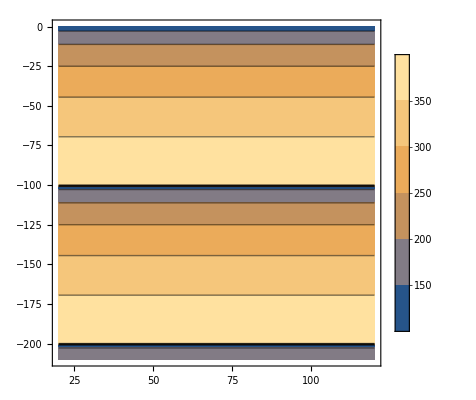

```mathematica
PlotVelocity[velModel]
```

```mathematica
timeNH=BuildTimeSection[horNHsorted, velModel][["timeNH"]]
```

{{{0,0},{20,0},{40,0},{60,0},{80,0},{100,0}},{{0,-0.668078},{20,-0.668078},{40,-0.668078},{60,-0.668078},{80,-0.668078},{100,-0.668078}},{{0,-1.36878},{20,-1.36878},{40,-1.36878},{60,-1.36878},{80,-1.36878},{100,-1.36878}}}

```mathematica
PlotTimeSection[timeNH]
```

-Graphics-

```mathematica
wells=BuildWellSet[horNHsorted ,timeNH, 2, "random"] [["wells"]]
```

{{1,20,{{Hor 1,0.,0.},{Hor 2,-100.,-0.668078},{Hor 3,-200.,-1.36878}}},{2,20,{{Hor 1,0.,0.},{Hor 2,-100.,-0.668078},{Hor 3,-200.,-1.36878}}}}

```mathematica
PlotDepthSectionWithWells[horNHsorted, wells]
```

-Graphics-

```mathematica
velModel
```

{{{{20,115,300},{20,114,350},{20,113,371},{20,112,387},{20,111,400},{20,110,412},{20,109,422},{20,108,432},{20,107,441},{20,106,450},{20,105,458},{20,104,466},{20,103,473},{20,102,480},{20,101,487},{20,100,494},{20,99,500},{20,98,506},{20,97,512},{20,96,518},{20,95,524},{20,94,529},{20,93,535},{20,92,540},{20,91,545},{20,90,550},{20,89,555},{20,88,560},{20,87,565},{20,86,569},{20,85,574},{20,84,578},{20,83,583},{20,82,587},{20,81,592},{20,80,596},{20,79,600},{20,78,604},{20,77,608},{20,76,612},{20,75,616},{20,74,620},{20,73,624},{20,72,628},{20,71,632},{20,70,635},{20,69,639},{20,68,643},{20,67,646},{20,66,650},{20,65,654}},{{40,113,300},{40,112,350},{40,111,371},{40,110,387},{40,109,400},{40,108,412},{40,107,422},{40,106,432},{40,105,441},{40,104,450},{40,103,458},{40,102,466},{40,101,473},{40,100,480},{40,99,487},{40,98,494},{40,97,500},{40,96,506},{40,95,512},{40,94,518},{40,93,524},{40,92,529},{40,91,535},{40,90,540},{40,89,545},{40,88,550},{40,87,555},{40,86,560},{40,85,565},{40,84,569},{40,83,574},{40,82,578},{40,81,583},{40,80,587},{40,79,592},{40,78,596},{40,77,600},{40,76,604},{40,75,608},{40,74,612},{40,73,616},{40,72,620},{40,71,624},{40,70,628},{40,69,632},{40,68,635},{40,67,639},{40,66,643},{40,65,646},{40,64,650},{40,63,654},{40,62,657},{40,61,661},{40,60,664},{40,59,667},{40,58,671},{40,57,674}},{{60,111,300},{60,110,350},{60,109,371},{60,108,387},{60,107,400},{60,106,412},{60,105,422},{60,104,432},{60,103,441},{60,102,450},{60,101,458},{60,100,466},{60,99,473},{60,98,480},{60,97,487},{60,96,494},{60,95,500},{60,94,506},{60,93,512},{60,92,518},{60,91,524},{60,90,529},{60,89,535},{60,88,540},{60,87,545},{60,86,550},{60,85,555},{60,84,560},{60,83,565},{60,82,569},{60,81,574},{60,80,578},{60,79,583},{60,78,587},{60,77,592},{60,76,596},{60,75,600},{60,74,604},{60,73,608},{60,72,612},{60,71,616},{60,70,620},{60,69,624},{60,68,628},{60,67,632},{60,66,635},{60,65,639},{60,64,643},{60,63,646},{60,62,650},{60,61,654},{60,60,657},{60,59,661},{60,58,664},{60,57,667},{60,56,671},{60,55,674},{60,54,677},{60,53,681},{60,52,684},{60,51,687},{60,50,691},{60,49,694}},{{80,109,300},{80,108,350},{80,107,371},{80,106,387},{80,105,400},{80,104,412},{80,103,422},{80,102,432},{80,101,441},{80,100,450},{80,99,458},{80,98,466},{80,97,473},{80,96,480},{80,95,487},{80,94,494},{80,93,500},{80,92,506},{80,91,512},{80,90,518},{80,89,524},{80,88,529},{80,87,535},{80,86,540},{80,85,545},{80,84,550},{80,83,555},{80,82,560},{80,81,565},{80,80,569},{80,79,574},{80,78,578},{80,77,583},{80,76,587},{80,75,592},{80,74,596},{80,73,600},{80,72,604},{80,71,608},{80,70,612},{80,69,616},{80,68,620},{80,67,624},{80,66,628},{80,65,632},{80,64,635},{80,63,639},{80,62,643},{80,61,646},{80,60,650},{80,59,654},{80,58,657},{80,57,661},{80,56,664},{80,55,667},{80,54,671},{80,53,674},{80,52,677},{80,51,681},{80,50,684},{80,49,687},{80,48,691},{80,47,694},{80,46,697},{80,45,700},{80,44,703},{80,43,706}},{{100,107,300},{100,106,350},{100,105,371},{100,104,387},{100,103,400},{100,102,412},{100,101,422},{100,100,432},{100,99,441},{100,98,450},{100,97,458},{100,96,466},{100,95,473},{100,94,480},{100,93,487},{100,92,494},{100,91,500},{100,90,506},{100,89,512},{100,88,518},{100,87,524},{100,86,529},{100,85,535},{100,84,540},{100,83,545},{100,82,550},{100,81,555},{100,80,560},{100,79,565},{100,78,569},{100,77,574},{100,76,578},{100,75,583},{100,74,587},{100,73,592},{100,72,596},{100,71,600},{100,70,604},{100,69,608},{100,68,612},{100,67,616},{100,66,620},{100,65,624},{100,64,628},{100,63,632},{100,62,635},{100,61,639},{100,60,643},{100,59,646},{100,58,650},{100,57,654},{100,56,657},{100,55,661},{100,54,664},{100,53,667},{100,52,671},{100,51,674},{100,50,677},{100,49,681},{100,48,684},{100,47,687},{100,46,691},{100,45,694},{100,44,697},{100,43,700},{100,42,703},{100,41,706},{100,40,709},{100,39,712},{100,38,715},{100,37,718},{100,36,721}},{{120,105,300},{120,104,350},{120,103,371},{120,102,387},{120,101,400},{120,100,412},{120,99,422},{120,98,432},{120,97,441},{120,96,450},{120,95,458},{120,94,466},{120,93,473},{120,92,480},{120,91,487},{120,90,494},{120,89,500},{120,88,506},{120,87,512},{120,86,518},{120,85,524},{120,84,529},{120,83,535},{120,82,540},{120,81,545},{120,80,550},{120,79,555},{120,78,560},{120,77,565},{120,76,569},{120,75,574},{120,74,578},{120,73,583},{120,72,587},{120,71,592},{120,70,596},{120,69,600},{120,68,604},{120,67,608},{120,66,612},{120,65,616},{120,64,620},{120,63,624},{120,62,628},{120,61,632},{120,60,635},{120,59,639},{120,58,643},{120,57,646},{120,56,650},{120,55,654},{120,54,657},{120,53,661},{120,52,664},{120,51,667},{120,50,671},{120,49,674},{120,48,677},{120,47,681},{120,46,684},{120,45,687},{120,44,691},{120,43,694},{120,42,697},{120,41,700},{120,40,703},{120,39,706},{120,38,709},{120,37,712},{120,36,715},{120,35,718},{120,34,721},{120,33,724},{120,32,727},{120,31,730},{120,30,733},{120,29,736}},{{140,103,300},{140,102,350},{140,101,371},{140,100,387},{140,99,400},{140,98,412},{140,97,422},{140,96,432},{140,95,441},{140,94,450},{140,93,458},{140,92,466},{140,91,473},{140,90,480},{140,89,487},{140,88,494},{140,87,500},{140,86,506},{140,85,512},{140,84,518},{140,83,524},{140,82,529},{140,81,535},{140,80,540},{140,79,545},{140,78,550},{140,77,555},{140,76,560},{140,75,565},{140,74,569},{140,73,574},{140,72,578},{140,71,583},{140,70,587},{140,69,592},{140,68,596},{140,67,600},{140,66,604},{140,65,608},{140,64,612},{140,63,616},{140,62,620},{140,61,624},{140,60,628},{140,59,632},{140,58,635},{140,57,639},{140,56,643},{140,55,646},{140,54,650},{140,53,654},{140,52,657},{140,51,661},{140,50,664},{140,49,667},{140,48,671},{140,47,674},{140,46,677},{140,45,681},{140,44,684},{140,43,687},{140,42,691},{140,41,694},{140,40,697},{140,39,700},{140,38,703},{140,37,706},{140,36,709},{140,35,712},{140,34,715},{140,33,718},{140,32,721},{140,31,724},{140,30,727},{140,29,730},{140,28,733},{140,27,736},{140,26,739},{140,25,742},{140,24,744},{140,23,747}},{{160,101,300},{160,100,350},{160,99,371},{160,98,387},{160,97,400},{160,96,412},{160,95,422},{160,94,432},{160,93,441},{160,92,450},{160,91,458},{160,90,466},{160,89,473},{160,88,480},{160,87,487},{160,86,494},{160,85,500},{160,84,506},{160,83,512},{160,82,518},{160,81,524},{160,80,529},{160,79,535},{160,78,540},{160,77,545},{160,76,550},{160,75,555},{160,74,560},{160,73,565},{160,72,569},{160,71,574},{160,70,578},{160,69,583},{160,68,587},{160,67,592},{160,66,596},{160,65,600},{160,64,604},{160,63,608},{160,62,612},{160,61,616},{160,60,620},{160,59,624},{160,58,628},{160,57,632},{160,56,635},{160,55,639},{160,54,643},{160,53,646},{160,52,650},{160,51,654},{160,50,657},{160,49,661},{160,48,664},{160,47,667},{160,46,671},{160,45,674},{160,44,677},{160,43,681},{160,42,684},{160,41,687},{160,40,691},{160,39,694},{160,38,697},{160,37,700},{160,36,703},{160,35,706},{160,34,709},{160,33,712},{160,32,715},{160,31,718},{160,30,721},{160,29,724},{160,28,727},{160,27,730},{160,26,733},{160,25,736},{160,24,739},{160,23,742},{160,22,744},{160,21,747},{160,20,750},{160,19,753},{160,18,756},{160,17,758}},{{180,99,300},{180,98,350},{180,97,371},{180,96,387},{180,95,400},{180,94,412},{180,93,422},{180,92,432},{180,91,441},{180,90,450},{180,89,458},{180,88,466},{180,87,473},{180,86,480},{180,85,487},{180,84,494},{180,83,500},{180,82,506},{180,81,512},{180,80,518},{180,79,524},{180,78,529},{180,77,535},{180,76,540},{180,75,545},{180,74,550},{180,73,555},{180,72,560},{180,71,565},{180,70,569},{180,69,574},{180,68,578},{180,67,583},{180,66,587},{180,65,592},{180,64,596},{180,63,600},{180,62,604},{180,61,608},{180,60,612},{180,59,616},{180,58,620},{180,57,624},{180,56,628},{180,55,632},{180,54,635},{180,53,639},{180,52,643},{180,51,646},{180,50,650},{180,49,654},{180,48,657},{180,47,661},{180,46,664},{180,45,667},{180,44,671},{180,43,674},{180,42,677},{180,41,681},{180,40,684},{180,39,687},{180,38,691},{180,37,694},{180,36,697},{180,35,700},{180,34,703},{180,33,706},{180,32,709},{180,31,712},{180,30,715},{180,29,718},{180,28,721},{180,27,724},{180,26,727},{180,25,730},{180,24,733},{180,23,736},{180,22,739},{180,21,742},{180,20,744},{180,19,747},{180,18,750},{180,17,753},{180,16,756},{180,15,758},{180,14,761}},{{200,97,300},{200,96,350},{200,95,371},{200,94,387},{200,93,400},{200,92,412},{200,91,422},{200,90,432},{200,89,441},{200,88,450},{200,87,458},{200,86,466},{200,85,473},{200,84,480},{200,83,487},{200,82,494},{200,81,500},{200,80,506},{200,79,512},{200,78,518},{200,77,524},{200,76,529},{200,75,535},{200,74,540},{200,73,545},{200,72,550},{200,71,555},{200,70,560},{200,69,565},{200,68,569},{200,67,574},{200,66,578},{200,65,583},{200,64,587},{200,63,592},{200,62,596},{200,61,600},{200,60,604},{200,59,608},{200,58,612},{200,57,616},{200,56,620},{200,55,624},{200,54,628},{200,53,632},{200,52,635},{200,51,639},{200,50,643},{200,49,646},{200,48,650},{200,47,654},{200,46,657},{200,45,661},{200,44,664},{200,43,667},{200,42,671},{200,41,674},{200,40,677},{200,39,681},{200,38,684},{200,37,687},{200,36,691},{200,35,694},{200,34,697},{200,33,700},{200,32,703},{200,31,706},{200,30,709},{200,29,712},{200,28,715},{200,27,718},{200,26,721},{200,25,724},{200,24,727},{200,23,730},{200,22,733},{200,21,736},{200,20,739},{200,19,742},{200,18,744},{200,17,747},{200,16,750},{200,15,753},{200,14,756},{200,13,758},{200,12,761},{200,11,764},{200,10,766},{200,9,769},{200,8,772}},{{220,95,300},{220,94,350},{220,93,371},{220,92,387},{220,91,400},{220,90,412},{220,89,422},{220,88,432},{220,87,441},{220,86,450},{220,85,458},{220,84,466},{220,83,473},{220,82,480},{220,81,487},{220,80,494},{220,79,500},{220,78,506},{220,77,512},{220,76,518},{220,75,524},{220,74,529},{220,73,535},{220,72,540},{220,71,545},{220,70,550},{220,69,555},{220,68,560},{220,67,565},{220,66,569},{220,65,574},{220,64,578},{220,63,583},{220,62,587},{220,61,592},{220,60,596},{220,59,600},{220,58,604},{220,57,608},{220,56,612},{220,55,616},{220,54,620},{220,53,624},{220,52,628},{220,51,632},{220,50,635},{220,49,639},{220,48,643},{220,47,646},{220,46,650},{220,45,654},{220,44,657},{220,43,661},{220,42,664},{220,41,667},{220,40,671},{220,39,674},{220,38,677},{220,37,681},{220,36,684},{220,35,687},{220,34,691},{220,33,694},{220,32,697},{220,31,700},{220,30,703},{220,29,706},{220,28,709},{220,27,712},{220,26,715},{220,25,718},{220,24,721},{220,23,724},{220,22,727},{220,21,730},{220,20,733},{220,19,736},{220,18,739},{220,17,742},{220,16,744},{220,15,747},{220,14,750},{220,13,753},{220,12,756},{220,11,758},{220,10,761},{220,9,764},{220,8,766},{220,7,769},{220,6,772},{220,5,774},{220,4,777}},{{240,94,300},{240,93,350},{240,92,371},{240,91,387},{240,90,400},{240,89,412},{240,88,422},{240,87,432},{240,86,441},{240,85,450},{240,84,458},{240,83,466},{240,82,473},{240,81,480},{240,80,487},{240,79,494},{240,78,500},{240,77,506},{240,76,512},{240,75,518},{240,74,524},{240,73,529},{240,72,535},{240,71,540},{240,70,545},{240,69,550},{240,68,555},{240,67,560},{240,66,565},{240,65,569},{240,64,574},{240,63,578},{240,62,583},{240,61,587},{240,60,592},{240,59,596},{240,58,600},{240,57,604},{240,56,608},{240,55,612},{240,54,616},{240,53,620},{240,52,624},{240,51,628},{240,50,632},{240,49,635},{240,48,639},{240,47,643},{240,46,646},{240,45,650},{240,44,654},{240,43,657},{240,42,661},{240,41,664},{240,40,667},{240,39,671},{240,38,674},{240,37,677},{240,36,681},{240,35,684},{240,34,687},{240,33,691},{240,32,694},{240,31,697},{240,30,700},{240,29,703},{240,28,706},{240,27,709},{240,26,712},{240,25,715},{240,24,718},{240,23,721},{240,22,724},{240,21,727},{240,20,730},{240,19,733},{240,18,736},{240,17,739},{240,16,742},{240,15,744},{240,14,747},{240,13,750},{240,12,753},{240,11,756},{240,10,758},{240,9,761},{240,8,764},{240,7,766},{240,6,769},{240,5,772},{240,4,774},{240,3,777},{240,2,780},{240,1,782}},{{260,92,300},{260,91,350},{260,90,371},{260,89,387},{260,88,400},{260,87,412},{260,86,422},{260,85,432},{260,84,441},{260,83,450},{260,82,458},{260,81,466},{260,80,473},{260,79,480},{260,78,487},{260,77,494},{260,76,500},{260,75,506},{260,74,512},{260,73,518},{260,72,524},{260,71,529},{260,70,535},{260,69,540},{260,68,545},{260,67,550},{260,66,555},{260,65,560},{260,64,565},{260,63,569},{260,62,574},{260,61,578},{260,60,583},{260,59,587},{260,58,592},{260,57,596},{260,56,600},{260,55,604},{260,54,608},{260,53,612},{260,52,616},{260,51,620},{260,50,624},{260,49,628},{260,48,632},{260,47,635},{260,46,639},{260,45,643},{260,44,646},{260,43,650},{260,42,654},{260,41,657},{260,40,661},{260,39,664},{260,38,667},{260,37,671},{260,36,674},{260,35,677},{260,34,681},{260,33,684},{260,32,687},{260,31,691},{260,30,694},{260,29,697},{260,28,700},{260,27,703},{260,26,706},{260,25,709},{260,24,712},{260,23,715},{260,22,718},{260,21,721},{260,20,724},{260,19,727},{260,18,730},{260,17,733},{260,16,736},{260,15,739},{260,14,742},{260,13,744},{260,12,747},{260,11,750},{260,10,753},{260,9,756},{260,8,758},{260,7,761},{260,6,764},{260,5,766},{260,4,769},{260,3,772},{260,2,774},{260,1,777},{260,0,780},{260,-1,782},{260,-2,785}},{{280,90,300},{280,89,350},{280,88,371},{280,87,387},{280,86,400},{280,85,412},{280,84,422},{280,83,432},{280,82,441},{280,81,450},{280,80,458},{280,79,466},{280,78,473},{280,77,480},{280,76,487},{280,75,494},{280,74,500},{280,73,506},{280,72,512},{280,71,518},{280,70,524},{280,69,529},{280,68,535},{280,67,540},{280,66,545},{280,65,550},{280,64,555},{280,63,560},{280,62,565},{280,61,569},{280,60,574},{280,59,578},{280,58,583},{280,57,587},{280,56,592},{280,55,596},{280,54,600},{280,53,604},{280,52,608},{280,51,612},{280,50,616},{280,49,620},{280,48,624},{280,47,628},{280,46,632},{280,45,635},{280,44,639},{280,43,643},{280,42,646},{280,41,650},{280,40,654},{280,39,657},{280,38,661},{280,37,664},{280,36,667},{280,35,671},{280,34,674},{280,33,677},{280,32,681},{280,31,684},{280,30,687},{280,29,691},{280,28,694},{280,27,697},{280,26,700},{280,25,703},{280,24,706},{280,23,709},{280,22,712},{280,21,715},{280,20,718},{280,19,721},{280,18,724},{280,17,727},{280,16,730},{280,15,733},{280,14,736},{280,13,739},{280,12,742},{280,11,744},{280,10,747},{280,9,750},{280,8,753},{280,7,756},{280,6,758},{280,5,761},{280,4,764},{280,3,766},{280,2,769},{280,1,772},{280,0,774},{280,-1,777},{280,-2,780},{280,-3,782}},{{300,88,300},{300,87,350},{300,86,371},{300,85,387},{300,84,400},{300,83,412},{300,82,422},{300,81,432},{300,80,441},{300,79,450},{300,78,458},{300,77,466},{300,76,473},{300,75,480},{300,74,487},{300,73,494},{300,72,500},{300,71,506},{300,70,512},{300,69,518},{300,68,524},{300,67,529},{300,66,535},{300,65,540},{300,64,545},{300,63,550},{300,62,555},{300,61,560},{300,60,565},{300,59,569},{300,58,574},{300,57,578},{300,56,583},{300,55,587},{300,54,592},{300,53,596},{300,52,600},{300,51,604},{300,50,608},{300,49,612},{300,48,616},{300,47,620},{300,46,624},{300,45,628},{300,44,632},{300,43,635},{300,42,639},{300,41,643},{300,40,646},{300,39,650},{300,38,654},{300,37,657},{300,36,661},{300,35,664},{300,34,667},{300,33,671},{300,32,674},{300,31,677},{300,30,681},{300,29,684},{300,28,687},{300,27,691},{300,26,694},{300,25,697},{300,24,700},{300,23,703},{300,22,706},{300,21,709},{300,20,712},{300,19,715},{300,18,718},{300,17,721},{300,16,724},{300,15,727},{300,14,730},{300,13,733},{300,12,736},{300,11,739},{300,10,742},{300,9,744},{300,8,747},{300,7,750},{300,6,753},{300,5,756},{300,4,758},{300,3,761},{300,2,764},{300,1,766},{300,0,769},{300,-1,772},{300,-2,774},{300,-3,777},{300,-4,780},{300,-5,782}},{{320,86,300},{320,85,350},{320,84,371},{320,83,387},{320,82,400},{320,81,412},{320,80,422},{320,79,432},{320,78,441},{320,77,450},{320,76,458},{320,75,466},{320,74,473},{320,73,480},{320,72,487},{320,71,494},{320,70,500},{320,69,506},{320,68,512},{320,67,518},{320,66,524},{320,65,529},{320,64,535},{320,63,540},{320,62,545},{320,61,550},{320,60,555},{320,59,560},{320,58,565},{320,57,569},{320,56,574},{320,55,578},{320,54,583},{320,53,587},{320,52,592},{320,51,596},{320,50,600},{320,49,604},{320,48,608},{320,47,612},{320,46,616},{320,45,620},{320,44,624},{320,43,628},{320,42,632},{320,41,635},{320,40,639},{320,39,643},{320,38,646},{320,37,650},{320,36,654},{320,35,657},{320,34,661},{320,33,664},{320,32,667},{320,31,671},{320,30,674},{320,29,677},{320,28,681},{320,27,684},{320,26,687},{320,25,691},{320,24,694},{320,23,697},{320,22,700},{320,21,703},{320,20,706},{320,19,709},{320,18,712},{320,17,715},{320,16,718},{320,15,721},{320,14,724},{320,13,727},{320,12,730},{320,11,733},{320,10,736},{320,9,739},{320,8,742},{320,7,744},{320,6,747},{320,5,750},{320,4,753},{320,3,756},{320,2,758},{320,1,761},{320,0,764},{320,-1,766},{320,-2,769},{320,-3,772},{320,-4,774},{320,-5,777}},{{340,85,300},{340,84,350},{340,83,371},{340,82,387},{340,81,400},{340,80,412},{340,79,422},{340,78,432},{340,77,441},{340,76,450},{340,75,458},{340,74,466},{340,73,473},{340,72,480},{340,71,487},{340,70,494},{340,69,500},{340,68,506},{340,67,512},{340,66,518},{340,65,524},{340,64,529},{340,63,535},{340,62,540},{340,61,545},{340,60,550},{340,59,555},{340,58,560},{340,57,565},{340,56,569},{340,55,574},{340,54,578},{340,53,583},{340,52,587},{340,51,592},{340,50,596},{340,49,600},{340,48,604},{340,47,608},{340,46,612},{340,45,616},{340,44,620},{340,43,624},{340,42,628},{340,41,632},{340,40,635},{340,39,639},{340,38,643},{340,37,646},{340,36,650},{340,35,654},{340,34,657},{340,33,661},{340,32,664},{340,31,667},{340,30,671},{340,29,674},{340,28,677},{340,27,681},{340,26,684},{340,25,687},{340,24,691},{340,23,694},{340,22,697},{340,21,700},{340,20,703},{340,19,706},{340,18,709},{340,17,712},{340,16,715},{340,15,718},{340,14,721},{340,13,724},{340,12,727},{340,11,730},{340,10,733},{340,9,736},{340,8,739},{340,7,742},{340,6,744},{340,5,747},{340,4,750},{340,3,753},{340,2,756},{340,1,758},{340,0,761},{340,-1,764},{340,-2,766},{340,-3,769},{340,-4,772},{340,-5,774},{340,-6,777}},{{360,83,300},{360,82,350},{360,81,371},{360,80,387},{360,79,400},{360,78,412},{360,77,422},{360,76,432},{360,75,441},{360,74,450},{360,73,458},{360,72,466},{360,71,473},{360,70,480},{360,69,487},{360,68,494},{360,67,500},{360,66,506},{360,65,512},{360,64,518},{360,63,524},{360,62,529},{360,61,535},{360,60,540},{360,59,545},{360,58,550},{360,57,555},{360,56,560},{360,55,565},{360,54,569},{360,53,574},{360,52,578},{360,51,583},{360,50,587},{360,49,592},{360,48,596},{360,47,600},{360,46,604},{360,45,608},{360,44,612},{360,43,616},{360,42,620},{360,41,624},{360,40,628},{360,39,632},{360,38,635},{360,37,639},{360,36,643},{360,35,646},{360,34,650},{360,33,654},{360,32,657},{360,31,661},{360,30,664},{360,29,667},{360,28,671},{360,27,674},{360,26,677},{360,25,681},{360,24,684},{360,23,687},{360,22,691},{360,21,694},{360,20,697},{360,19,700},{360,18,703},{360,17,706},{360,16,709},{360,15,712},{360,14,715},{360,13,718},{360,12,721},{360,11,724},{360,10,727},{360,9,730},{360,8,733},{360,7,736},{360,6,739},{360,5,742},{360,4,744},{360,3,747},{360,2,750},{360,1,753},{360,0,756},{360,-1,758},{360,-2,761},{360,-3,764},{360,-4,766},{360,-5,769},{360,-6,772}},{{380,82,300},{380,81,350},{380,80,371},{380,79,387},{380,78,400},{380,77,412},{380,76,422},{380,75,432},{380,74,441},{380,73,450},{380,72,458},{380,71,466},{380,70,473},{380,69,480},{380,68,487},{380,67,494},{380,66,500},{380,65,506},{380,64,512},{380,63,518},{380,62,524},{380,61,529},{380,60,535},{380,59,540},{380,58,545},{380,57,550},{380,56,555},{380,55,560},{380,54,565},{380,53,569},{380,52,574},{380,51,578},{380,50,583},{380,49,587},{380,48,592},{380,47,596},{380,46,600},{380,45,604},{380,44,608},{380,43,612},{380,42,616},{380,41,620},{380,40,624},{380,39,628},{380,38,632},{380,37,635},{380,36,639},{380,35,643},{380,34,646},{380,33,650},{380,32,654},{380,31,657},{380,30,661},{380,29,664},{380,28,667},{380,27,671},{380,26,674},{380,25,677},{380,24,681},{380,23,684},{380,22,687},{380,21,691},{380,20,694},{380,19,697},{380,18,700},{380,17,703},{380,16,706},{380,15,709},{380,14,712},{380,13,715},{380,12,718},{380,11,721},{380,10,724},{380,9,727},{380,8,730},{380,7,733},{380,6,736},{380,5,739},{380,4,742},{380,3,744},{380,2,747},{380,1,750},{380,0,753},{380,-1,756},{380,-2,758},{380,-3,761},{380,-4,764},{380,-5,766}},{{400,80,300},{400,79,350},{400,78,371},{400,77,387},{400,76,400},{400,75,412},{400,74,422},{400,73,432},{400,72,441},{400,71,450},{400,70,458},{400,69,466},{400,68,473},{400,67,480},{400,66,487},{400,65,494},{400,64,500},{400,63,506},{400,62,512},{400,61,518},{400,60,524},{400,59,529},{400,58,535},{400,57,540},{400,56,545},{400,55,550},{400,54,555},{400,53,560},{400,52,565},{400,51,569},{400,50,574},{400,49,578},{400,48,583},{400,47,587},{400,46,592},{400,45,596},{400,44,600},{400,43,604},{400,42,608},{400,41,612},{400,40,616},{400,39,620},{400,38,624},{400,37,628},{400,36,632},{400,35,635},{400,34,639},{400,33,643},{400,32,646},{400,31,650},{400,30,654},{400,29,657},{400,28,661},{400,27,664},{400,26,667},{400,25,671},{400,24,674},{400,23,677},{400,22,681},{400,21,684},{400,20,687},{400,19,691},{400,18,694},{400,17,697},{400,16,700},{400,15,703},{400,14,706},{400,13,709},{400,12,712},{400,11,715},{400,10,718},{400,9,721},{400,8,724},{400,7,727},{400,6,730},{400,5,733},{400,4,736},{400,3,739},{400,2,742},{400,1,744},{400,0,747},{400,-1,750},{400,-2,753},{400,-3,756},{400,-4,758},{400,-5,761},{400,-6,764}},{{420,79,300},{420,78,350},{420,77,371},{420,76,387},{420,75,400},{420,74,412},{420,73,422},{420,72,432},{420,71,441},{420,70,450},{420,69,458},{420,68,466},{420,67,473},{420,66,480},{420,65,487},{420,64,494},{420,63,500},{420,62,506},{420,61,512},{420,60,518},{420,59,524},{420,58,529},{420,57,535},{420,56,540},{420,55,545},{420,54,550},{420,53,555},{420,52,560},{420,51,565},{420,50,569},{420,49,574},{420,48,578},{420,47,583},{420,46,587},{420,45,592},{420,44,596},{420,43,600},{420,42,604},{420,41,608},{420,40,612},{420,39,616},{420,38,620},{420,37,624},{420,36,628},{420,35,632},{420,34,635},{420,33,639},{420,32,643},{420,31,646},{420,30,650},{420,29,654},{420,28,657},{420,27,661},{420,26,664},{420,25,667},{420,24,671},{420,23,674},{420,22,677},{420,21,681},{420,20,684},{420,19,687},{420,18,691},{420,17,694},{420,16,697},{420,15,700},{420,14,703},{420,13,706},{420,12,709},{420,11,712},{420,10,715},{420,9,718},{420,8,721},{420,7,724},{420,6,727},{420,5,730},{420,4,733},{420,3,736},{420,2,739},{420,1,742},{420,0,744},{420,-1,747},{420,-2,750},{420,-3,753}},{{440,78,300},{440,77,350},{440,76,371},{440,75,387},{440,74,400},{440,73,412},{440,72,422},{440,71,432},{440,70,441},{440,69,450},{440,68,458},{440,67,466},{440,66,473},{440,65,480},{440,64,487},{440,63,494},{440,62,500},{440,61,506},{440,60,512},{440,59,518},{440,58,524},{440,57,529},{440,56,535},{440,55,540},{440,54,545},{440,53,550},{440,52,555},{440,51,560},{440,50,565},{440,49,569},{440,48,574},{440,47,578},{440,46,583},{440,45,587},{440,44,592},{440,43,596},{440,42,600},{440,41,604},{440,40,608},{440,39,612},{440,38,616},{440,37,620},{440,36,624},{440,35,628},{440,34,632},{440,33,635},{440,32,639},{440,31,643},{440,30,646},{440,29,650},{440,28,654},{440,27,657},{440,26,661},{440,25,664},{440,24,667},{440,23,671},{440,22,674},{440,21,677},{440,20,681},{440,19,684},{440,18,687},{440,17,691},{440,16,694},{440,15,697},{440,14,700},{440,13,703},{440,12,706},{440,11,709},{440,10,712},{440,9,715},{440,8,718},{440,7,721},{440,6,724},{440,5,727},{440,4,730},{440,3,733},{440,2,736},{440,1,739},{440,0,742},{440,-1,744},{440,-2,747}},{{460,76,300},{460,75,350},{460,74,371},{460,73,387},{460,72,400},{460,71,412},{460,70,422},{460,69,432},{460,68,441},{460,67,450},{460,66,458},{460,65,466},{460,64,473},{460,63,480},{460,62,487},{460,61,494},{460,60,500},{460,59,506},{460,58,512},{460,57,518},{460,56,524},{460,55,529},{460,54,535},{460,53,540},{460,52,545},{460,51,550},{460,50,555},{460,49,560},{460,48,565},{460,47,569},{460,46,574},{460,45,578},{460,44,583},{460,43,587},{460,42,592},{460,41,596},{460,40,600},{460,39,604},{460,38,608},{460,37,612},{460,36,616},{460,35,620},{460,34,624},{460,33,628},{460,32,632},{460,31,635},{460,30,639},{460,29,643},{460,28,646},{460,27,650},{460,26,654},{460,25,657},{460,24,661},{460,23,664},{460,22,667},{460,21,671},{460,20,674},{460,19,677},{460,18,681},{460,17,684},{460,16,687},{460,15,691},{460,14,694},{460,13,697},{460,12,700},{460,11,703},{460,10,706},{460,9,709},{460,8,712},{460,7,715},{460,6,718},{460,5,721},{460,4,724},{460,3,727},{460,2,730},{460,1,733},{460,0,736},{460,-1,739}},{{480,75,300},{480,74,350},{480,73,371},{480,72,387},{480,71,400},{480,70,412},{480,69,422},{480,68,432},{480,67,441},{480,66,450},{480,65,458},{480,64,466},{480,63,473},{480,62,480},{480,61,487},{480,60,494},{480,59,500},{480,58,506},{480,57,512},{480,56,518},{480,55,524},{480,54,529},{480,53,535},{480,52,540},{480,51,545},{480,50,550},{480,49,555},{480,48,560},{480,47,565},{480,46,569},{480,45,574},{480,44,578},{480,43,583},{480,42,587},{480,41,592},{480,40,596},{480,39,600},{480,38,604},{480,37,608},{480,36,612},{480,35,616},{480,34,620},{480,33,624},{480,32,628},{480,31,632},{480,30,635},{480,29,639},{480,28,643},{480,27,646},{480,26,650},{480,25,654},{480,24,657},{480,23,661},{480,22,664},{480,21,667},{480,20,671},{480,19,674},{480,18,677},{480,17,681},{480,16,684},{480,15,687},{480,14,691},{480,13,694},{480,12,697},{480,11,700},{480,10,703},{480,9,706},{480,8,709},{480,7,712},{480,6,715},{480,5,718},{480,4,721},{480,3,724},{480,2,727},{480,1,730},{480,0,733},{480,-1,736}},{{500,74,300},{500,73,350},{500,72,371},{500,71,387},{500,70,400},{500,69,412},{500,68,422},{500,67,432},{500,66,441},{500,65,450},{500,64,458},{500,63,466},{500,62,473},{500,61,480},{500,60,487},{500,59,494},{500,58,500},{500,57,506},{500,56,512},{500,55,518},{500,54,524},{500,53,529},{500,52,535},{500,51,540},{500,50,545},{500,49,550},{500,48,555},{500,47,560},{500,46,565},{500,45,569},{500,44,574},{500,43,578},{500,42,583},{500,41,587},{500,40,592},{500,39,596},{500,38,600},{500,37,604},{500,36,608},{500,35,612},{500,34,616},{500,33,620},{500,32,624},{500,31,628},{500,30,632},{500,29,635},{500,28,639},{500,27,643},{500,26,646},{500,25,650},{500,24,654},{500,23,657},{500,22,661},{500,21,664},{500,20,667},{500,19,671},{500,18,674},{500,17,677},{500,16,681},{500,15,684},{500,14,687},{500,13,691},{500,12,694},{500,11,697},{500,10,700},{500,9,703},{500,8,706},{500,7,709},{500,6,712},{500,5,715},{500,4,718},{500,3,721},{500,2,724},{500,1,727},{500,0,730},{500,-1,733}},{{520,73,300},{520,72,350},{520,71,371},{520,70,387},{520,69,400},{520,68,412},{520,67,422},{520,66,432},{520,65,441},{520,64,450},{520,63,458},{520,62,466},{520,61,473},{520,60,480},{520,59,487},{520,58,494},{520,57,500},{520,56,506},{520,55,512},{520,54,518},{520,53,524},{520,52,529},{520,51,535},{520,50,540},{520,49,545},{520,48,550},{520,47,555},{520,46,560},{520,45,565},{520,44,569},{520,43,574},{520,42,578},{520,41,583},{520,40,587},{520,39,592},{520,38,596},{520,37,600},{520,36,604},{520,35,608},{520,34,612},{520,33,616},{520,32,620},{520,31,624},{520,30,628},{520,29,632},{520,28,635},{520,27,639},{520,26,643},{520,25,646},{520,24,650},{520,23,654},{520,22,657},{520,21,661},{520,20,664},{520,19,667},{520,18,671},{520,17,674},{520,16,677},{520,15,681},{520,14,684},{520,13,687},{520,12,691},{520,11,694},{520,10,697},{520,9,700},{520,8,703},{520,7,706},{520,6,709},{520,5,712},{520,4,715},{520,3,718},{520,2,721},{520,1,724},{520,0,727}},{{540,71,300},{540,70,350},{540,69,371},{540,68,387},{540,67,400},{540,66,412},{540,65,422},{540,64,432},{540,63,441},{540,62,450},{540,61,458},{540,60,466},{540,59,473},{540,58,480},{540,57,487},{540,56,494},{540,55,500},{540,54,506},{540,53,512},{540,52,518},{540,51,524},{540,50,529},{540,49,535},{540,48,540},{540,47,545},{540,46,550},{540,45,555},{540,44,560},{540,43,565},{540,42,569},{540,41,574},{540,40,578},{540,39,583},{540,38,587},{540,37,592},{540,36,596},{540,35,600},{540,34,604},{540,33,608},{540,32,612},{540,31,616},{540,30,620},{540,29,624},{540,28,628},{540,27,632},{540,26,635},{540,25,639},{540,24,643},{540,23,646},{540,22,650},{540,21,654},{540,20,657},{540,19,661},{540,18,664},{540,17,667},{540,16,671},{540,15,674},{540,14,677},{540,13,681},{540,12,684},{540,11,687},{540,10,691},{540,9,694},{540,8,697},{540,7,700},{540,6,703},{540,5,706},{540,4,709},{540,3,712},{540,2,715},{540,1,718}},{{560,70,300},{560,69,350},{560,68,371},{560,67,387},{560,66,400},{560,65,412},{560,64,422},{560,63,432},{560,62,441},{560,61,450},{560,60,458},{560,59,466},{560,58,473},{560,57,480},{560,56,487},{560,55,494},{560,54,500},{560,53,506},{560,52,512},{560,51,518},{560,50,524},{560,49,529},{560,48,535},{560,47,540},{560,46,545},{560,45,550},{560,44,555},{560,43,560},{560,42,565},{560,41,569},{560,40,574},{560,39,578},{560,38,583},{560,37,587},{560,36,592},{560,35,596},{560,34,600},{560,33,604},{560,32,608},{560,31,612},{560,30,616},{560,29,620},{560,28,624},{560,27,628},{560,26,632},{560,25,635},{560,24,639},{560,23,643},{560,22,646},{560,21,650},{560,20,654},{560,19,657},{560,18,661},{560,17,664},{560,16,667},{560,15,671},{560,14,674},{560,13,677},{560,12,681},{560,11,684},{560,10,687},{560,9,691},{560,8,694},{560,7,697},{560,6,700},{560,5,703},{560,4,706},{560,3,709}},{{580,69,300},{580,68,350},{580,67,371},{580,66,387},{580,65,400},{580,64,412},{580,63,422},{580,62,432},{580,61,441},{580,60,450},{580,59,458},{580,58,466},{580,57,473},{580,56,480},{580,55,487},{580,54,494},{580,53,500},{580,52,506},{580,51,512},{580,50,518},{580,49,524},{580,48,529},{580,47,535},{580,46,540},{580,45,545},{580,44,550},{580,43,555},{580,42,560},{580,41,565},{580,40,569},{580,39,574},{580,38,578},{580,37,583},{580,36,587},{580,35,592},{580,34,596},{580,33,600},{580,32,604},{580,31,608},{580,30,612},{580,29,616},{580,28,620},{580,27,624},{580,26,628},{580,25,632},{580,24,635},{580,23,639},{580,22,643},{580,21,646},{580,20,650},{580,19,654},{580,18,657},{580,17,661},{580,16,664},{580,15,667},{580,14,671},{580,13,674},{580,12,677},{580,11,681},{580,10,684},{580,9,687},{580,8,691},{580,7,694},{580,6,697},{580,5,700},{580,4,703}},{{600,68,300},{600,67,350},{600,66,371},{600,65,387},{600,64,400},{600,63,412},{600,62,422},{600,61,432},{600,60,441},{600,59,450},{600,58,458},{600,57,466},{600,56,473},{600,55,480},{600,54,487},{600,53,494},{600,52,500},{600,51,506},{600,50,512},{600,49,518},{600,48,524},{600,47,529},{600,46,535},{600,45,540},{600,44,545},{600,43,550},{600,42,555},{600,41,560},{600,40,565},{600,39,569},{600,38,574},{600,37,578},{600,36,583},{600,35,587},{600,34,592},{600,33,596},{600,32,600},{600,31,604},{600,30,608},{600,29,612},{600,28,616},{600,27,620},{600,26,624},{600,25,628},{600,24,632},{600,23,635},{600,22,639},{600,21,643},{600,20,646},{600,19,650},{600,18,654},{600,17,657},{600,16,661},{600,15,664},{600,14,667},{600,13,671},{600,12,674},{600,11,677},{600,10,681},{600,9,684},{600,8,687},{600,7,691},{600,6,694},{600,5,697},{600,4,700},{600,3,703}},{{620,67,300},{620,66,350},{620,65,371},{620,64,387},{620,63,400},{620,62,412},{620,61,422},{620,60,432},{620,59,441},{620,58,450},{620,57,458},{620,56,466},{620,55,473},{620,54,480},{620,53,487},{620,52,494},{620,51,500},{620,50,506},{620,49,512},{620,48,518},{620,47,524},{620,46,529},{620,45,535},{620,44,540},{620,43,545},{620,42,550},{620,41,555},{620,40,560},{620,39,565},{620,38,569},{620,37,574},{620,36,578},{620,35,583},{620,34,587},{620,33,592},{620,32,596},{620,31,600},{620,30,604},{620,29,608},{620,28,612},{620,27,616},{620,26,620},{620,25,624},{620,24,628},{620,23,632},{620,22,635},{620,21,639},{620,20,643},{620,19,646},{620,18,650},{620,17,654},{620,16,657},{620,15,661},{620,14,664},{620,13,667},{620,12,671},{620,11,674},{620,10,677},{620,9,681},{620,8,684},{620,7,687},{620,6,691},{620,5,694},{620,4,697},{620,3,700}},{{640,67,300},{640,66,350},{640,65,371},{640,64,387},{640,63,400},{640,62,412},{640,61,422},{640,60,432},{640,59,441},{640,58,450},{640,57,458},{640,56,466},{640,55,473},{640,54,480},{640,53,487},{640,52,494},{640,51,500},{640,50,506},{640,49,512},{640,48,518},{640,47,524},{640,46,529},{640,45,535},{640,44,540},{640,43,545},{640,42,550},{640,41,555},{640,40,560},{640,39,565},{640,38,569},{640,37,574},{640,36,578},{640,35,583},{640,34,587},{640,33,592},{640,32,596},{640,31,600},{640,30,604},{640,29,608},{640,28,612},{640,27,616},{640,26,620},{640,25,624},{640,24,628},{640,23,632},{640,22,635},{640,21,639},{640,20,643},{640,19,646},{640,18,650},{640,17,654},{640,16,657},{640,15,661},{640,14,664},{640,13,667},{640,12,671},{640,11,674},{640,10,677},{640,9,681},{640,8,684},{640,7,687},{640,6,691},{640,5,694},{640,4,697},{640,3,700}},{{660,66,300},{660,65,350},{660,64,371},{660,63,387},{660,62,400},{660,61,412},{660,60,422},{660,59,432},{660,58,441},{660,57,450},{660,56,458},{660,55,466},{660,54,473},{660,53,480},{660,52,487},{660,51,494},{660,50,500},{660,49,506},{660,48,512},{660,47,518},{660,46,524},{660,45,529},{660,44,535},{660,43,540},{660,42,545},{660,41,550},{660,40,555},{660,39,560},{660,38,565},{660,37,569},{660,36,574},{660,35,578},{660,34,583},{660,33,587},{660,32,592},{660,31,596},{660,30,600},{660,29,604},{660,28,608},{660,27,612},{660,26,616},{660,25,620},{660,24,624},{660,23,628},{660,22,632},{660,21,635},{660,20,639},{660,19,643},{660,18,646},{660,17,650},{660,16,654},{660,15,657},{660,14,661},{660,13,664},{660,12,667},{660,11,671},{660,10,674},{660,9,677},{660,8,681},{660,7,684},{660,6,687},{660,5,691},{660,4,694},{660,3,697}},{{680,65,300},{680,64,350},{680,63,371},{680,62,387},{680,61,400},{680,60,412},{680,59,422},{680,58,432},{680,57,441},{680,56,450},{680,55,458},{680,54,466},{680,53,473},{680,52,480},{680,51,487},{680,50,494},{680,49,500},{680,48,506},{680,47,512},{680,46,518},{680,45,524},{680,44,529},{680,43,535},{680,42,540},{680,41,545},{680,40,550},{680,39,555},{680,38,560},{680,37,565},{680,36,569},{680,35,574},{680,34,578},{680,33,583},{680,32,587},{680,31,592},{680,30,596},{680,29,600},{680,28,604},{680,27,608},{680,26,612},{680,25,616},{680,24,620},{680,23,624},{680,22,628},{680,21,632},{680,20,635},{680,19,639},{680,18,643},{680,17,646},{680,16,650},{680,15,654},{680,14,657},{680,13,661},{680,12,664},{680,11,667},{680,10,671},{680,9,674},{680,8,677},{680,7,681},{680,6,684},{680,5,687},{680,4,691}},{{700,64,300},{700,63,350},{700,62,371},{700,61,387},{700,60,400},{700,59,412},{700,58,422},{700,57,432},{700,56,441},{700,55,450},{700,54,458},{700,53,466},{700,52,473},{700,51,480},{700,50,487},{700,49,494},{700,48,500},{700,47,506},{700,46,512},{700,45,518},{700,44,524},{700,43,529},{700,42,535},{700,41,540},{700,40,545},{700,39,550},{700,38,555},{700,37,560},{700,36,565},{700,35,569},{700,34,574},{700,33,578},{700,32,583},{700,31,587},{700,30,592},{700,29,596},{700,28,600},{700,27,604},{700,26,608},{700,25,612},{700,24,616},{700,23,620},{700,22,624},{700,21,628},{700,20,632},{700,19,635},{700,18,639},{700,17,643},{700,16,646},{700,15,650},{700,14,654},{700,13,657},{700,12,661},{700,11,664},{700,10,667},{700,9,671},{700,8,674},{700,7,677},{700,6,681},{700,5,684},{700,4,687},{700,3,691}},{{720,64,300},{720,63,350},{720,62,371},{720,61,387},{720,60,400},{720,59,412},{720,58,422},{720,57,432},{720,56,441},{720,55,450},{720,54,458},{720,53,466},{720,52,473},{720,51,480},{720,50,487},{720,49,494},{720,48,500},{720,47,506},{720,46,512},{720,45,518},{720,44,524},{720,43,529},{720,42,535},{720,41,540},{720,40,545},{720,39,550},{720,38,555},{720,37,560},{720,36,565},{720,35,569},{720,34,574},{720,33,578},{720,32,583},{720,31,587},{720,30,592},{720,29,596},{720,28,600},{720,27,604},{720,26,608},{720,25,612},{720,24,616},{720,23,620},{720,22,624},{720,21,628},{720,20,632},{720,19,635},{720,18,639},{720,17,643},{720,16,646},{720,15,650},{720,14,654},{720,13,657},{720,12,661},{720,11,664},{720,10,667},{720,9,671},{720,8,674},{720,7,677},{720,6,681},{720,5,684},{720,4,687},{720,3,691},{720,2,694}},{{740,63,300},{740,62,350},{740,61,371},{740,60,387},{740,59,400},{740,58,412},{740,57,422},{740,56,432},{740,55,441},{740,54,450},{740,53,458},{740,52,466},{740,51,473},{740,50,480},{740,49,487},{740,48,494},{740,47,500},{740,46,506},{740,45,512},{740,44,518},{740,43,524},{740,42,529},{740,41,535},{740,40,540},{740,39,545},{740,38,550},{740,37,555},{740,36,560},{740,35,565},{740,34,569},{740,33,574},{740,32,578},{740,31,583},{740,30,587},{740,29,592},{740,28,596},{740,27,600},{740,26,604},{740,25,608},{740,24,612},{740,23,616},{740,22,620},{740,21,624},{740,20,628},{740,19,632},{740,18,635},{740,17,639},{740,16,643},{740,15,646},{740,14,650},{740,13,654},{740,12,657},{740,11,661},{740,10,664},{740,9,667},{740,8,671},{740,7,674},{740,6,677},{740,5,681},{740,4,684},{740,3,687},{740,2,691}},{{760,63,300},{760,62,350},{760,61,371},{760,60,387},{760,59,400},{760,58,412},{760,57,422},{760,56,432},{760,55,441},{760,54,450},{760,53,458},{760,52,466},{760,51,473},{760,50,480},{760,49,487},{760,48,494},{760,47,500},{760,46,506},{760,45,512},{760,44,518},{760,43,524},{760,42,529},{760,41,535},{760,40,540},{760,39,545},{760,38,550},{760,37,555},{760,36,560},{760,35,565},{760,34,569},{760,33,574},{760,32,578},{760,31,583},{760,30,587},{760,29,592},{760,28,596},{760,27,600},{760,26,604},{760,25,608},{760,24,612},{760,23,616},{760,22,620},{760,21,624},{760,20,628},{760,19,632},{760,18,635},{760,17,639},{760,16,643},{760,15,646},{760,14,650},{760,13,654},{760,12,657},{760,11,661},{760,10,664},{760,9,667},{760,8,671},{760,7,674},{760,6,677},{760,5,681},{760,4,684},{760,3,687},{760,2,691},{760,1,694}},{{780,62,300},{780,61,350},{780,60,371},{780,59,387},{780,58,400},{780,57,412},{780,56,422},{780,55,432},{780,54,441},{780,53,450},{780,52,458},{780,51,466},{780,50,473},{780,49,480},{780,48,487},{780,47,494},{780,46,500},{780,45,506},{780,44,512},{780,43,518},{780,42,524},{780,41,529},{780,40,535},{780,39,540},{780,38,545},{780,37,550},{780,36,555},{780,35,560},{780,34,565},{780,33,569},{780,32,574},{780,31,578},{780,30,583},{780,29,587},{780,28,592},{780,27,596},{780,26,600},{780,25,604},{780,24,608},{780,23,612},{780,22,616},{780,21,620},{780,20,624},{780,19,628},{780,18,632},{780,17,635},{780,16,639},{780,15,643},{780,14,646},{780,13,650},{780,12,654},{780,11,657},{780,10,661},{780,9,664},{780,8,667},{780,7,671},{780,6,674},{780,5,677},{780,4,681},{780,3,684},{780,2,687},{780,1,691},{780,0,694}},{{800,62,300},{800,61,350},{800,60,371},{800,59,387},{800,58,400},{800,57,412},{800,56,422},{800,55,432},{800,54,441},{800,53,450},{800,52,458},{800,51,466},{800,50,473},{800,49,480},{800,48,487},{800,47,494},{800,46,500},{800,45,506},{800,44,512},{800,43,518},{800,42,524},{800,41,529},{800,40,535},{800,39,540},{800,38,545},{800,37,550},{800,36,555},{800,35,560},{800,34,565},{800,33,569},{800,32,574},{800,31,578},{800,30,583},{800,29,587},{800,28,592},{800,27,596},{800,26,600},{800,25,604},{800,24,608},{800,23,612},{800,22,616},{800,21,620},{800,20,624},{800,19,628},{800,18,632},{800,17,635},{800,16,639},{800,15,643},{800,14,646},{800,13,650},{800,12,654},{800,11,657},{800,10,661},{800,9,664},{800,8,667},{800,7,671},{800,6,674},{800,5,677},{800,4,681},{800,3,684},{800,2,687},{800,1,691},{800,0,694}},{{820,62,300},{820,61,350},{820,60,371},{820,59,387},{820,58,400},{820,57,412},{820,56,422},{820,55,432},{820,54,441},{820,53,450},{820,52,458},{820,51,466},{820,50,473},{820,49,480},{820,48,487},{820,47,494},{820,46,500},{820,45,506},{820,44,512},{820,43,518},{820,42,524},{820,41,529},{820,40,535},{820,39,540},{820,38,545},{820,37,550},{820,36,555},{820,35,560},{820,34,565},{820,33,569},{820,32,574},{820,31,578},{820,30,583},{820,29,587},{820,28,592},{820,27,596},{820,26,600},{820,25,604},{820,24,608},{820,23,612},{820,22,616},{820,21,620},{820,20,624},{820,19,628},{820,18,632},{820,17,635},{820,16,639},{820,15,643},{820,14,646},{820,13,650},{820,12,654},{820,11,657},{820,10,661},{820,9,664},{820,8,667},{820,7,671},{820,6,674},{820,5,677},{820,4,681},{820,3,684},{820,2,687},{820,1,691},{820,0,694},{820,-1,697}},{{840,61,300},{840,60,350},{840,59,371},{840,58,387},{840,57,400},{840,56,412},{840,55,422},{840,54,432},{840,53,441},{840,52,450},{840,51,458},{840,50,466},{840,49,473},{840,48,480},{840,47,487},{840,46,494},{840,45,500},{840,44,506},{840,43,512},{840,42,518},{840,41,524},{840,40,529},{840,39,535},{840,38,540},{840,37,545},{840,36,550},{840,35,555},{840,34,560},{840,33,565},{840,32,569},{840,31,574},{840,30,578},{840,29,583},{840,28,587},{840,27,592},{840,26,596},{840,25,600},{840,24,604},{840,23,608},{840,22,612},{840,21,616},{840,20,620},{840,19,624},{840,18,628},{840,17,632},{840,16,635},{840,15,639},{840,14,643},{840,13,646},{840,12,650},{840,11,654},{840,10,657},{840,9,661},{840,8,664},{840,7,667},{840,6,671},{840,5,674},{840,4,677},{840,3,681},{840,2,684},{840,1,687},{840,0,691},{840,-1,694},{840,-2,697},{840,-3,700}},{{860,61,300},{860,60,350},{860,59,371},{860,58,387},{860,57,400},{860,56,412},{860,55,422},{860,54,432},{860,53,441},{860,52,450},{860,51,458},{860,50,466},{860,49,473},{860,48,480},{860,47,487},{860,46,494},{860,45,500},{860,44,506},{860,43,512},{860,42,518},{860,41,524},{860,40,529},{860,39,535},{860,38,540},{860,37,545},{860,36,550},{860,35,555},{860,34,560},{860,33,565},{860,32,569},{860,31,574},{860,30,578},{860,29,583},{860,28,587},{860,27,592},{860,26,596},{860,25,600},{860,24,604},{860,23,608},{860,22,612},{860,21,616},{860,20,620},{860,19,624},{860,18,628},{860,17,632},{860,16,635},{860,15,639},{860,14,643},{860,13,646},{860,12,650},{860,11,654},{860,10,657},{860,9,661},{860,8,664},{860,7,667},{860,6,671},{860,5,674},{860,4,677},{860,3,681},{860,2,684},{860,1,687},{860,0,691},{860,-1,694},{860,-2,697},{860,-3,700}},{{880,61,300},{880,60,350},{880,59,371},{880,58,387},{880,57,400},{880,56,412},{880,55,422},{880,54,432},{880,53,441},{880,52,450},{880,51,458},{880,50,466},{880,49,473},{880,48,480},{880,47,487},{880,46,494},{880,45,500},{880,44,506},{880,43,512},{880,42,518},{880,41,524},{880,40,529},{880,39,535},{880,38,540},{880,37,545},{880,36,550},{880,35,555},{880,34,560},{880,33,565},{880,32,569},{880,31,574},{880,30,578},{880,29,583},{880,28,587},{880,27,592},{880,26,596},{880,25,600},{880,24,604},{880,23,608},{880,22,612},{880,21,616},{880,20,620},{880,19,624},{880,18,628},{880,17,632},{880,16,635},{880,15,639},{880,14,643},{880,13,646},{880,12,650},{880,11,654},{880,10,657},{880,9,661},{880,8,664},{880,7,667},{880,6,671},{880,5,674},{880,4,677},{880,3,681},{880,2,684},{880,1,687},{880,0,691},{880,-1,694},{880,-2,697},{880,-3,700},{880,-4,703},{880,-5,706},{880,-6,709}},{{900,61,300},{900,60,350},{900,59,371},{900,58,387},{900,57,400},{900,56,412},{900,55,422},{900,54,432},{900,53,441},{900,52,450},{900,51,458},{900,50,466},{900,49,473},{900,48,480},{900,47,487},{900,46,494},{900,45,500},{900,44,506},{900,43,512},{900,42,518},{900,41,524},{900,40,529},{900,39,535},{900,38,540},{900,37,545},{900,36,550},{900,35,555},{900,34,560},{900,33,565},{900,32,569},{900,31,574},{900,30,578},{900,29,583},{900,28,587},{900,27,592},{900,26,596},{900,25,600},{900,24,604},{900,23,608},{900,22,612},{900,21,616},{900,20,620},{900,19,624},{900,18,628},{900,17,632},{900,16,635},{900,15,639},{900,14,643},{900,13,646},{900,12,650},{900,11,654},{900,10,657},{900,9,661},{900,8,664},{900,7,667},{900,6,671},{900,5,674},{900,4,677},{900,3,681},{900,2,684},{900,1,687},{900,0,691},{900,-1,694},{900,-2,697},{900,-3,700},{900,-4,703},{900,-5,706},{900,-6,709},{900,-7,712}},{{920,61,300},{920,60,350},{920,59,371},{920,58,387},{920,57,400},{920,56,412},{920,55,422},{920,54,432},{920,53,441},{920,52,450},{920,51,458},{920,50,466},{920,49,473},{920,48,480},{920,47,487},{920,46,494},{920,45,500},{920,44,506},{920,43,512},{920,42,518},{920,41,524},{920,40,529},{920,39,535},{920,38,540},{920,37,545},{920,36,550},{920,35,555},{920,34,560},{920,33,565},{920,32,569},{920,31,574},{920,30,578},{920,29,583},{920,28,587},{920,27,592},{920,26,596},{920,25,600},{920,24,604},{920,23,608},{920,22,612},{920,21,616},{920,20,620},{920,19,624},{920,18,628},{920,17,632},{920,16,635},{920,15,639},{920,14,643},{920,13,646},{920,12,650},{920,11,654},{920,10,657},{920,9,661},{920,8,664},{920,7,667},{920,6,671},{920,5,674},{920,4,677},{920,3,681},{920,2,684},{920,1,687},{920,0,691},{920,-1,694},{920,-2,697},{920,-3,700},{920,-4,703},{920,-5,706},{920,-6,709},{920,-7,712},{920,-8,715},{920,-9,718}},{{940,61,300},{940,60,350},{940,59,371},{940,58,387},{940,57,400},{940,56,412},{940,55,422},{940,54,432},{940,53,441},{940,52,450},{940,51,458},{940,50,466},{940,49,473},{940,48,480},{940,47,487},{940,46,494},{940,45,500},{940,44,506},{940,43,512},{940,42,518},{940,41,524},{940,40,529},{940,39,535},{940,38,540},{940,37,545},{940,36,550},{940,35,555},{940,34,560},{940,33,565},{940,32,569},{940,31,574},{940,30,578},{940,29,583},{940,28,587},{940,27,592},{940,26,596},{940,25,600},{940,24,604},{940,23,608},{940,22,612},{940,21,616},{940,20,620},{940,19,624},{940,18,628},{940,17,632},{940,16,635},{940,15,639},{940,14,643},{940,13,646},{940,12,650},{940,11,654},{940,10,657},{940,9,661},{940,8,664},{940,7,667},{940,6,671},{940,5,674},{940,4,677},{940,3,681},{940,2,684},{940,1,687},{940,0,691},{940,-1,694},{940,-2,697},{940,-3,700},{940,-4,703},{940,-5,706},{940,-6,709},{940,-7,712},{940,-8,715},{940,-9,718},{940,-10,721},{940,-11,724},{940,-12,727}},{{960,61,300},{960,60,350},{960,59,371},{960,58,387},{960,57,400},{960,56,412},{960,55,422},{960,54,432},{960,53,441},{960,52,450},{960,51,458},{960,50,466},{960,49,473},{960,48,480},{960,47,487},{960,46,494},{960,45,500},{960,44,506},{960,43,512},{960,42,518},{960,41,524},{960,40,529},{960,39,535},{960,38,540},{960,37,545},{960,36,550},{960,35,555},{960,34,560},{960,33,565},{960,32,569},{960,31,574},{960,30,578},{960,29,583},{960,28,587},{960,27,592},{960,26,596},{960,25,600},{960,24,604},{960,23,608},{960,22,612},{960,21,616},{960,20,620},{960,19,624},{960,18,628},{960,17,632},{960,16,635},{960,15,639},{960,14,643},{960,13,646},{960,12,650},{960,11,654},{960,10,657},{960,9,661},{960,8,664},{960,7,667},{960,6,671},{960,5,674},{960,4,677},{960,3,681},{960,2,684},{960,1,687},{960,0,691},{960,-1,694},{960,-2,697},{960,-3,700},{960,-4,703},{960,-5,706},{960,-6,709},{960,-7,712},{960,-8,715},{960,-9,718},{960,-10,721},{960,-11,724},{960,-12,727},{960,-13,730},{960,-14,733}},{{980,61,300},{980,60,350},{980,59,371},{980,58,387},{980,57,400},{980,56,412},{980,55,422},{980,54,432},{980,53,441},{980,52,450},{980,51,458},{980,50,466},{980,49,473},{980,48,480},{980,47,487},{980,46,494},{980,45,500},{980,44,506},{980,43,512},{980,42,518},{980,41,524},{980,40,529},{980,39,535},{980,38,540},{980,37,545},{980,36,550},{980,35,555},{980,34,560},{980,33,565},{980,32,569},{980,31,574},{980,30,578},{980,29,583},{980,28,587},{980,27,592},{980,26,596},{980,25,600},{980,24,604},{980,23,608},{980,22,612},{980,21,616},{980,20,620},{980,19,624},{980,18,628},{980,17,632},{980,16,635},{980,15,639},{980,14,643},{980,13,646},{980,12,650},{980,11,654},{980,10,657},{980,9,661},{980,8,664},{980,7,667},{980,6,671},{980,5,674},{980,4,677},{980,3,681},{980,2,684},{980,1,687},{980,0,691},{980,-1,694},{980,-2,697},{980,-3,700},{980,-4,703},{980,-5,706},{980,-6,709},{980,-7,712},{980,-8,715},{980,-9,718},{980,-10,721},{980,-11,724},{980,-12,727},{980,-13,730},{980,-14,733},{980,-15,736},{980,-16,739}},{{1000,62,300},{1000,61,350},{1000,60,371},{1000,59,387},{1000,58,400},{1000,57,412},{1000,56,422},{1000,55,432},{1000,54,441},{1000,53,450},{1000,52,458},{1000,51,466},{1000,50,473},{1000,49,480},{1000,48,487},{1000,47,494},{1000,46,500},{1000,45,506},{1000,44,512},{1000,43,518},{1000,42,524},{1000,41,529},{1000,40,535},{1000,39,540},{1000,38,545},{1000,37,550},{1000,36,555},{1000,35,560},{1000,34,565},{1000,33,569},{1000,32,574},{1000,31,578},{1000,30,583},{1000,29,587},{1000,28,592},{1000,27,596},{1000,26,600},{1000,25,604},{1000,24,608},{1000,23,612},{1000,22,616},{1000,21,620},{1000,20,624},{1000,19,628},{1000,18,632},{1000,17,635},{1000,16,639},{1000,15,643},{1000,14,646},{1000,13,650},{1000,12,654},{1000,11,657},{1000,10,661},{1000,9,664},{1000,8,667},{1000,7,671},{1000,6,674},{1000,5,677},{1000,4,681},{1000,3,684},{1000,2,687},{1000,1,691},{1000,0,694},{1000,-1,697},{1000,-2,700},{1000,-3,703},{1000,-4,706},{1000,-5,709},{1000,-6,712},{1000,-7,715},{1000,-8,718},{1000,-9,721},{1000,-10,724},{1000,-11,727},{1000,-12,730},{1000,-13,733},{1000,-14,736},{1000,-15,739},{1000,-16,742},{1000,-17,744}},{{1020,62,300},{1020,61,350},{1020,60,371},{1020,59,387},{1020,58,400},{1020,57,412},{1020,56,422},{1020,55,432},{1020,54,441},{1020,53,450},{1020,52,458},{1020,51,466},{1020,50,473},{1020,49,480},{1020,48,487},{1020,47,494},{1020,46,500},{1020,45,506},{1020,44,512},{1020,43,518},{1020,42,524},{1020,41,529},{1020,40,535},{1020,39,540},{1020,38,545},{1020,37,550},{1020,36,555},{1020,35,560},{1020,34,565},{1020,33,569},{1020,32,574},{1020,31,578},{1020,30,583},{1020,29,587},{1020,28,592},{1020,27,596},{1020,26,600},{1020,25,604},{1020,24,608},{1020,23,612},{1020,22,616},{1020,21,620},{1020,20,624},{1020,19,628},{1020,18,632},{1020,17,635},{1020,16,639},{1020,15,643},{1020,14,646},{1020,13,650},{1020,12,654},{1020,11,657},{1020,10,661},{1020,9,664},{1020,8,667},{1020,7,671},{1020,6,674},{1020,5,677},{1020,4,681},{1020,3,684},{1020,2,687},{1020,1,691},{1020,0,694},{1020,-1,697},{1020,-2,700},{1020,-3,703},{1020,-4,706},{1020,-5,709},{1020,-6,712},{1020,-7,715},{1020,-8,718},{1020,-9,721},{1020,-10,724},{1020,-11,727},{1020,-12,730},{1020,-13,733},{1020,-14,736},{1020,-15,739},{1020,-16,742},{1020,-17,744},{1020,-18,747},{1020,-19,750},{1020,-20,753}},{{1040,62,300},{1040,61,350},{1040,60,371},{1040,59,387},{1040,58,400},{1040,57,412},{1040,56,422},{1040,55,432},{1040,54,441},{1040,53,450},{1040,52,458},{1040,51,466},{1040,50,473},{1040,49,480},{1040,48,487},{1040,47,494},{1040,46,500},{1040,45,506},{1040,44,512},{1040,43,518},{1040,42,524},{1040,41,529},{1040,40,535},{1040,39,540},{1040,38,545},{1040,37,550},{1040,36,555},{1040,35,560},{1040,34,565},{1040,33,569},{1040,32,574},{1040,31,578},{1040,30,583},{1040,29,587},{1040,28,592},{1040,27,596},{1040,26,600},{1040,25,604},{1040,24,608},{1040,23,612},{1040,22,616},{1040,21,620},{1040,20,624},{1040,19,628},{1040,18,632},{1040,17,635},{1040,16,639},{1040,15,643},{1040,14,646},{1040,13,650},{1040,12,654},{1040,11,657},{1040,10,661},{1040,9,664},{1040,8,667},{1040,7,671},{1040,6,674},{1040,5,677},{1040,4,681},{1040,3,684},{1040,2,687},{1040,1,691},{1040,0,694},{1040,-1,697},{1040,-2,700},{1040,-3,703},{1040,-4,706},{1040,-5,709},{1040,-6,712},{1040,-7,715},{1040,-8,718},{1040,-9,721},{1040,-10,724},{1040,-11,727},{1040,-12,730},{1040,-13,733},{1040,-14,736},{1040,-15,739},{1040,-16,742},{1040,-17,744},{1040,-18,747},{1040,-19,750},{1040,-20,753},{1040,-21,756},{1040,-22,758}},{{1060,63,300},{1060,62,350},{1060,61,371},{1060,60,387},{1060,59,400},{1060,58,412},{1060,57,422},{1060,56,432},{1060,55,441},{1060,54,450},{1060,53,458},{1060,52,466},{1060,51,473},{1060,50,480},{1060,49,487},{1060,48,494},{1060,47,500},{1060,46,506},{1060,45,512},{1060,44,518},{1060,43,524},{1060,42,529},{1060,41,535},{1060,40,540},{1060,39,545},{1060,38,550},{1060,37,555},{1060,36,560},{1060,35,565},{1060,34,569},{1060,33,574},{1060,32,578},{1060,31,583},{1060,30,587},{1060,29,592},{1060,28,596},{1060,27,600},{1060,26,604},{1060,25,608},{1060,24,612},{1060,23,616},{1060,22,620},{1060,21,624},{1060,20,628},{1060,19,632},{1060,18,635},{1060,17,639},{1060,16,643},{1060,15,646},{1060,14,650},{1060,13,654},{1060,12,657},{1060,11,661},{1060,10,664},{1060,9,667},{1060,8,671},{1060,7,674},{1060,6,677},{1060,5,681},{1060,4,684},{1060,3,687},{1060,2,691},{1060,1,694},{1060,0,697},{1060,-1,700},{1060,-2,703},{1060,-3,706},{1060,-4,709},{1060,-5,712},{1060,-6,715},{1060,-7,718},{1060,-8,721},{1060,-9,724},{1060,-10,727},{1060,-11,730},{1060,-12,733},{1060,-13,736},{1060,-14,739},{1060,-15,742},{1060,-16,744},{1060,-17,747},{1060,-18,750},{1060,-19,753},{1060,-20,756},{1060,-21,758},{1060,-22,761},{1060,-23,764},{1060,-24,766}},{{1080,63,300},{1080,62,350},{1080,61,371},{1080,60,387},{1080,59,400},{1080,58,412},{1080,57,422},{1080,56,432},{1080,55,441},{1080,54,450},{1080,53,458},{1080,52,466},{1080,51,473},{1080,50,480},{1080,49,487},{1080,48,494},{1080,47,500},{1080,46,506},{1080,45,512},{1080,44,518},{1080,43,524},{1080,42,529},{1080,41,535},{1080,40,540},{1080,39,545},{1080,38,550},{1080,37,555},{1080,36,560},{1080,35,565},{1080,34,569},{1080,33,574},{1080,32,578},{1080,31,583},{1080,30,587},{1080,29,592},{1080,28,596},{1080,27,600},{1080,26,604},{1080,25,608},{1080,24,612},{1080,23,616},{1080,22,620},{1080,21,624},{1080,20,628},{1080,19,632},{1080,18,635},{1080,17,639},{1080,16,643},{1080,15,646},{1080,14,650},{1080,13,654},{1080,12,657},{1080,11,661},{1080,10,664},{1080,9,667},{1080,8,671},{1080,7,674},{1080,6,677},{1080,5,681},{1080,4,684},{1080,3,687},{1080,2,691},{1080,1,694},{1080,0,697},{1080,-1,700},{1080,-2,703},{1080,-3,706},{1080,-4,709},{1080,-5,712},{1080,-6,715},{1080,-7,718},{1080,-8,721},{1080,-9,724},{1080,-10,727},{1080,-11,730},{1080,-12,733},{1080,-13,736},{1080,-14,739},{1080,-15,742},{1080,-16,744},{1080,-17,747},{1080,-18,750},{1080,-19,753},{1080,-20,756},{1080,-21,758},{1080,-22,761},{1080,-23,764},{1080,-24,766},{1080,-25,769},{1080,-26,772}},{{1100,64,300},{1100,63,350},{1100,62,371},{1100,61,387},{1100,60,400},{1100,59,412},{1100,58,422},{1100,57,432},{1100,56,441},{1100,55,450},{1100,54,458},{1100,53,466},{1100,52,473},{1100,51,480},{1100,50,487},{1100,49,494},{1100,48,500},{1100,47,506},{1100,46,512},{1100,45,518},{1100,44,524},{1100,43,529},{1100,42,535},{1100,41,540},{1100,40,545},{1100,39,550},{1100,38,555},{1100,37,560},{1100,36,565},{1100,35,569},{1100,34,574},{1100,33,578},{1100,32,583},{1100,31,587},{1100,30,592},{1100,29,596},{1100,28,600},{1100,27,604},{1100,26,608},{1100,25,612},{1100,24,616},{1100,23,620},{1100,22,624},{1100,21,628},{1100,20,632},{1100,19,635},{1100,18,639},{1100,17,643},{1100,16,646},{1100,15,650},{1100,14,654},{1100,13,657},{1100,12,661},{1100,11,664},{1100,10,667},{1100,9,671},{1100,8,674},{1100,7,677},{1100,6,681},{1100,5,684},{1100,4,687},{1100,3,691},{1100,2,694},{1100,1,697},{1100,0,700},{1100,-1,703},{1100,-2,706},{1100,-3,709},{1100,-4,712},{1100,-5,715},{1100,-6,718},{1100,-7,721},{1100,-8,724},{1100,-9,727},{1100,-10,730},{1100,-11,733},{1100,-12,736},{1100,-13,739},{1100,-14,742},{1100,-15,744},{1100,-16,747},{1100,-17,750},{1100,-18,753},{1100,-19,756},{1100,-20,758},{1100,-21,761},{1100,-22,764},{1100,-23,766},{1100,-24,769},{1100,-25,772},{1100,-26,774},{1100,-27,777},{1100,-28,780}},{{1120,64,300},{1120,63,350},{1120,62,371},{1120,61,387},{1120,60,400},{1120,59,412},{1120,58,422},{1120,57,432},{1120,56,441},{1120,55,450},{1120,54,458},{1120,53,466},{1120,52,473},{1120,51,480},{1120,50,487},{1120,49,494},{1120,48,500},{1120,47,506},{1120,46,512},{1120,45,518},{1120,44,524},{1120,43,529},{1120,42,535},{1120,41,540},{1120,40,545},{1120,39,550},{1120,38,555},{1120,37,560},{1120,36,565},{1120,35,569},{1120,34,574},{1120,33,578},{1120,32,583},{1120,31,587},{1120,30,592},{1120,29,596},{1120,28,600},{1120,27,604},{1120,26,608},{1120,25,612},{1120,24,616},{1120,23,620},{1120,22,624},{1120,21,628},{1120,20,632},{1120,19,635},{1120,18,639},{1120,17,643},{1120,16,646},{1120,15,650},{1120,14,654},{1120,13,657},{1120,12,661},{1120,11,664},{1120,10,667},{1120,9,671},{1120,8,674},{1120,7,677},{1120,6,681},{1120,5,684},{1120,4,687},{1120,3,691},{1120,2,694},{1120,1,697},{1120,0,700},{1120,-1,703},{1120,-2,706},{1120,-3,709},{1120,-4,712},{1120,-5,715},{1120,-6,718},{1120,-7,721},{1120,-8,724},{1120,-9,727},{1120,-10,730},{1120,-11,733},{1120,-12,736},{1120,-13,739},{1120,-14,742},{1120,-15,744},{1120,-16,747},{1120,-17,750},{1120,-18,753},{1120,-19,756},{1120,-20,758},{1120,-21,761},{1120,-22,764},{1120,-23,766},{1120,-24,769},{1120,-25,772},{1120,-26,774},{1120,-27,777},{1120,-28,780},{1120,-29,782}},{{1140,65,300},{1140,64,350},{1140,63,371},{1140,62,387},{1140,61,400},{1140,60,412},{1140,59,422},{1140,58,432},{1140,57,441},{1140,56,450},{1140,55,458},{1140,54,466},{1140,53,473},{1140,52,480},{1140,51,487},{1140,50,494},{1140,49,500},{1140,48,506},{1140,47,512},{1140,46,518},{1140,45,524},{1140,44,529},{1140,43,535},{1140,42,540},{1140,41,545},{1140,40,550},{1140,39,555},{1140,38,560},{1140,37,565},{1140,36,569},{1140,35,574},{1140,34,578},{1140,33,583},{1140,32,587},{1140,31,592},{1140,30,596},{1140,29,600},{1140,28,604},{1140,27,608},{1140,26,612},{1140,25,616},{1140,24,620},{1140,23,624},{1140,22,628},{1140,21,632},{1140,20,635},{1140,19,639},{1140,18,643},{1140,17,646},{1140,16,650},{1140,15,654},{1140,14,657},{1140,13,661},{1140,12,664},{1140,11,667},{1140,10,671},{1140,9,674},{1140,8,677},{1140,7,681},{1140,6,684},{1140,5,687},{1140,4,691},{1140,3,694},{1140,2,697},{1140,1,700},{1140,0,703},{1140,-1,706},{1140,-2,709},{1140,-3,712},{1140,-4,715},{1140,-5,718},{1140,-6,721},{1140,-7,724},{1140,-8,727},{1140,-9,730},{1140,-10,733},{1140,-11,736},{1140,-12,739},{1140,-13,742},{1140,-14,744},{1140,-15,747},{1140,-16,750},{1140,-17,753},{1140,-18,756},{1140,-19,758},{1140,-20,761},{1140,-21,764},{1140,-22,766},{1140,-23,769},{1140,-24,772},{1140,-25,774},{1140,-26,777},{1140,-27,780},{1140,-28,782},{1140,-29,785},{1140,-30,787}},{{1160,65,300},{1160,64,350},{1160,63,371},{1160,62,387},{1160,61,400},{1160,60,412},{1160,59,422},{1160,58,432},{1160,57,441},{1160,56,450},{1160,55,458},{1160,54,466},{1160,53,473},{1160,52,480},{1160,51,487},{1160,50,494},{1160,49,500},{1160,48,506},{1160,47,512},{1160,46,518},{1160,45,524},{1160,44,529},{1160,43,535},{1160,42,540},{1160,41,545},{1160,40,550},{1160,39,555},{1160,38,560},{1160,37,565},{1160,36,569},{1160,35,574},{1160,34,578},{1160,33,583},{1160,32,587},{1160,31,592},{1160,30,596},{1160,29,600},{1160,28,604},{1160,27,608},{1160,26,612},{1160,25,616},{1160,24,620},{1160,23,624},{1160,22,628},{1160,21,632},{1160,20,635},{1160,19,639},{1160,18,643},{1160,17,646},{1160,16,650},{1160,15,654},{1160,14,657},{1160,13,661},{1160,12,664},{1160,11,667},{1160,10,671},{1160,9,674},{1160,8,677},{1160,7,681},{1160,6,684},{1160,5,687},{1160,4,691},{1160,3,694},{1160,2,697},{1160,1,700},{1160,0,703},{1160,-1,706},{1160,-2,709},{1160,-3,712},{1160,-4,715},{1160,-5,718},{1160,-6,721},{1160,-7,724},{1160,-8,727},{1160,-9,730},{1160,-10,733},{1160,-11,736},{1160,-12,739},{1160,-13,742},{1160,-14,744},{1160,-15,747},{1160,-16,750},{1160,-17,753},{1160,-18,756},{1160,-19,758},{1160,-20,761},{1160,-21,764},{1160,-22,766},{1160,-23,769},{1160,-24,772},{1160,-25,774},{1160,-26,777},{1160,-27,780},{1160,-28,782},{1160,-29,785},{1160,-30,787},{1160,-31,790}},{{1180,66,300},{1180,65,350},{1180,64,371},{1180,63,387},{1180,62,400},{1180,61,412},{1180,60,422},{1180,59,432},{1180,58,441},{1180,57,450},{1180,56,458},{1180,55,466},{1180,54,473},{1180,53,480},{1180,52,487},{1180,51,494},{1180,50,500},{1180,49,506},{1180,48,512},{1180,47,518},{1180,46,524},{1180,45,529},{1180,44,535},{1180,43,540},{1180,42,545},{1180,41,550},{1180,40,555},{1180,39,560},{1180,38,565},{1180,37,569},{1180,36,574},{1180,35,578},{1180,34,583},{1180,33,587},{1180,32,592},{1180,31,596},{1180,30,600},{1180,29,604},{1180,28,608},{1180,27,612},{1180,26,616},{1180,25,620},{1180,24,624},{1180,23,628},{1180,22,632},{1180,21,635},{1180,20,639},{1180,19,643},{1180,18,646},{1180,17,650},{1180,16,654},{1180,15,657},{1180,14,661},{1180,13,664},{1180,12,667},{1180,11,671},{1180,10,674},{1180,9,677},{1180,8,681},{1180,7,684},{1180,6,687},{1180,5,691},{1180,4,694},{1180,3,697},{1180,2,700},{1180,1,703},{1180,0,706},{1180,-1,709},{1180,-2,712},{1180,-3,715},{1180,-4,718},{1180,-5,721},{1180,-6,724},{1180,-7,727},{1180,-8,730},{1180,-9,733},{1180,-10,736},{1180,-11,739},{1180,-12,742},{1180,-13,744},{1180,-14,747},{1180,-15,750},{1180,-16,753},{1180,-17,756},{1180,-18,758},{1180,-19,761},{1180,-20,764},{1180,-21,766},{1180,-22,769},{1180,-23,772},{1180,-24,774},{1180,-25,777},{1180,-26,780},{1180,-27,782},{1180,-28,785},{1180,-29,787},{1180,-30,790},{1180,-31,792},{1180,-32,795},{1180,-33,797}},{{1200,67,300},{1200,66,350},{1200,65,371},{1200,64,387},{1200,63,400},{1200,62,412},{1200,61,422},{1200,60,432},{1200,59,441},{1200,58,450},{1200,57,458},{1200,56,466},{1200,55,473},{1200,54,480},{1200,53,487},{1200,52,494},{1200,51,500},{1200,50,506},{1200,49,512},{1200,48,518},{1200,47,524},{1200,46,529},{1200,45,535},{1200,44,540},{1200,43,545},{1200,42,550},{1200,41,555},{1200,40,560},{1200,39,565},{1200,38,569},{1200,37,574},{1200,36,578},{1200,35,583},{1200,34,587},{1200,33,592},{1200,32,596},{1200,31,600},{1200,30,604},{1200,29,608},{1200,28,612},{1200,27,616},{1200,26,620},{1200,25,624},{1200,24,628},{1200,23,632},{1200,22,635},{1200,21,639},{1200,20,643},{1200,19,646},{1200,18,650},{1200,17,654},{1200,16,657},{1200,15,661},{1200,14,664},{1200,13,667},{1200,12,671},{1200,11,674},{1200,10,677},{1200,9,681},{1200,8,684},{1200,7,687},{1200,6,691},{1200,5,694},{1200,4,697},{1200,3,700},{1200,2,703},{1200,1,706},{1200,0,709},{1200,-1,712},{1200,-2,715},{1200,-3,718},{1200,-4,721},{1200,-5,724},{1200,-6,727},{1200,-7,730},{1200,-8,733},{1200,-9,736},{1200,-10,739},{1200,-11,742},{1200,-12,744},{1200,-13,747},{1200,-14,750},{1200,-15,753},{1200,-16,756},{1200,-17,758},{1200,-18,761},{1200,-19,764},{1200,-20,766},{1200,-21,769},{1200,-22,772},{1200,-23,774},{1200,-24,777},{1200,-25,780},{1200,-26,782},{1200,-27,785},{1200,-28,787},{1200,-29,790},{1200,-30,792},{1200,-31,795},{1200,-32,797},{1200,-33,800}},{{1220,68,300},{1220,67,350},{1220,66,371},{1220,65,387},{1220,64,400},{1220,63,412},{1220,62,422},{1220,61,432},{1220,60,441},{1220,59,450},{1220,58,458},{1220,57,466},{1220,56,473},{1220,55,480},{1220,54,487},{1220,53,494},{1220,52,500},{1220,51,506},{1220,50,512},{1220,49,518},{1220,48,524},{1220,47,529},{1220,46,535},{1220,45,540},{1220,44,545},{1220,43,550},{1220,42,555},{1220,41,560},{1220,40,565},{1220,39,569},{1220,38,574},{1220,37,578},{1220,36,583},{1220,35,587},{1220,34,592},{1220,33,596},{1220,32,600},{1220,31,604},{1220,30,608},{1220,29,612},{1220,28,616},{1220,27,620},{1220,26,624},{1220,25,628},{1220,24,632},{1220,23,635},{1220,22,639},{1220,21,643},{1220,20,646},{1220,19,650},{1220,18,654},{1220,17,657},{1220,16,661},{1220,15,664},{1220,14,667},{1220,13,671},{1220,12,674},{1220,11,677},{1220,10,681},{1220,9,684},{1220,8,687},{1220,7,691},{1220,6,694},{1220,5,697},{1220,4,700},{1220,3,703},{1220,2,706},{1220,1,709},{1220,0,712},{1220,-1,715},{1220,-2,718},{1220,-3,721},{1220,-4,724},{1220,-5,727},{1220,-6,730},{1220,-7,733},{1220,-8,736},{1220,-9,739},{1220,-10,742},{1220,-11,744},{1220,-12,747},{1220,-13,750},{1220,-14,753},{1220,-15,756},{1220,-16,758},{1220,-17,761},{1220,-18,764},{1220,-19,766},{1220,-20,769},{1220,-21,772},{1220,-22,774},{1220,-23,777},{1220,-24,780},{1220,-25,782},{1220,-26,785},{1220,-27,787},{1220,-28,790},{1220,-29,792},{1220,-30,795},{1220,-31,797},{1220,-32,800},{1220,-33,802}},{{1240,69,300},{1240,68,350},{1240,67,371},{1240,66,387},{1240,65,400},{1240,64,412},{1240,63,422},{1240,62,432},{1240,61,441},{1240,60,450},{1240,59,458},{1240,58,466},{1240,57,473},{1240,56,480},{1240,55,487},{1240,54,494},{1240,53,500},{1240,52,506},{1240,51,512},{1240,50,518},{1240,49,524},{1240,48,529},{1240,47,535},{1240,46,540},{1240,45,545},{1240,44,550},{1240,43,555},{1240,42,560},{1240,41,565},{1240,40,569},{1240,39,574},{1240,38,578},{1240,37,583},{1240,36,587},{1240,35,592},{1240,34,596},{1240,33,600},{1240,32,604},{1240,31,608},{1240,30,612},{1240,29,616},{1240,28,620},{1240,27,624},{1240,26,628},{1240,25,632},{1240,24,635},{1240,23,639},{1240,22,643},{1240,21,646},{1240,20,650},{1240,19,654},{1240,18,657},{1240,17,661},{1240,16,664},{1240,15,667},{1240,14,671},{1240,13,674},{1240,12,677},{1240,11,681},{1240,10,684},{1240,9,687},{1240,8,691},{1240,7,694},{1240,6,697},{1240,5,700},{1240,4,703},{1240,3,706},{1240,2,709},{1240,1,712},{1240,0,715},{1240,-1,718},{1240,-2,721},{1240,-3,724},{1240,-4,727},{1240,-5,730},{1240,-6,733},{1240,-7,736},{1240,-8,739},{1240,-9,742},{1240,-10,744},{1240,-11,747},{1240,-12,750},{1240,-13,753},{1240,-14,756},{1240,-15,758},{1240,-16,761},{1240,-17,764},{1240,-18,766},{1240,-19,769},{1240,-20,772},{1240,-21,774},{1240,-22,777},{1240,-23,780},{1240,-24,782},{1240,-25,785},{1240,-26,787},{1240,-27,790},{1240,-28,792},{1240,-29,795},{1240,-30,797},{1240,-31,800}},{{1260,70,300},{1260,69,350},{1260,68,371},{1260,67,387},{1260,66,400},{1260,65,412},{1260,64,422},{1260,63,432},{1260,62,441},{1260,61,450},{1260,60,458},{1260,59,466},{1260,58,473},{1260,57,480},{1260,56,487},{1260,55,494},{1260,54,500},{1260,53,506},{1260,52,512},{1260,51,518},{1260,50,524},{1260,49,529},{1260,48,535},{1260,47,540},{1260,46,545},{1260,45,550},{1260,44,555},{1260,43,560},{1260,42,565},{1260,41,569},{1260,40,574},{1260,39,578},{1260,38,583},{1260,37,587},{1260,36,592},{1260,35,596},{1260,34,600},{1260,33,604},{1260,32,608},{1260,31,612},{1260,30,616},{1260,29,620},{1260,28,624},{1260,27,628},{1260,26,632},{1260,25,635},{1260,24,639},{1260,23,643},{1260,22,646},{1260,21,650},{1260,20,654},{1260,19,657},{1260,18,661},{1260,17,664},{1260,16,667},{1260,15,671},{1260,14,674},{1260,13,677},{1260,12,681},{1260,11,684},{1260,10,687},{1260,9,691},{1260,8,694},{1260,7,697},{1260,6,700},{1260,5,703},{1260,4,706},{1260,3,709},{1260,2,712},{1260,1,715},{1260,0,718},{1260,-1,721},{1260,-2,724},{1260,-3,727},{1260,-4,730},{1260,-5,733},{1260,-6,736},{1260,-7,739},{1260,-8,742},{1260,-9,744},{1260,-10,747},{1260,-11,750},{1260,-12,753},{1260,-13,756},{1260,-14,758},{1260,-15,761},{1260,-16,764},{1260,-17,766},{1260,-18,769},{1260,-19,772},{1260,-20,774},{1260,-21,777},{1260,-22,780},{1260,-23,782},{1260,-24,785},{1260,-25,787},{1260,-26,790},{1260,-27,792},{1260,-28,795}},{{1280,70,300},{1280,69,350},{1280,68,371},{1280,67,387},{1280,66,400},{1280,65,412},{1280,64,422},{1280,63,432},{1280,62,441},{1280,61,450},{1280,60,458},{1280,59,466},{1280,58,473},{1280,57,480},{1280,56,487},{1280,55,494},{1280,54,500},{1280,53,506},{1280,52,512},{1280,51,518},{1280,50,524},{1280,49,529},{1280,48,535},{1280,47,540},{1280,46,545},{1280,45,550},{1280,44,555},{1280,43,560},{1280,42,565},{1280,41,569},{1280,40,574},{1280,39,578},{1280,38,583},{1280,37,587},{1280,36,592},{1280,35,596},{1280,34,600},{1280,33,604},{1280,32,608},{1280,31,612},{1280,30,616},{1280,29,620},{1280,28,624},{1280,27,628},{1280,26,632},{1280,25,635},{1280,24,639},{1280,23,643},{1280,22,646},{1280,21,650},{1280,20,654},{1280,19,657},{1280,18,661},{1280,17,664},{1280,16,667},{1280,15,671},{1280,14,674},{1280,13,677},{1280,12,681},{1280,11,684},{1280,10,687},{1280,9,691},{1280,8,694},{1280,7,697},{1280,6,700},{1280,5,703},{1280,4,706},{1280,3,709},{1280,2,712},{1280,1,715},{1280,0,718},{1280,-1,721},{1280,-2,724},{1280,-3,727},{1280,-4,730},{1280,-5,733},{1280,-6,736},{1280,-7,739},{1280,-8,742},{1280,-9,744},{1280,-10,747},{1280,-11,750},{1280,-12,753},{1280,-13,756},{1280,-14,758},{1280,-15,761},{1280,-16,764},{1280,-17,766},{1280,-18,769},{1280,-19,772},{1280,-20,774},{1280,-21,777},{1280,-22,780},{1280,-23,782},{1280,-24,785},{1280,-25,787},{1280,-26,790}},{{1300,72,300},{1300,71,350},{1300,70,371},{1300,69,387},{1300,68,400},{1300,67,412},{1300,66,422},{1300,65,432},{1300,64,441},{1300,63,450},{1300,62,458},{1300,61,466},{1300,60,473},{1300,59,480},{1300,58,487},{1300,57,494},{1300,56,500},{1300,55,506},{1300,54,512},{1300,53,518},{1300,52,524},{1300,51,529},{1300,50,535},{1300,49,540},{1300,48,545},{1300,47,550},{1300,46,555},{1300,45,560},{1300,44,565},{1300,43,569},{1300,42,574},{1300,41,578},{1300,40,583},{1300,39,587},{1300,38,592},{1300,37,596},{1300,36,600},{1300,35,604},{1300,34,608},{1300,33,612},{1300,32,616},{1300,31,620},{1300,30,624},{1300,29,628},{1300,28,632},{1300,27,635},{1300,26,639},{1300,25,643},{1300,24,646},{1300,23,650},{1300,22,654},{1300,21,657},{1300,20,661},{1300,19,664},{1300,18,667},{1300,17,671},{1300,16,674},{1300,15,677},{1300,14,681},{1300,13,684},{1300,12,687},{1300,11,691},{1300,10,694},{1300,9,697},{1300,8,700},{1300,7,703},{1300,6,706},{1300,5,709},{1300,4,712},{1300,3,715},{1300,2,718},{1300,1,721},{1300,0,724},{1300,-1,727},{1300,-2,730},{1300,-3,733},{1300,-4,736},{1300,-5,739},{1300,-6,742},{1300,-7,744},{1300,-8,747},{1300,-9,750},{1300,-10,753},{1300,-11,756},{1300,-12,758},{1300,-13,761},{1300,-14,764},{1300,-15,766},{1300,-16,769},{1300,-17,772},{1300,-18,774},{1300,-19,777},{1300,-20,780},{1300,-21,782},{1300,-22,785},{1300,-23,787}},{{1320,73,300},{1320,72,350},{1320,71,371},{1320,70,387},{1320,69,400},{1320,68,412},{1320,67,422},{1320,66,432},{1320,65,441},{1320,64,450},{1320,63,458},{1320,62,466},{1320,61,473},{1320,60,480},{1320,59,487},{1320,58,494},{1320,57,500},{1320,56,506},{1320,55,512},{1320,54,518},{1320,53,524},{1320,52,529},{1320,51,535},{1320,50,540},{1320,49,545},{1320,48,550},{1320,47,555},{1320,46,560},{1320,45,565},{1320,44,569},{1320,43,574},{1320,42,578},{1320,41,583},{1320,40,587},{1320,39,592},{1320,38,596},{1320,37,600},{1320,36,604},{1320,35,608},{1320,34,612},{1320,33,616},{1320,32,620},{1320,31,624},{1320,30,628},{1320,29,632},{1320,28,635},{1320,27,639},{1320,26,643},{1320,25,646},{1320,24,650},{1320,23,654},{1320,22,657},{1320,21,661},{1320,20,664},{1320,19,667},{1320,18,671},{1320,17,674},{1320,16,677},{1320,15,681},{1320,14,684},{1320,13,687},{1320,12,691},{1320,11,694},{1320,10,697},{1320,9,700},{1320,8,703},{1320,7,706},{1320,6,709},{1320,5,712},{1320,4,715},{1320,3,718},{1320,2,721},{1320,1,724},{1320,0,727},{1320,-1,730},{1320,-2,733},{1320,-3,736},{1320,-4,739},{1320,-5,742},{1320,-6,744},{1320,-7,747},{1320,-8,750},{1320,-9,753},{1320,-10,756},{1320,-11,758},{1320,-12,761},{1320,-13,764},{1320,-14,766},{1320,-15,769},{1320,-16,772},{1320,-17,774},{1320,-18,777},{1320,-19,780},{1320,-20,782}},{{1340,75,300},{1340,74,350},{1340,73,371},{1340,72,387},{1340,71,400},{1340,70,412},{1340,69,422},{1340,68,432},{1340,67,441},{1340,66,450},{1340,65,458},{1340,64,466},{1340,63,473},{1340,62,480},{1340,61,487},{1340,60,494},{1340,59,500},{1340,58,506},{1340,57,512},{1340,56,518},{1340,55,524},{1340,54,529},{1340,53,535},{1340,52,540},{1340,51,545},{1340,50,550},{1340,49,555},{1340,48,560},{1340,47,565},{1340,46,569},{1340,45,574},{1340,44,578},{1340,43,583},{1340,42,587},{1340,41,592},{1340,40,596},{1340,39,600},{1340,38,604},{1340,37,608},{1340,36,612},{1340,35,616},{1340,34,620},{1340,33,624},{1340,32,628},{1340,31,632},{1340,30,635},{1340,29,639},{1340,28,643},{1340,27,646},{1340,26,650},{1340,25,654},{1340,24,657},{1340,23,661},{1340,22,664},{1340,21,667},{1340,20,671},{1340,19,674},{1340,18,677},{1340,17,681},{1340,16,684},{1340,15,687},{1340,14,691},{1340,13,694},{1340,12,697},{1340,11,700},{1340,10,703},{1340,9,706},{1340,8,709},{1340,7,712},{1340,6,715},{1340,5,718},{1340,4,721},{1340,3,724},{1340,2,727},{1340,1,730},{1340,0,733},{1340,-1,736},{1340,-2,739},{1340,-3,742},{1340,-4,744},{1340,-5,747},{1340,-6,750},{1340,-7,753},{1340,-8,756},{1340,-9,758},{1340,-10,761},{1340,-11,764},{1340,-12,766},{1340,-13,769},{1340,-14,772},{1340,-15,774},{1340,-16,777},{1340,-17,780}},{{1360,76,300},{1360,75,350},{1360,74,371},{1360,73,387},{1360,72,400},{1360,71,412},{1360,70,422},{1360,69,432},{1360,68,441},{1360,67,450},{1360,66,458},{1360,65,466},{1360,64,473},{1360,63,480},{1360,62,487},{1360,61,494},{1360,60,500},{1360,59,506},{1360,58,512},{1360,57,518},{1360,56,524},{1360,55,529},{1360,54,535},{1360,53,540},{1360,52,545},{1360,51,550},{1360,50,555},{1360,49,560},{1360,48,565},{1360,47,569},{1360,46,574},{1360,45,578},{1360,44,583},{1360,43,587},{1360,42,592},{1360,41,596},{1360,40,600},{1360,39,604},{1360,38,608},{1360,37,612},{1360,36,616},{1360,35,620},{1360,34,624},{1360,33,628},{1360,32,632},{1360,31,635},{1360,30,639},{1360,29,643},{1360,28,646},{1360,27,650},{1360,26,654},{1360,25,657},{1360,24,661},{1360,23,664},{1360,22,667},{1360,21,671},{1360,20,674},{1360,19,677},{1360,18,681},{1360,17,684},{1360,16,687},{1360,15,691},{1360,14,694},{1360,13,697},{1360,12,700},{1360,11,703},{1360,10,706},{1360,9,709},{1360,8,712},{1360,7,715},{1360,6,718},{1360,5,721},{1360,4,724},{1360,3,727},{1360,2,730},{1360,1,733},{1360,0,736},{1360,-1,739},{1360,-2,742},{1360,-3,744},{1360,-4,747},{1360,-5,750},{1360,-6,753},{1360,-7,756},{1360,-8,758},{1360,-9,761},{1360,-10,764},{1360,-11,766},{1360,-12,769}},{{1380,77,300},{1380,76,350},{1380,75,371},{1380,74,387},{1380,73,400},{1380,72,412},{1380,71,422},{1380,70,432},{1380,69,441},{1380,68,450},{1380,67,458},{1380,66,466},{1380,65,473},{1380,64,480},{1380,63,487},{1380,62,494},{1380,61,500},{1380,60,506},{1380,59,512},{1380,58,518},{1380,57,524},{1380,56,529},{1380,55,535},{1380,54,540},{1380,53,545},{1380,52,550},{1380,51,555},{1380,50,560},{1380,49,565},{1380,48,569},{1380,47,574},{1380,46,578},{1380,45,583},{1380,44,587},{1380,43,592},{1380,42,596},{1380,41,600},{1380,40,604},{1380,39,608},{1380,38,612},{1380,37,616},{1380,36,620},{1380,35,624},{1380,34,628},{1380,33,632},{1380,32,635},{1380,31,639},{1380,30,643},{1380,29,646},{1380,28,650},{1380,27,654},{1380,26,657},{1380,25,661},{1380,24,664},{1380,23,667},{1380,22,671},{1380,21,674},{1380,20,677},{1380,19,681},{1380,18,684},{1380,17,687},{1380,16,691},{1380,15,694},{1380,14,697},{1380,13,700},{1380,12,703},{1380,11,706},{1380,10,709},{1380,9,712},{1380,8,715},{1380,7,718},{1380,6,721},{1380,5,724},{1380,4,727},{1380,3,730},{1380,2,733},{1380,1,736},{1380,0,739},{1380,-1,742},{1380,-2,744},{1380,-3,747},{1380,-4,750},{1380,-5,753},{1380,-6,756}},{{1400,78,300},{1400,77,350},{1400,76,371},{1400,75,387},{1400,74,400},{1400,73,412},{1400,72,422},{1400,71,432},{1400,70,441},{1400,69,450},{1400,68,458},{1400,67,466},{1400,66,473},{1400,65,480},{1400,64,487},{1400,63,494},{1400,62,500},{1400,61,506},{1400,60,512},{1400,59,518},{1400,58,524},{1400,57,529},{1400,56,535},{1400,55,540},{1400,54,545},{1400,53,550},{1400,52,555},{1400,51,560},{1400,50,565},{1400,49,569},{1400,48,574},{1400,47,578},{1400,46,583},{1400,45,587},{1400,44,592},{1400,43,596},{1400,42,600},{1400,41,604},{1400,40,608},{1400,39,612},{1400,38,616},{1400,37,620},{1400,36,624},{1400,35,628},{1400,34,632},{1400,33,635},{1400,32,639},{1400,31,643},{1400,30,646},{1400,29,650},{1400,28,654},{1400,27,657},{1400,26,661},{1400,25,664},{1400,24,667},{1400,23,671},{1400,22,674},{1400,21,677},{1400,20,681},{1400,19,684},{1400,18,687},{1400,17,691},{1400,16,694},{1400,15,697},{1400,14,700},{1400,13,703},{1400,12,706},{1400,11,709},{1400,10,712},{1400,9,715},{1400,8,718},{1400,7,721},{1400,6,724},{1400,5,727},{1400,4,730},{1400,3,733},{1400,2,736},{1400,1,739},{1400,0,742},{1400,-1,744}},{{1420,80,300},{1420,79,350},{1420,78,371},{1420,77,387},{1420,76,400},{1420,75,412},{1420,74,422},{1420,73,432},{1420,72,441},{1420,71,450},{1420,70,458},{1420,69,466},{1420,68,473},{1420,67,480},{1420,66,487},{1420,65,494},{1420,64,500},{1420,63,506},{1420,62,512},{1420,61,518},{1420,60,524},{1420,59,529},{1420,58,535},{1420,57,540},{1420,56,545},{1420,55,550},{1420,54,555},{1420,53,560},{1420,52,565},{1420,51,569},{1420,50,574},{1420,49,578},{1420,48,583},{1420,47,587},{1420,46,592},{1420,45,596},{1420,44,600},{1420,43,604},{1420,42,608},{1420,41,612},{1420,40,616},{1420,39,620},{1420,38,624},{1420,37,628},{1420,36,632},{1420,35,635},{1420,34,639},{1420,33,643},{1420,32,646},{1420,31,650},{1420,30,654},{1420,29,657},{1420,28,661},{1420,27,664},{1420,26,667},{1420,25,671},{1420,24,674},{1420,23,677},{1420,22,681},{1420,21,684},{1420,20,687},{1420,19,691},{1420,18,694},{1420,17,697},{1420,16,700},{1420,15,703},{1420,14,706},{1420,13,709},{1420,12,712},{1420,11,715},{1420,10,718},{1420,9,721},{1420,8,724},{1420,7,727},{1420,6,730},{1420,5,733}},{{1440,81,300},{1440,80,350},{1440,79,371},{1440,78,387},{1440,77,400},{1440,76,412},{1440,75,422},{1440,74,432},{1440,73,441},{1440,72,450},{1440,71,458},{1440,70,466},{1440,69,473},{1440,68,480},{1440,67,487},{1440,66,494},{1440,65,500},{1440,64,506},{1440,63,512},{1440,62,518},{1440,61,524},{1440,60,529},{1440,59,535},{1440,58,540},{1440,57,545},{1440,56,550},{1440,55,555},{1440,54,560},{1440,53,565},{1440,52,569},{1440,51,574},{1440,50,578},{1440,49,583},{1440,48,587},{1440,47,592},{1440,46,596},{1440,45,600},{1440,44,604},{1440,43,608},{1440,42,612},{1440,41,616},{1440,40,620},{1440,39,624},{1440,38,628},{1440,37,632},{1440,36,635},{1440,35,639},{1440,34,643},{1440,33,646},{1440,32,650},{1440,31,654},{1440,30,657},{1440,29,661},{1440,28,664},{1440,27,667},{1440,26,671},{1440,25,674},{1440,24,677},{1440,23,681},{1440,22,684},{1440,21,687},{1440,20,691},{1440,19,694},{1440,18,697},{1440,17,700},{1440,16,703},{1440,15,706},{1440,14,709},{1440,13,712},{1440,12,715},{1440,11,718}},{{1460,83,300},{1460,82,350},{1460,81,371},{1460,80,387},{1460,79,400},{1460,78,412},{1460,77,422},{1460,76,432},{1460,75,441},{1460,74,450},{1460,73,458},{1460,72,466},{1460,71,473},{1460,70,480},{1460,69,487},{1460,68,494},{1460,67,500},{1460,66,506},{1460,65,512},{1460,64,518},{1460,63,524},{1460,62,529},{1460,61,535},{1460,60,540},{1460,59,545},{1460,58,550},{1460,57,555},{1460,56,560},{1460,55,565},{1460,54,569},{1460,53,574},{1460,52,578},{1460,51,583},{1460,50,587},{1460,49,592},{1460,48,596},{1460,47,600},{1460,46,604},{1460,45,608},{1460,44,612},{1460,43,616},{1460,42,620},{1460,41,624},{1460,40,628},{1460,39,632},{1460,38,635},{1460,37,639},{1460,36,643},{1460,35,646},{1460,34,650},{1460,33,654},{1460,32,657},{1460,31,661},{1460,30,664},{1460,29,667},{1460,28,671},{1460,27,674},{1460,26,677},{1460,25,681},{1460,24,684},{1460,23,687},{1460,22,691},{1460,21,694},{1460,20,697},{1460,19,700},{1460,18,703},{1460,17,706},{1460,16,709}},{{1480,84,300},{1480,83,350},{1480,82,371},{1480,81,387},{1480,80,400},{1480,79,412},{1480,78,422},{1480,77,432},{1480,76,441},{1480,75,450},{1480,74,458},{1480,73,466},{1480,72,473},{1480,71,480},{1480,70,487},{1480,69,494},{1480,68,500},{1480,67,506},{1480,66,512},{1480,65,518},{1480,64,524},{1480,63,529},{1480,62,535},{1480,61,540},{1480,60,545},{1480,59,550},{1480,58,555},{1480,57,560},{1480,56,565},{1480,55,569},{1480,54,574},{1480,53,578},{1480,52,583},{1480,51,587},{1480,50,592},{1480,49,596},{1480,48,600},{1480,47,604},{1480,46,608},{1480,45,612},{1480,44,616},{1480,43,620},{1480,42,624},{1480,41,628},{1480,40,632},{1480,39,635},{1480,38,639},{1480,37,643},{1480,36,646},{1480,35,650},{1480,34,654},{1480,33,657},{1480,32,661},{1480,31,664},{1480,30,667},{1480,29,671},{1480,28,674},{1480,27,677},{1480,26,681},{1480,25,684},{1480,24,687},{1480,23,691}},{{1500,85,300},{1500,84,350},{1500,83,371},{1500,82,387},{1500,81,400},{1500,80,412},{1500,79,422},{1500,78,432},{1500,77,441},{1500,76,450},{1500,75,458},{1500,74,466},{1500,73,473},{1500,72,480},{1500,71,487},{1500,70,494},{1500,69,500},{1500,68,506},{1500,67,512},{1500,66,518},{1500,65,524},{1500,64,529},{1500,63,535},{1500,62,540},{1500,61,545},{1500,60,550},{1500,59,555},{1500,58,560},{1500,57,565},{1500,56,569},{1500,55,574},{1500,54,578},{1500,53,583},{1500,52,587},{1500,51,592},{1500,50,596},{1500,49,600},{1500,48,604},{1500,47,608},{1500,46,612},{1500,45,616},{1500,44,620},{1500,43,624},{1500,42,628},{1500,41,632},{1500,40,635},{1500,39,639},{1500,38,643},{1500,37,646},{1500,36,650},{1500,35,654},{1500,34,657},{1500,33,661},{1500,32,664},{1500,31,667},{1500,30,671},{1500,29,674}},{{1520,87,300},{1520,86,350},{1520,85,371},{1520,84,387},{1520,83,400},{1520,82,412},{1520,81,422},{1520,80,432},{1520,79,441},{1520,78,450},{1520,77,458},{1520,76,466},{1520,75,473},{1520,74,480},{1520,73,487},{1520,72,494},{1520,71,500},{1520,70,506},{1520,69,512},{1520,68,518},{1520,67,524},{1520,66,529},{1520,65,535},{1520,64,540},{1520,63,545},{1520,62,550},{1520,61,555},{1520,60,560},{1520,59,565},{1520,58,569},{1520,57,574},{1520,56,578},{1520,55,583},{1520,54,587},{1520,53,592},{1520,52,596},{1520,51,600},{1520,50,604},{1520,49,608},{1520,48,612},{1520,47,616},{1520,46,620},{1520,45,624},{1520,44,628},{1520,43,632},{1520,42,635},{1520,41,639},{1520,40,643},{1520,39,646},{1520,38,650},{1520,37,654},{1520,36,657}}},{{{20,65,300},{20,64,350},{20,63,371},{20,62,387},{20,61,400},{20,60,412},{20,59,422},{20,58,432},{20,57,441},{20,56,450},{20,55,458},{20,54,466},{20,53,473},{20,52,480},{20,51,487},{20,50,494},{20,49,500},{20,48,506},{20,47,512},{20,46,518},{20,45,524},{20,44,529},{20,43,535},{20,42,540},{20,41,545},{20,40,550},{20,39,555},{20,38,560},{20,37,565},{20,36,569},{20,35,574},{20,34,578},{20,33,583},{20,32,587},{20,31,592},{20,30,596},{20,29,600},{20,28,604},{20,27,608},{20,26,612},{20,25,616},{20,24,620},{20,23,624},{20,22,628},{20,21,632},{20,20,635},{20,19,639},{20,18,643},{20,17,646},{20,16,650},{20,15,654},{20,14,657},{20,13,661},{20,12,664},{20,11,667},{20,10,671},{20,9,674},{20,8,677},{20,7,681},{20,6,684},{20,5,687},{20,4,691},{20,3,694},{20,2,697},{20,1,700},{20,0,703},{20,-1,706},{20,-2,709},{20,-3,712},{20,-4,715},{20,-5,718},{20,-6,721},{20,-7,724},{20,-8,727},{20,-9,730},{20,-10,733},{20,-11,736},{20,-12,739},{20,-13,742},{20,-14,744},{20,-15,747},{20,-16,750},{20,-17,753},{20,-18,756},{20,-19,758},{20,-20,761},{20,-21,764},{20,-22,766},{20,-23,769},{20,-24,772},{20,-25,774},{20,-26,777},{20,-27,780},{20,-28,782},{20,-29,785},{20,-30,787},{20,-31,790},{20,-32,792},{20,-33,795},{20,-34,797},{20,-35,800},{20,-36,802},{20,-37,805},{20,-38,807},{20,-39,810},{20,-40,812},{20,-41,815},{20,-42,817},{20,-43,820},{20,-44,822},{20,-45,824},{20,-46,827},{20,-47,829},{20,-48,832},{20,-49,834},{20,-50,836},{20,-51,839},{20,-52,841},{20,-53,843},{20,-54,845},{20,-55,848},{20,-56,850},{20,-57,852},{20,-58,855},{20,-59,857},{20,-60,859},{20,-61,861},{20,-62,863},{20,-63,866},{20,-64,868},{20,-65,870},{20,-66,872},{20,-67,874},{20,-68,877},{20,-69,879},{20,-70,881},{20,-71,883},{20,-72,885},{20,-73,887},{20,-74,889},{20,-75,892},{20,-76,894},{20,-77,896},{20,-78,898},{20,-79,900},{20,-80,902},{20,-81,904},{20,-82,906},{20,-83,908},{20,-84,910},{20,-85,912},{20,-86,914},{20,-87,916},{20,-88,918},{20,-89,920},{20,-90,922},{20,-91,924},{20,-92,926},{20,-93,928},{20,-94,930},{20,-95,932},{20,-96,934},{20,-97,936},{20,-98,938},{20,-99,940},{20,-100,942},{20,-101,944},{20,-102,946},{20,-103,948},{20,-104,950},{20,-105,952},{20,-106,954},{20,-107,956},{20,-108,958},{20,-109,960},{20,-110,961},{20,-111,963},{20,-112,965},{20,-113,967},{20,-114,969},{20,-115,971},{20,-116,973},{20,-117,975},{20,-118,976},{20,-119,978},{20,-120,980},{20,-121,982},{20,-122,984},{20,-123,986},{20,-124,987},{20,-125,989},{20,-126,991},{20,-127,993},{20,-128,995},{20,-129,996},{20,-130,998},{20,-131,1000},{20,-132,1002},{20,-133,1004},{20,-134,1005},{20,-135,1007},{20,-136,1009},{20,-137,1011},{20,-138,1012},{20,-139,1014},{20,-140,1016},{20,-141,1018},{20,-142,1019}},{{40,57,300},{40,56,350},{40,55,371},{40,54,387},{40,53,400},{40,52,412},{40,51,422},{40,50,432},{40,49,441},{40,48,450},{40,47,458},{40,46,466},{40,45,473},{40,44,480},{40,43,487},{40,42,494},{40,41,500},{40,40,506},{40,39,512},{40,38,518},{40,37,524},{40,36,529},{40,35,535},{40,34,540},{40,33,545},{40,32,550},{40,31,555},{40,30,560},{40,29,565},{40,28,569},{40,27,574},{40,26,578},{40,25,583},{40,24,587},{40,23,592},{40,22,596},{40,21,600},{40,20,604},{40,19,608},{40,18,612},{40,17,616},{40,16,620},{40,15,624},{40,14,628},{40,13,632},{40,12,635},{40,11,639},{40,10,643},{40,9,646},{40,8,650},{40,7,654},{40,6,657},{40,5,661},{40,4,664},{40,3,667},{40,2,671},{40,1,674},{40,0,677},{40,-1,681},{40,-2,684},{40,-3,687},{40,-4,691},{40,-5,694},{40,-6,697},{40,-7,700},{40,-8,703},{40,-9,706},{40,-10,709},{40,-11,712},{40,-12,715},{40,-13,718},{40,-14,721},{40,-15,724},{40,-16,727},{40,-17,730},{40,-18,733},{40,-19,736},{40,-20,739},{40,-21,742},{40,-22,744},{40,-23,747},{40,-24,750},{40,-25,753},{40,-26,756},{40,-27,758},{40,-28,761},{40,-29,764},{40,-30,766},{40,-31,769},{40,-32,772},{40,-33,774},{40,-34,777},{40,-35,780},{40,-36,782},{40,-37,785},{40,-38,787},{40,-39,790},{40,-40,792},{40,-41,795},{40,-42,797},{40,-43,800},{40,-44,802},{40,-45,805},{40,-46,807},{40,-47,810},{40,-48,812},{40,-49,815},{40,-50,817},{40,-51,820},{40,-52,822},{40,-53,824},{40,-54,827},{40,-55,829},{40,-56,832},{40,-57,834},{40,-58,836},{40,-59,839},{40,-60,841},{40,-61,843},{40,-62,845},{40,-63,848},{40,-64,850},{40,-65,852},{40,-66,855},{40,-67,857},{40,-68,859},{40,-69,861},{40,-70,863},{40,-71,866},{40,-72,868},{40,-73,870},{40,-74,872},{40,-75,874},{40,-76,877},{40,-77,879},{40,-78,881},{40,-79,883},{40,-80,885},{40,-81,887},{40,-82,889},{40,-83,892},{40,-84,894},{40,-85,896},{40,-86,898},{40,-87,900},{40,-88,902},{40,-89,904},{40,-90,906},{40,-91,908},{40,-92,910},{40,-93,912},{40,-94,914},{40,-95,916},{40,-96,918},{40,-97,920},{40,-98,922},{40,-99,924},{40,-100,926},{40,-101,928},{40,-102,930},{40,-103,932},{40,-104,934},{40,-105,936},{40,-106,938},{40,-107,940},{40,-108,942},{40,-109,944},{40,-110,946},{40,-111,948},{40,-112,950},{40,-113,952},{40,-114,954},{40,-115,956},{40,-116,958},{40,-117,960},{40,-118,961},{40,-119,963},{40,-120,965},{40,-121,967},{40,-122,969},{40,-123,971},{40,-124,973},{40,-125,975},{40,-126,976},{40,-127,978},{40,-128,980},{40,-129,982},{40,-130,984},{40,-131,986},{40,-132,987},{40,-133,989},{40,-134,991},{40,-135,993},{40,-136,995},{40,-137,996},{40,-138,998},{40,-139,1000},{40,-140,1002},{40,-141,1004},{40,-142,1005},{40,-143,1007},{40,-144,1009},{40,-145,1011},{40,-146,1012},{40,-147,1014},{40,-148,1016},{40,-149,1018},{40,-150,1019},{40,-151,1021},{40,-152,1023},{40,-153,1025},{40,-154,1026},{40,-155,1028},{40,-156,1030}},{{60,49,300},{60,48,350},{60,47,371},{60,46,387},{60,45,400},{60,44,412},{60,43,422},{60,42,432},{60,41,441},{60,40,450},{60,39,458},{60,38,466},{60,37,473},{60,36,480},{60,35,487},{60,34,494},{60,33,500},{60,32,506},{60,31,512},{60,30,518},{60,29,524},{60,28,529},{60,27,535},{60,26,540},{60,25,545},{60,24,550},{60,23,555},{60,22,560},{60,21,565},{60,20,569},{60,19,574},{60,18,578},{60,17,583},{60,16,587},{60,15,592},{60,14,596},{60,13,600},{60,12,604},{60,11,608},{60,10,612},{60,9,616},{60,8,620},{60,7,624},{60,6,628},{60,5,632},{60,4,635},{60,3,639},{60,2,643},{60,1,646},{60,0,650},{60,-1,654},{60,-2,657},{60,-3,661},{60,-4,664},{60,-5,667},{60,-6,671},{60,-7,674},{60,-8,677},{60,-9,681},{60,-10,684},{60,-11,687},{60,-12,691},{60,-13,694},{60,-14,697},{60,-15,700},{60,-16,703},{60,-17,706},{60,-18,709},{60,-19,712},{60,-20,715},{60,-21,718},{60,-22,721},{60,-23,724},{60,-24,727},{60,-25,730},{60,-26,733},{60,-27,736},{60,-28,739},{60,-29,742},{60,-30,744},{60,-31,747},{60,-32,750},{60,-33,753},{60,-34,756},{60,-35,758},{60,-36,761},{60,-37,764},{60,-38,766},{60,-39,769},{60,-40,772},{60,-41,774},{60,-42,777},{60,-43,780},{60,-44,782},{60,-45,785},{60,-46,787},{60,-47,790},{60,-48,792},{60,-49,795},{60,-50,797},{60,-51,800},{60,-52,802},{60,-53,805},{60,-54,807},{60,-55,810},{60,-56,812},{60,-57,815},{60,-58,817},{60,-59,820},{60,-60,822},{60,-61,824},{60,-62,827},{60,-63,829},{60,-64,832},{60,-65,834},{60,-66,836},{60,-67,839},{60,-68,841},{60,-69,843},{60,-70,845},{60,-71,848},{60,-72,850},{60,-73,852},{60,-74,855},{60,-75,857},{60,-76,859},{60,-77,861},{60,-78,863},{60,-79,866},{60,-80,868},{60,-81,870},{60,-82,872},{60,-83,874},{60,-84,877},{60,-85,879},{60,-86,881},{60,-87,883},{60,-88,885},{60,-89,887},{60,-90,889},{60,-91,892},{60,-92,894},{60,-93,896},{60,-94,898},{60,-95,900},{60,-96,902},{60,-97,904},{60,-98,906},{60,-99,908},{60,-100,910},{60,-101,912},{60,-102,914},{60,-103,916},{60,-104,918},{60,-105,920},{60,-106,922},{60,-107,924},{60,-108,926},{60,-109,928},{60,-110,930},{60,-111,932},{60,-112,934},{60,-113,936},{60,-114,938},{60,-115,940},{60,-116,942},{60,-117,944},{60,-118,946},{60,-119,948},{60,-120,950},{60,-121,952},{60,-122,954},{60,-123,956},{60,-124,958},{60,-125,960},{60,-126,961},{60,-127,963},{60,-128,965},{60,-129,967},{60,-130,969},{60,-131,971},{60,-132,973},{60,-133,975},{60,-134,976},{60,-135,978},{60,-136,980},{60,-137,982},{60,-138,984},{60,-139,986},{60,-140,987},{60,-141,989},{60,-142,991},{60,-143,993},{60,-144,995},{60,-145,996},{60,-146,998},{60,-147,1000},{60,-148,1002},{60,-149,1004},{60,-150,1005},{60,-151,1007},{60,-152,1009},{60,-153,1011},{60,-154,1012},{60,-155,1014},{60,-156,1016},{60,-157,1018},{60,-158,1019},{60,-159,1021},{60,-160,1023},{60,-161,1025},{60,-162,1026},{60,-163,1028},{60,-164,1030},{60,-165,1031},{60,-166,1033},{60,-167,1035},{60,-168,1037}},{{80,43,300},{80,42,350},{80,41,371},{80,40,387},{80,39,400},{80,38,412},{80,37,422},{80,36,432},{80,35,441},{80,34,450},{80,33,458},{80,32,466},{80,31,473},{80,30,480},{80,29,487},{80,28,494},{80,27,500},{80,26,506},{80,25,512},{80,24,518},{80,23,524},{80,22,529},{80,21,535},{80,20,540},{80,19,545},{80,18,550},{80,17,555},{80,16,560},{80,15,565},{80,14,569},{80,13,574},{80,12,578},{80,11,583},{80,10,587},{80,9,592},{80,8,596},{80,7,600},{80,6,604},{80,5,608},{80,4,612},{80,3,616},{80,2,620},{80,1,624},{80,0,628},{80,-1,632},{80,-2,635},{80,-3,639},{80,-4,643},{80,-5,646},{80,-6,650},{80,-7,654},{80,-8,657},{80,-9,661},{80,-10,664},{80,-11,667},{80,-12,671},{80,-13,674},{80,-14,677},{80,-15,681},{80,-16,684},{80,-17,687},{80,-18,691},{80,-19,694},{80,-20,697},{80,-21,700},{80,-22,703},{80,-23,706},{80,-24,709},{80,-25,712},{80,-26,715},{80,-27,718},{80,-28,721},{80,-29,724},{80,-30,727},{80,-31,730},{80,-32,733},{80,-33,736},{80,-34,739},{80,-35,742},{80,-36,744},{80,-37,747},{80,-38,750},{80,-39,753},{80,-40,756},{80,-41,758},{80,-42,761},{80,-43,764},{80,-44,766},{80,-45,769},{80,-46,772},{80,-47,774},{80,-48,777},{80,-49,780},{80,-50,782},{80,-51,785},{80,-52,787},{80,-53,790},{80,-54,792},{80,-55,795},{80,-56,797},{80,-57,800},{80,-58,802},{80,-59,805},{80,-60,807},{80,-61,810},{80,-62,812},{80,-63,815},{80,-64,817},{80,-65,820},{80,-66,822},{80,-67,824},{80,-68,827},{80,-69,829},{80,-70,832},{80,-71,834},{80,-72,836},{80,-73,839},{80,-74,841},{80,-75,843},{80,-76,845},{80,-77,848},{80,-78,850},{80,-79,852},{80,-80,855},{80,-81,857},{80,-82,859},{80,-83,861},{80,-84,863},{80,-85,866},{80,-86,868},{80,-87,870},{80,-88,872},{80,-89,874},{80,-90,877},{80,-91,879},{80,-92,881},{80,-93,883},{80,-94,885},{80,-95,887},{80,-96,889},{80,-97,892},{80,-98,894},{80,-99,896},{80,-100,898},{80,-101,900},{80,-102,902},{80,-103,904},{80,-104,906},{80,-105,908},{80,-106,910},{80,-107,912},{80,-108,914},{80,-109,916},{80,-110,918},{80,-111,920},{80,-112,922},{80,-113,924},{80,-114,926},{80,-115,928},{80,-116,930},{80,-117,932},{80,-118,934},{80,-119,936},{80,-120,938},{80,-121,940},{80,-122,942},{80,-123,944},{80,-124,946},{80,-125,948},{80,-126,950},{80,-127,952},{80,-128,954},{80,-129,956},{80,-130,958},{80,-131,960},{80,-132,961},{80,-133,963},{80,-134,965},{80,-135,967},{80,-136,969},{80,-137,971},{80,-138,973},{80,-139,975},{80,-140,976},{80,-141,978},{80,-142,980},{80,-143,982},{80,-144,984},{80,-145,986},{80,-146,987},{80,-147,989},{80,-148,991},{80,-149,993},{80,-150,995},{80,-151,996},{80,-152,998},{80,-153,1000},{80,-154,1002},{80,-155,1004},{80,-156,1005},{80,-157,1007},{80,-158,1009},{80,-159,1011},{80,-160,1012},{80,-161,1014},{80,-162,1016},{80,-163,1018},{80,-164,1019},{80,-165,1021},{80,-166,1023},{80,-167,1025},{80,-168,1026},{80,-169,1028},{80,-170,1030},{80,-171,1031},{80,-172,1033},{80,-173,1035},{80,-174,1037},{80,-175,1038},{80,-176,1040},{80,-177,1042},{80,-178,1043},{80,-179,1045},{80,-180,1047},{80,-181,1048}},{{100,36,300},{100,35,350},{100,34,371},{100,33,387},{100,32,400},{100,31,412},{100,30,422},{100,29,432},{100,28,441},{100,27,450},{100,26,458},{100,25,466},{100,24,473},{100,23,480},{100,22,487},{100,21,494},{100,20,500},{100,19,506},{100,18,512},{100,17,518},{100,16,524},{100,15,529},{100,14,535},{100,13,540},{100,12,545},{100,11,550},{100,10,555},{100,9,560},{100,8,565},{100,7,569},{100,6,574},{100,5,578},{100,4,583},{100,3,587},{100,2,592},{100,1,596},{100,0,600},{100,-1,604},{100,-2,608},{100,-3,612},{100,-4,616},{100,-5,620},{100,-6,624},{100,-7,628},{100,-8,632},{100,-9,635},{100,-10,639},{100,-11,643},{100,-12,646},{100,-13,650},{100,-14,654},{100,-15,657},{100,-16,661},{100,-17,664},{100,-18,667},{100,-19,671},{100,-20,674},{100,-21,677},{100,-22,681},{100,-23,684},{100,-24,687},{100,-25,691},{100,-26,694},{100,-27,697},{100,-28,700},{100,-29,703},{100,-30,706},{100,-31,709},{100,-32,712},{100,-33,715},{100,-34,718},{100,-35,721},{100,-36,724},{100,-37,727},{100,-38,730},{100,-39,733},{100,-40,736},{100,-41,739},{100,-42,742},{100,-43,744},{100,-44,747},{100,-45,750},{100,-46,753},{100,-47,756},{100,-48,758},{100,-49,761},{100,-50,764},{100,-51,766},{100,-52,769},{100,-53,772},{100,-54,774},{100,-55,777},{100,-56,780},{100,-57,782},{100,-58,785},{100,-59,787},{100,-60,790},{100,-61,792},{100,-62,795},{100,-63,797},{100,-64,800},{100,-65,802},{100,-66,805},{100,-67,807},{100,-68,810},{100,-69,812},{100,-70,815},{100,-71,817},{100,-72,820},{100,-73,822},{100,-74,824},{100,-75,827},{100,-76,829},{100,-77,832},{100,-78,834},{100,-79,836},{100,-80,839},{100,-81,841},{100,-82,843},{100,-83,845},{100,-84,848},{100,-85,850},{100,-86,852},{100,-87,855},{100,-88,857},{100,-89,859},{100,-90,861},{100,-91,863},{100,-92,866},{100,-93,868},{100,-94,870},{100,-95,872},{100,-96,874},{100,-97,877},{100,-98,879},{100,-99,881},{100,-100,883},{100,-101,885},{100,-102,887},{100,-103,889},{100,-104,892},{100,-105,894},{100,-106,896},{100,-107,898},{100,-108,900},{100,-109,902},{100,-110,904},{100,-111,906},{100,-112,908},{100,-113,910},{100,-114,912},{100,-115,914},{100,-116,916},{100,-117,918},{100,-118,920},{100,-119,922},{100,-120,924},{100,-121,926},{100,-122,928},{100,-123,930},{100,-124,932},{100,-125,934},{100,-126,936},{100,-127,938},{100,-128,940},{100,-129,942},{100,-130,944},{100,-131,946},{100,-132,948},{100,-133,950},{100,-134,952},{100,-135,954},{100,-136,956},{100,-137,958},{100,-138,960},{100,-139,961},{100,-140,963},{100,-141,965},{100,-142,967},{100,-143,969},{100,-144,971},{100,-145,973},{100,-146,975},{100,-147,976},{100,-148,978},{100,-149,980},{100,-150,982},{100,-151,984},{100,-152,986},{100,-153,987},{100,-154,989},{100,-155,991},{100,-156,993},{100,-157,995},{100,-158,996},{100,-159,998},{100,-160,1000},{100,-161,1002},{100,-162,1004},{100,-163,1005},{100,-164,1007},{100,-165,1009},{100,-166,1011},{100,-167,1012},{100,-168,1014},{100,-169,1016},{100,-170,1018},{100,-171,1019},{100,-172,1021},{100,-173,1023},{100,-174,1025},{100,-175,1026},{100,-176,1028},{100,-177,1030},{100,-178,1031},{100,-179,1033},{100,-180,1035},{100,-181,1037},{100,-182,1038},{100,-183,1040},{100,-184,1042},{100,-185,1043},{100,-186,1045},{100,-187,1047},{100,-188,1048},{100,-189,1050},{100,-190,1052},{100,-191,1053},{100,-192,1055},{100,-193,1057}},{{120,29,300},{120,28,350},{120,27,371},{120,26,387},{120,25,400},{120,24,412},{120,23,422},{120,22,432},{120,21,441},{120,20,450},{120,19,458},{120,18,466},{120,17,473},{120,16,480},{120,15,487},{120,14,494},{120,13,500},{120,12,506},{120,11,512},{120,10,518},{120,9,524},{120,8,529},{120,7,535},{120,6,540},{120,5,545},{120,4,550},{120,3,555},{120,2,560},{120,1,565},{120,0,569},{120,-1,574},{120,-2,578},{120,-3,583},{120,-4,587},{120,-5,592},{120,-6,596},{120,-7,600},{120,-8,604},{120,-9,608},{120,-10,612},{120,-11,616},{120,-12,620},{120,-13,624},{120,-14,628},{120,-15,632},{120,-16,635},{120,-17,639},{120,-18,643},{120,-19,646},{120,-20,650},{120,-21,654},{120,-22,657},{120,-23,661},{120,-24,664},{120,-25,667},{120,-26,671},{120,-27,674},{120,-28,677},{120,-29,681},{120,-30,684},{120,-31,687},{120,-32,691},{120,-33,694},{120,-34,697},{120,-35,700},{120,-36,703},{120,-37,706},{120,-38,709},{120,-39,712},{120,-40,715},{120,-41,718},{120,-42,721},{120,-43,724},{120,-44,727},{120,-45,730},{120,-46,733},{120,-47,736},{120,-48,739},{120,-49,742},{120,-50,744},{120,-51,747},{120,-52,750},{120,-53,753},{120,-54,756},{120,-55,758},{120,-56,761},{120,-57,764},{120,-58,766},{120,-59,769},{120,-60,772},{120,-61,774},{120,-62,777},{120,-63,780},{120,-64,782},{120,-65,785},{120,-66,787},{120,-67,790},{120,-68,792},{120,-69,795},{120,-70,797},{120,-71,800},{120,-72,802},{120,-73,805},{120,-74,807},{120,-75,810},{120,-76,812},{120,-77,815},{120,-78,817},{120,-79,820},{120,-80,822},{120,-81,824},{120,-82,827},{120,-83,829},{120,-84,832},{120,-85,834},{120,-86,836},{120,-87,839},{120,-88,841},{120,-89,843},{120,-90,845},{120,-91,848},{120,-92,850},{120,-93,852},{120,-94,855},{120,-95,857},{120,-96,859},{120,-97,861},{120,-98,863},{120,-99,866},{120,-100,868},{120,-101,870},{120,-102,872},{120,-103,874},{120,-104,877},{120,-105,879},{120,-106,881},{120,-107,883},{120,-108,885},{120,-109,887},{120,-110,889},{120,-111,892},{120,-112,894},{120,-113,896},{120,-114,898},{120,-115,900},{120,-116,902},{120,-117,904},{120,-118,906},{120,-119,908},{120,-120,910},{120,-121,912},{120,-122,914},{120,-123,916},{120,-124,918},{120,-125,920},{120,-126,922},{120,-127,924},{120,-128,926},{120,-129,928},{120,-130,930},{120,-131,932},{120,-132,934},{120,-133,936},{120,-134,938},{120,-135,940},{120,-136,942},{120,-137,944},{120,-138,946},{120,-139,948},{120,-140,950},{120,-141,952},{120,-142,954},{120,-143,956},{120,-144,958},{120,-145,960},{120,-146,961},{120,-147,963},{120,-148,965},{120,-149,967},{120,-150,969},{120,-151,971},{120,-152,973},{120,-153,975},{120,-154,976},{120,-155,978},{120,-156,980},{120,-157,982},{120,-158,984},{120,-159,986},{120,-160,987},{120,-161,989},{120,-162,991},{120,-163,993},{120,-164,995},{120,-165,996},{120,-166,998},{120,-167,1000},{120,-168,1002},{120,-169,1004},{120,-170,1005},{120,-171,1007},{120,-172,1009},{120,-173,1011},{120,-174,1012},{120,-175,1014},{120,-176,1016},{120,-177,1018},{120,-178,1019},{120,-179,1021},{120,-180,1023},{120,-181,1025},{120,-182,1026},{120,-183,1028},{120,-184,1030},{120,-185,1031},{120,-186,1033},{120,-187,1035},{120,-188,1037},{120,-189,1038},{120,-190,1040},{120,-191,1042},{120,-192,1043},{120,-193,1045},{120,-194,1047},{120,-195,1048},{120,-196,1050},{120,-197,1052},{120,-198,1053},{120,-199,1055},{120,-200,1057},{120,-201,1058},{120,-202,1060}},{{140,23,300},{140,22,350},{140,21,371},{140,20,387},{140,19,400},{140,18,412},{140,17,422},{140,16,432},{140,15,441},{140,14,450},{140,13,458},{140,12,466},{140,11,473},{140,10,480},{140,9,487},{140,8,494},{140,7,500},{140,6,506},{140,5,512},{140,4,518},{140,3,524},{140,2,529},{140,1,535},{140,0,540},{140,-1,545},{140,-2,550},{140,-3,555},{140,-4,560},{140,-5,565},{140,-6,569},{140,-7,574},{140,-8,578},{140,-9,583},{140,-10,587},{140,-11,592},{140,-12,596},{140,-13,600},{140,-14,604},{140,-15,608},{140,-16,612},{140,-17,616},{140,-18,620},{140,-19,624},{140,-20,628},{140,-21,632},{140,-22,635},{140,-23,639},{140,-24,643},{140,-25,646},{140,-26,650},{140,-27,654},{140,-28,657},{140,-29,661},{140,-30,664},{140,-31,667},{140,-32,671},{140,-33,674},{140,-34,677},{140,-35,681},{140,-36,684},{140,-37,687},{140,-38,691},{140,-39,694},{140,-40,697},{140,-41,700},{140,-42,703},{140,-43,706},{140,-44,709},{140,-45,712},{140,-46,715},{140,-47,718},{140,-48,721},{140,-49,724},{140,-50,727},{140,-51,730},{140,-52,733},{140,-53,736},{140,-54,739},{140,-55,742},{140,-56,744},{140,-57,747},{140,-58,750},{140,-59,753},{140,-60,756},{140,-61,758},{140,-62,761},{140,-63,764},{140,-64,766},{140,-65,769},{140,-66,772},{140,-67,774},{140,-68,777},{140,-69,780},{140,-70,782},{140,-71,785},{140,-72,787},{140,-73,790},{140,-74,792},{140,-75,795},{140,-76,797},{140,-77,800},{140,-78,802},{140,-79,805},{140,-80,807},{140,-81,810},{140,-82,812},{140,-83,815},{140,-84,817},{140,-85,820},{140,-86,822},{140,-87,824},{140,-88,827},{140,-89,829},{140,-90,832},{140,-91,834},{140,-92,836},{140,-93,839},{140,-94,841},{140,-95,843},{140,-96,845},{140,-97,848},{140,-98,850},{140,-99,852},{140,-100,855},{140,-101,857},{140,-102,859},{140,-103,861},{140,-104,863},{140,-105,866},{140,-106,868},{140,-107,870},{140,-108,872},{140,-109,874},{140,-110,877},{140,-111,879},{140,-112,881},{140,-113,883},{140,-114,885},{140,-115,887},{140,-116,889},{140,-117,892},{140,-118,894},{140,-119,896},{140,-120,898},{140,-121,900},{140,-122,902},{140,-123,904},{140,-124,906},{140,-125,908},{140,-126,910},{140,-127,912},{140,-128,914},{140,-129,916},{140,-130,918},{140,-131,920},{140,-132,922},{140,-133,924},{140,-134,926},{140,-135,928},{140,-136,930},{140,-137,932},{140,-138,934},{140,-139,936},{140,-140,938},{140,-141,940},{140,-142,942},{140,-143,944},{140,-144,946},{140,-145,948},{140,-146,950},{140,-147,952},{140,-148,954},{140,-149,956},{140,-150,958},{140,-151,960},{140,-152,961},{140,-153,963},{140,-154,965},{140,-155,967},{140,-156,969},{140,-157,971},{140,-158,973},{140,-159,975},{140,-160,976},{140,-161,978},{140,-162,980},{140,-163,982},{140,-164,984},{140,-165,986},{140,-166,987},{140,-167,989},{140,-168,991},{140,-169,993},{140,-170,995},{140,-171,996},{140,-172,998},{140,-173,1000},{140,-174,1002},{140,-175,1004},{140,-176,1005},{140,-177,1007},{140,-178,1009},{140,-179,1011},{140,-180,1012},{140,-181,1014},{140,-182,1016},{140,-183,1018},{140,-184,1019},{140,-185,1021},{140,-186,1023},{140,-187,1025},{140,-188,1026},{140,-189,1028},{140,-190,1030},{140,-191,1031},{140,-192,1033},{140,-193,1035},{140,-194,1037},{140,-195,1038},{140,-196,1040},{140,-197,1042},{140,-198,1043},{140,-199,1045},{140,-200,1047},{140,-201,1048},{140,-202,1050},{140,-203,1052},{140,-204,1053},{140,-205,1055},{140,-206,1057},{140,-207,1058},{140,-208,1060},{140,-209,1062},{140,-210,1063}},{{160,17,300},{160,16,350},{160,15,371},{160,14,387},{160,13,400},{160,12,412},{160,11,422},{160,10,432},{160,9,441},{160,8,450},{160,7,458},{160,6,466},{160,5,473},{160,4,480},{160,3,487},{160,2,494},{160,1,500},{160,0,506},{160,-1,512},{160,-2,518},{160,-3,524},{160,-4,529},{160,-5,535},{160,-6,540},{160,-7,545},{160,-8,550},{160,-9,555},{160,-10,560},{160,-11,565},{160,-12,569},{160,-13,574},{160,-14,578},{160,-15,583},{160,-16,587},{160,-17,592},{160,-18,596},{160,-19,600},{160,-20,604},{160,-21,608},{160,-22,612},{160,-23,616},{160,-24,620},{160,-25,624},{160,-26,628},{160,-27,632},{160,-28,635},{160,-29,639},{160,-30,643},{160,-31,646},{160,-32,650},{160,-33,654},{160,-34,657},{160,-35,661},{160,-36,664},{160,-37,667},{160,-38,671},{160,-39,674},{160,-40,677},{160,-41,681},{160,-42,684},{160,-43,687},{160,-44,691},{160,-45,694},{160,-46,697},{160,-47,700},{160,-48,703},{160,-49,706},{160,-50,709},{160,-51,712},{160,-52,715},{160,-53,718},{160,-54,721},{160,-55,724},{160,-56,727},{160,-57,730},{160,-58,733},{160,-59,736},{160,-60,739},{160,-61,742},{160,-62,744},{160,-63,747},{160,-64,750},{160,-65,753},{160,-66,756},{160,-67,758},{160,-68,761},{160,-69,764},{160,-70,766},{160,-71,769},{160,-72,772},{160,-73,774},{160,-74,777},{160,-75,780},{160,-76,782},{160,-77,785},{160,-78,787},{160,-79,790},{160,-80,792},{160,-81,795},{160,-82,797},{160,-83,800},{160,-84,802},{160,-85,805},{160,-86,807},{160,-87,810},{160,-88,812},{160,-89,815},{160,-90,817},{160,-91,820},{160,-92,822},{160,-93,824},{160,-94,827},{160,-95,829},{160,-96,832},{160,-97,834},{160,-98,836},{160,-99,839},{160,-100,841},{160,-101,843},{160,-102,845},{160,-103,848},{160,-104,850},{160,-105,852},{160,-106,855},{160,-107,857},{160,-108,859},{160,-109,861},{160,-110,863},{160,-111,866},{160,-112,868},{160,-113,870},{160,-114,872},{160,-115,874},{160,-116,877},{160,-117,879},{160,-118,881},{160,-119,883},{160,-120,885},{160,-121,887},{160,-122,889},{160,-123,892},{160,-124,894},{160,-125,896},{160,-126,898},{160,-127,900},{160,-128,902},{160,-129,904},{160,-130,906},{160,-131,908},{160,-132,910},{160,-133,912},{160,-134,914},{160,-135,916},{160,-136,918},{160,-137,920},{160,-138,922},{160,-139,924},{160,-140,926},{160,-141,928},{160,-142,930},{160,-143,932},{160,-144,934},{160,-145,936},{160,-146,938},{160,-147,940},{160,-148,942},{160,-149,944},{160,-150,946},{160,-151,948},{160,-152,950},{160,-153,952},{160,-154,954},{160,-155,956},{160,-156,958},{160,-157,960},{160,-158,961},{160,-159,963},{160,-160,965},{160,-161,967},{160,-162,969},{160,-163,971},{160,-164,973},{160,-165,975},{160,-166,976},{160,-167,978},{160,-168,980},{160,-169,982},{160,-170,984},{160,-171,986},{160,-172,987},{160,-173,989},{160,-174,991},{160,-175,993},{160,-176,995},{160,-177,996},{160,-178,998},{160,-179,1000},{160,-180,1002},{160,-181,1004},{160,-182,1005},{160,-183,1007},{160,-184,1009},{160,-185,1011},{160,-186,1012},{160,-187,1014},{160,-188,1016},{160,-189,1018},{160,-190,1019},{160,-191,1021},{160,-192,1023},{160,-193,1025},{160,-194,1026},{160,-195,1028},{160,-196,1030},{160,-197,1031},{160,-198,1033},{160,-199,1035},{160,-200,1037},{160,-201,1038},{160,-202,1040},{160,-203,1042},{160,-204,1043},{160,-205,1045},{160,-206,1047},{160,-207,1048},{160,-208,1050},{160,-209,1052},{160,-210,1053},{160,-211,1055},{160,-212,1057},{160,-213,1058},{160,-214,1060},{160,-215,1062},{160,-216,1063},{160,-217,1065}},{{180,14,300},{180,13,350},{180,12,371},{180,11,387},{180,10,400},{180,9,412},{180,8,422},{180,7,432},{180,6,441},{180,5,450},{180,4,458},{180,3,466},{180,2,473},{180,1,480},{180,0,487},{180,-1,494},{180,-2,500},{180,-3,506},{180,-4,512},{180,-5,518},{180,-6,524},{180,-7,529},{180,-8,535},{180,-9,540},{180,-10,545},{180,-11,550},{180,-12,555},{180,-13,560},{180,-14,565},{180,-15,569},{180,-16,574},{180,-17,578},{180,-18,583},{180,-19,587},{180,-20,592},{180,-21,596},{180,-22,600},{180,-23,604},{180,-24,608},{180,-25,612},{180,-26,616},{180,-27,620},{180,-28,624},{180,-29,628},{180,-30,632},{180,-31,635},{180,-32,639},{180,-33,643},{180,-34,646},{180,-35,650},{180,-36,654},{180,-37,657},{180,-38,661},{180,-39,664},{180,-40,667},{180,-41,671},{180,-42,674},{180,-43,677},{180,-44,681},{180,-45,684},{180,-46,687},{180,-47,691},{180,-48,694},{180,-49,697},{180,-50,700},{180,-51,703},{180,-52,706},{180,-53,709},{180,-54,712},{180,-55,715},{180,-56,718},{180,-57,721},{180,-58,724},{180,-59,727},{180,-60,730},{180,-61,733},{180,-62,736},{180,-63,739},{180,-64,742},{180,-65,744},{180,-66,747},{180,-67,750},{180,-68,753},{180,-69,756},{180,-70,758},{180,-71,761},{180,-72,764},{180,-73,766},{180,-74,769},{180,-75,772},{180,-76,774},{180,-77,777},{180,-78,780},{180,-79,782},{180,-80,785},{180,-81,787},{180,-82,790},{180,-83,792},{180,-84,795},{180,-85,797},{180,-86,800},{180,-87,802},{180,-88,805},{180,-89,807},{180,-90,810},{180,-91,812},{180,-92,815},{180,-93,817},{180,-94,820},{180,-95,822},{180,-96,824},{180,-97,827},{180,-98,829},{180,-99,832},{180,-100,834},{180,-101,836},{180,-102,839},{180,-103,841},{180,-104,843},{180,-105,845},{180,-106,848},{180,-107,850},{180,-108,852},{180,-109,855},{180,-110,857},{180,-111,859},{180,-112,861},{180,-113,863},{180,-114,866},{180,-115,868},{180,-116,870},{180,-117,872},{180,-118,874},{180,-119,877},{180,-120,879},{180,-121,881},{180,-122,883},{180,-123,885},{180,-124,887},{180,-125,889},{180,-126,892},{180,-127,894},{180,-128,896},{180,-129,898},{180,-130,900},{180,-131,902},{180,-132,904},{180,-133,906},{180,-134,908},{180,-135,910},{180,-136,912},{180,-137,914},{180,-138,916},{180,-139,918},{180,-140,920},{180,-141,922},{180,-142,924},{180,-143,926},{180,-144,928},{180,-145,930},{180,-146,932},{180,-147,934},{180,-148,936},{180,-149,938},{180,-150,940},{180,-151,942},{180,-152,944},{180,-153,946},{180,-154,948},{180,-155,950},{180,-156,952},{180,-157,954},{180,-158,956},{180,-159,958},{180,-160,960},{180,-161,961},{180,-162,963},{180,-163,965},{180,-164,967},{180,-165,969},{180,-166,971},{180,-167,973},{180,-168,975},{180,-169,976},{180,-170,978},{180,-171,980},{180,-172,982},{180,-173,984},{180,-174,986},{180,-175,987},{180,-176,989},{180,-177,991},{180,-178,993},{180,-179,995},{180,-180,996},{180,-181,998},{180,-182,1000},{180,-183,1002},{180,-184,1004},{180,-185,1005},{180,-186,1007},{180,-187,1009},{180,-188,1011},{180,-189,1012},{180,-190,1014},{180,-191,1016},{180,-192,1018},{180,-193,1019},{180,-194,1021},{180,-195,1023},{180,-196,1025},{180,-197,1026},{180,-198,1028},{180,-199,1030},{180,-200,1031},{180,-201,1033},{180,-202,1035},{180,-203,1037},{180,-204,1038},{180,-205,1040},{180,-206,1042},{180,-207,1043},{180,-208,1045},{180,-209,1047},{180,-210,1048},{180,-211,1050},{180,-212,1052},{180,-213,1053},{180,-214,1055},{180,-215,1057},{180,-216,1058},{180,-217,1060},{180,-218,1062},{180,-219,1063},{180,-220,1065},{180,-221,1066}},{{200,8,300},{200,7,350},{200,6,371},{200,5,387},{200,4,400},{200,3,412},{200,2,422},{200,1,432},{200,0,441},{200,-1,450},{200,-2,458},{200,-3,466},{200,-4,473},{200,-5,480},{200,-6,487},{200,-7,494},{200,-8,500},{200,-9,506},{200,-10,512},{200,-11,518},{200,-12,524},{200,-13,529},{200,-14,535},{200,-15,540},{200,-16,545},{200,-17,550},{200,-18,555},{200,-19,560},{200,-20,565},{200,-21,569},{200,-22,574},{200,-23,578},{200,-24,583},{200,-25,587},{200,-26,592},{200,-27,596},{200,-28,600},{200,-29,604},{200,-30,608},{200,-31,612},{200,-32,616},{200,-33,620},{200,-34,624},{200,-35,628},{200,-36,632},{200,-37,635},{200,-38,639},{200,-39,643},{200,-40,646},{200,-41,650},{200,-42,654},{200,-43,657},{200,-44,661},{200,-45,664},{200,-46,667},{200,-47,671},{200,-48,674},{200,-49,677},{200,-50,681},{200,-51,684},{200,-52,687},{200,-53,691},{200,-54,694},{200,-55,697},{200,-56,700},{200,-57,703},{200,-58,706},{200,-59,709},{200,-60,712},{200,-61,715},{200,-62,718},{200,-63,721},{200,-64,724},{200,-65,727},{200,-66,730},{200,-67,733},{200,-68,736},{200,-69,739},{200,-70,742},{200,-71,744},{200,-72,747},{200,-73,750},{200,-74,753},{200,-75,756},{200,-76,758},{200,-77,761},{200,-78,764},{200,-79,766},{200,-80,769},{200,-81,772},{200,-82,774},{200,-83,777},{200,-84,780},{200,-85,782},{200,-86,785},{200,-87,787},{200,-88,790},{200,-89,792},{200,-90,795},{200,-91,797},{200,-92,800},{200,-93,802},{200,-94,805},{200,-95,807},{200,-96,810},{200,-97,812},{200,-98,815},{200,-99,817},{200,-100,820},{200,-101,822},{200,-102,824},{200,-103,827},{200,-104,829},{200,-105,832},{200,-106,834},{200,-107,836},{200,-108,839},{200,-109,841},{200,-110,843},{200,-111,845},{200,-112,848},{200,-113,850},{200,-114,852},{200,-115,855},{200,-116,857},{200,-117,859},{200,-118,861},{200,-119,863},{200,-120,866},{200,-121,868},{200,-122,870},{200,-123,872},{200,-124,874},{200,-125,877},{200,-126,879},{200,-127,881},{200,-128,883},{200,-129,885},{200,-130,887},{200,-131,889},{200,-132,892},{200,-133,894},{200,-134,896},{200,-135,898},{200,-136,900},{200,-137,902},{200,-138,904},{200,-139,906},{200,-140,908},{200,-141,910},{200,-142,912},{200,-143,914},{200,-144,916},{200,-145,918},{200,-146,920},{200,-147,922},{200,-148,924},{200,-149,926},{200,-150,928},{200,-151,930},{200,-152,932},{200,-153,934},{200,-154,936},{200,-155,938},{200,-156,940},{200,-157,942},{200,-158,944},{200,-159,946},{200,-160,948},{200,-161,950},{200,-162,952},{200,-163,954},{200,-164,956},{200,-165,958},{200,-166,960},{200,-167,961},{200,-168,963},{200,-169,965},{200,-170,967},{200,-171,969},{200,-172,971},{200,-173,973},{200,-174,975},{200,-175,976},{200,-176,978},{200,-177,980},{200,-178,982},{200,-179,984},{200,-180,986},{200,-181,987},{200,-182,989},{200,-183,991},{200,-184,993},{200,-185,995},{200,-186,996},{200,-187,998},{200,-188,1000},{200,-189,1002},{200,-190,1004},{200,-191,1005},{200,-192,1007},{200,-193,1009},{200,-194,1011},{200,-195,1012},{200,-196,1014},{200,-197,1016},{200,-198,1018},{200,-199,1019},{200,-200,1021},{200,-201,1023},{200,-202,1025},{200,-203,1026},{200,-204,1028},{200,-205,1030},{200,-206,1031},{200,-207,1033},{200,-208,1035},{200,-209,1037},{200,-210,1038},{200,-211,1040},{200,-212,1042},{200,-213,1043},{200,-214,1045},{200,-215,1047},{200,-216,1048},{200,-217,1050},{200,-218,1052},{200,-219,1053},{200,-220,1055},{200,-221,1057},{200,-222,1058},{200,-223,1060}},{{220,4,300},{220,3,350},{220,2,371},{220,1,387},{220,0,400},{220,-1,412},{220,-2,422},{220,-3,432},{220,-4,441},{220,-5,450},{220,-6,458},{220,-7,466},{220,-8,473},{220,-9,480},{220,-10,487},{220,-11,494},{220,-12,500},{220,-13,506},{220,-14,512},{220,-15,518},{220,-16,524},{220,-17,529},{220,-18,535},{220,-19,540},{220,-20,545},{220,-21,550},{220,-22,555},{220,-23,560},{220,-24,565},{220,-25,569},{220,-26,574},{220,-27,578},{220,-28,583},{220,-29,587},{220,-30,592},{220,-31,596},{220,-32,600},{220,-33,604},{220,-34,608},{220,-35,612},{220,-36,616},{220,-37,620},{220,-38,624},{220,-39,628},{220,-40,632},{220,-41,635},{220,-42,639},{220,-43,643},{220,-44,646},{220,-45,650},{220,-46,654},{220,-47,657},{220,-48,661},{220,-49,664},{220,-50,667},{220,-51,671},{220,-52,674},{220,-53,677},{220,-54,681},{220,-55,684},{220,-56,687},{220,-57,691},{220,-58,694},{220,-59,697},{220,-60,700},{220,-61,703},{220,-62,706},{220,-63,709},{220,-64,712},{220,-65,715},{220,-66,718},{220,-67,721},{220,-68,724},{220,-69,727},{220,-70,730},{220,-71,733},{220,-72,736},{220,-73,739},{220,-74,742},{220,-75,744},{220,-76,747},{220,-77,750},{220,-78,753},{220,-79,756},{220,-80,758},{220,-81,761},{220,-82,764},{220,-83,766},{220,-84,769},{220,-85,772},{220,-86,774},{220,-87,777},{220,-88,780},{220,-89,782},{220,-90,785},{220,-91,787},{220,-92,790},{220,-93,792},{220,-94,795},{220,-95,797},{220,-96,800},{220,-97,802},{220,-98,805},{220,-99,807},{220,-100,810},{220,-101,812},{220,-102,815},{220,-103,817},{220,-104,820},{220,-105,822},{220,-106,824},{220,-107,827},{220,-108,829},{220,-109,832},{220,-110,834},{220,-111,836},{220,-112,839},{220,-113,841},{220,-114,843},{220,-115,845},{220,-116,848},{220,-117,850},{220,-118,852},{220,-119,855},{220,-120,857},{220,-121,859},{220,-122,861},{220,-123,863},{220,-124,866},{220,-125,868},{220,-126,870},{220,-127,872},{220,-128,874},{220,-129,877},{220,-130,879},{220,-131,881},{220,-132,883},{220,-133,885},{220,-134,887},{220,-135,889},{220,-136,892},{220,-137,894},{220,-138,896},{220,-139,898},{220,-140,900},{220,-141,902},{220,-142,904},{220,-143,906},{220,-144,908},{220,-145,910},{220,-146,912},{220,-147,914},{220,-148,916},{220,-149,918},{220,-150,920},{220,-151,922},{220,-152,924},{220,-153,926},{220,-154,928},{220,-155,930},{220,-156,932},{220,-157,934},{220,-158,936},{220,-159,938},{220,-160,940},{220,-161,942},{220,-162,944},{220,-163,946},{220,-164,948},{220,-165,950},{220,-166,952},{220,-167,954},{220,-168,956},{220,-169,958},{220,-170,960},{220,-171,961},{220,-172,963},{220,-173,965},{220,-174,967},{220,-175,969},{220,-176,971},{220,-177,973},{220,-178,975},{220,-179,976},{220,-180,978},{220,-181,980},{220,-182,982},{220,-183,984},{220,-184,986},{220,-185,987},{220,-186,989},{220,-187,991},{220,-188,993},{220,-189,995},{220,-190,996},{220,-191,998},{220,-192,1000},{220,-193,1002},{220,-194,1004},{220,-195,1005},{220,-196,1007},{220,-197,1009},{220,-198,1011},{220,-199,1012},{220,-200,1014},{220,-201,1016},{220,-202,1018},{220,-203,1019},{220,-204,1021},{220,-205,1023},{220,-206,1025},{220,-207,1026},{220,-208,1028},{220,-209,1030},{220,-210,1031},{220,-211,1033},{220,-212,1035},{220,-213,1037},{220,-214,1038},{220,-215,1040},{220,-216,1042},{220,-217,1043},{220,-218,1045},{220,-219,1047},{220,-220,1048},{220,-221,1050},{220,-222,1052},{220,-223,1053}},{{240,1,300},{240,0,350},{240,-1,371},{240,-2,387},{240,-3,400},{240,-4,412},{240,-5,422},{240,-6,432},{240,-7,441},{240,-8,450},{240,-9,458},{240,-10,466},{240,-11,473},{240,-12,480},{240,-13,487},{240,-14,494},{240,-15,500},{240,-16,506},{240,-17,512},{240,-18,518},{240,-19,524},{240,-20,529},{240,-21,535},{240,-22,540},{240,-23,545},{240,-24,550},{240,-25,555},{240,-26,560},{240,-27,565},{240,-28,569},{240,-29,574},{240,-30,578},{240,-31,583},{240,-32,587},{240,-33,592},{240,-34,596},{240,-35,600},{240,-36,604},{240,-37,608},{240,-38,612},{240,-39,616},{240,-40,620},{240,-41,624},{240,-42,628},{240,-43,632},{240,-44,635},{240,-45,639},{240,-46,643},{240,-47,646},{240,-48,650},{240,-49,654},{240,-50,657},{240,-51,661},{240,-52,664},{240,-53,667},{240,-54,671},{240,-55,674},{240,-56,677},{240,-57,681},{240,-58,684},{240,-59,687},{240,-60,691},{240,-61,694},{240,-62,697},{240,-63,700},{240,-64,703},{240,-65,706},{240,-66,709},{240,-67,712},{240,-68,715},{240,-69,718},{240,-70,721},{240,-71,724},{240,-72,727},{240,-73,730},{240,-74,733},{240,-75,736},{240,-76,739},{240,-77,742},{240,-78,744},{240,-79,747},{240,-80,750},{240,-81,753},{240,-82,756},{240,-83,758},{240,-84,761},{240,-85,764},{240,-86,766},{240,-87,769},{240,-88,772},{240,-89,774},{240,-90,777},{240,-91,780},{240,-92,782},{240,-93,785},{240,-94,787},{240,-95,790},{240,-96,792},{240,-97,795},{240,-98,797},{240,-99,800},{240,-100,802},{240,-101,805},{240,-102,807},{240,-103,810},{240,-104,812},{240,-105,815},{240,-106,817},{240,-107,820},{240,-108,822},{240,-109,824},{240,-110,827},{240,-111,829},{240,-112,832},{240,-113,834},{240,-114,836},{240,-115,839},{240,-116,841},{240,-117,843},{240,-118,845},{240,-119,848},{240,-120,850},{240,-121,852},{240,-122,855},{240,-123,857},{240,-124,859},{240,-125,861},{240,-126,863},{240,-127,866},{240,-128,868},{240,-129,870},{240,-130,872},{240,-131,874},{240,-132,877},{240,-133,879},{240,-134,881},{240,-135,883},{240,-136,885},{240,-137,887},{240,-138,889},{240,-139,892},{240,-140,894},{240,-141,896},{240,-142,898},{240,-143,900},{240,-144,902},{240,-145,904},{240,-146,906},{240,-147,908},{240,-148,910},{240,-149,912},{240,-150,914},{240,-151,916},{240,-152,918},{240,-153,920},{240,-154,922},{240,-155,924},{240,-156,926},{240,-157,928},{240,-158,930},{240,-159,932},{240,-160,934},{240,-161,936},{240,-162,938},{240,-163,940},{240,-164,942},{240,-165,944},{240,-166,946},{240,-167,948},{240,-168,950},{240,-169,952},{240,-170,954},{240,-171,956},{240,-172,958},{240,-173,960},{240,-174,961},{240,-175,963},{240,-176,965},{240,-177,967},{240,-178,969},{240,-179,971},{240,-180,973},{240,-181,975},{240,-182,976},{240,-183,978},{240,-184,980},{240,-185,982},{240,-186,984},{240,-187,986},{240,-188,987},{240,-189,989},{240,-190,991},{240,-191,993},{240,-192,995},{240,-193,996},{240,-194,998},{240,-195,1000},{240,-196,1002},{240,-197,1004},{240,-198,1005},{240,-199,1007},{240,-200,1009},{240,-201,1011},{240,-202,1012},{240,-203,1014},{240,-204,1016},{240,-205,1018},{240,-206,1019},{240,-207,1021},{240,-208,1023},{240,-209,1025},{240,-210,1026},{240,-211,1028},{240,-212,1030},{240,-213,1031},{240,-214,1033},{240,-215,1035},{240,-216,1037},{240,-217,1038},{240,-218,1040},{240,-219,1042},{240,-220,1043},{240,-221,1045},{240,-222,1047},{240,-223,1048}},{{260,-2,300},{260,-3,350},{260,-4,371},{260,-5,387},{260,-6,400},{260,-7,412},{260,-8,422},{260,-9,432},{260,-10,441},{260,-11,450},{260,-12,458},{260,-13,466},{260,-14,473},{260,-15,480},{260,-16,487},{260,-17,494},{260,-18,500},{260,-19,506},{260,-20,512},{260,-21,518},{260,-22,524},{260,-23,529},{260,-24,535},{260,-25,540},{260,-26,545},{260,-27,550},{260,-28,555},{260,-29,560},{260,-30,565},{260,-31,569},{260,-32,574},{260,-33,578},{260,-34,583},{260,-35,587},{260,-36,592},{260,-37,596},{260,-38,600},{260,-39,604},{260,-40,608},{260,-41,612},{260,-42,616},{260,-43,620},{260,-44,624},{260,-45,628},{260,-46,632},{260,-47,635},{260,-48,639},{260,-49,643},{260,-50,646},{260,-51,650},{260,-52,654},{260,-53,657},{260,-54,661},{260,-55,664},{260,-56,667},{260,-57,671},{260,-58,674},{260,-59,677},{260,-60,681},{260,-61,684},{260,-62,687},{260,-63,691},{260,-64,694},{260,-65,697},{260,-66,700},{260,-67,703},{260,-68,706},{260,-69,709},{260,-70,712},{260,-71,715},{260,-72,718},{260,-73,721},{260,-74,724},{260,-75,727},{260,-76,730},{260,-77,733},{260,-78,736},{260,-79,739},{260,-80,742},{260,-81,744},{260,-82,747},{260,-83,750},{260,-84,753},{260,-85,756},{260,-86,758},{260,-87,761},{260,-88,764},{260,-89,766},{260,-90,769},{260,-91,772},{260,-92,774},{260,-93,777},{260,-94,780},{260,-95,782},{260,-96,785},{260,-97,787},{260,-98,790},{260,-99,792},{260,-100,795},{260,-101,797},{260,-102,800},{260,-103,802},{260,-104,805},{260,-105,807},{260,-106,810},{260,-107,812},{260,-108,815},{260,-109,817},{260,-110,820},{260,-111,822},{260,-112,824},{260,-113,827},{260,-114,829},{260,-115,832},{260,-116,834},{260,-117,836},{260,-118,839},{260,-119,841},{260,-120,843},{260,-121,845},{260,-122,848},{260,-123,850},{260,-124,852},{260,-125,855},{260,-126,857},{260,-127,859},{260,-128,861},{260,-129,863},{260,-130,866},{260,-131,868},{260,-132,870},{260,-133,872},{260,-134,874},{260,-135,877},{260,-136,879},{260,-137,881},{260,-138,883},{260,-139,885},{260,-140,887},{260,-141,889},{260,-142,892},{260,-143,894},{260,-144,896},{260,-145,898},{260,-146,900},{260,-147,902},{260,-148,904},{260,-149,906},{260,-150,908},{260,-151,910},{260,-152,912},{260,-153,914},{260,-154,916},{260,-155,918},{260,-156,920},{260,-157,922},{260,-158,924},{260,-159,926},{260,-160,928},{260,-161,930},{260,-162,932},{260,-163,934},{260,-164,936},{260,-165,938},{260,-166,940},{260,-167,942},{260,-168,944},{260,-169,946},{260,-170,948},{260,-171,950},{260,-172,952},{260,-173,954},{260,-174,956},{260,-175,958},{260,-176,960},{260,-177,961},{260,-178,963},{260,-179,965},{260,-180,967},{260,-181,969},{260,-182,971},{260,-183,973},{260,-184,975},{260,-185,976},{260,-186,978},{260,-187,980},{260,-188,982},{260,-189,984},{260,-190,986},{260,-191,987},{260,-192,989},{260,-193,991},{260,-194,993},{260,-195,995},{260,-196,996},{260,-197,998},{260,-198,1000},{260,-199,1002},{260,-200,1004},{260,-201,1005},{260,-202,1007},{260,-203,1009},{260,-204,1011},{260,-205,1012},{260,-206,1014},{260,-207,1016},{260,-208,1018},{260,-209,1019},{260,-210,1021},{260,-211,1023},{260,-212,1025},{260,-213,1026},{260,-214,1028},{260,-215,1030},{260,-216,1031},{260,-217,1033},{260,-218,1035},{260,-219,1037},{260,-220,1038},{260,-221,1040}},{{280,-3,300},{280,-4,350},{280,-5,371},{280,-6,387},{280,-7,400},{280,-8,412},{280,-9,422},{280,-10,432},{280,-11,441},{280,-12,450},{280,-13,458},{280,-14,466},{280,-15,473},{280,-16,480},{280,-17,487},{280,-18,494},{280,-19,500},{280,-20,506},{280,-21,512},{280,-22,518},{280,-23,524},{280,-24,529},{280,-25,535},{280,-26,540},{280,-27,545},{280,-28,550},{280,-29,555},{280,-30,560},{280,-31,565},{280,-32,569},{280,-33,574},{280,-34,578},{280,-35,583},{280,-36,587},{280,-37,592},{280,-38,596},{280,-39,600},{280,-40,604},{280,-41,608},{280,-42,612},{280,-43,616},{280,-44,620},{280,-45,624},{280,-46,628},{280,-47,632},{280,-48,635},{280,-49,639},{280,-50,643},{280,-51,646},{280,-52,650},{280,-53,654},{280,-54,657},{280,-55,661},{280,-56,664},{280,-57,667},{280,-58,671},{280,-59,674},{280,-60,677},{280,-61,681},{280,-62,684},{280,-63,687},{280,-64,691},{280,-65,694},{280,-66,697},{280,-67,700},{280,-68,703},{280,-69,706},{280,-70,709},{280,-71,712},{280,-72,715},{280,-73,718},{280,-74,721},{280,-75,724},{280,-76,727},{280,-77,730},{280,-78,733},{280,-79,736},{280,-80,739},{280,-81,742},{280,-82,744},{280,-83,747},{280,-84,750},{280,-85,753},{280,-86,756},{280,-87,758},{280,-88,761},{280,-89,764},{280,-90,766},{280,-91,769},{280,-92,772},{280,-93,774},{280,-94,777},{280,-95,780},{280,-96,782},{280,-97,785},{280,-98,787},{280,-99,790},{280,-100,792},{280,-101,795},{280,-102,797},{280,-103,800},{280,-104,802},{280,-105,805},{280,-106,807},{280,-107,810},{280,-108,812},{280,-109,815},{280,-110,817},{280,-111,820},{280,-112,822},{280,-113,824},{280,-114,827},{280,-115,829},{280,-116,832},{280,-117,834},{280,-118,836},{280,-119,839},{280,-120,841},{280,-121,843},{280,-122,845},{280,-123,848},{280,-124,850},{280,-125,852},{280,-126,855},{280,-127,857},{280,-128,859},{280,-129,861},{280,-130,863},{280,-131,866},{280,-132,868},{280,-133,870},{280,-134,872},{280,-135,874},{280,-136,877},{280,-137,879},{280,-138,881},{280,-139,883},{280,-140,885},{280,-141,887},{280,-142,889},{280,-143,892},{280,-144,894},{280,-145,896},{280,-146,898},{280,-147,900},{280,-148,902},{280,-149,904},{280,-150,906},{280,-151,908},{280,-152,910},{280,-153,912},{280,-154,914},{280,-155,916},{280,-156,918},{280,-157,920},{280,-158,922},{280,-159,924},{280,-160,926},{280,-161,928},{280,-162,930},{280,-163,932},{280,-164,934},{280,-165,936},{280,-166,938},{280,-167,940},{280,-168,942},{280,-169,944},{280,-170,946},{280,-171,948},{280,-172,950},{280,-173,952},{280,-174,954},{280,-175,956},{280,-176,958},{280,-177,960},{280,-178,961},{280,-179,963},{280,-180,965},{280,-181,967},{280,-182,969},{280,-183,971},{280,-184,973},{280,-185,975},{280,-186,976},{280,-187,978},{280,-188,980},{280,-189,982},{280,-190,984},{280,-191,986},{280,-192,987},{280,-193,989},{280,-194,991},{280,-195,993},{280,-196,995},{280,-197,996},{280,-198,998},{280,-199,1000},{280,-200,1002},{280,-201,1004},{280,-202,1005},{280,-203,1007},{280,-204,1009},{280,-205,1011},{280,-206,1012},{280,-207,1014},{280,-208,1016},{280,-209,1018},{280,-210,1019},{280,-211,1021},{280,-212,1023},{280,-213,1025},{280,-214,1026},{280,-215,1028},{280,-216,1030},{280,-217,1031},{280,-218,1033},{280,-219,1035},{280,-220,1037}},{{300,-5,300},{300,-6,350},{300,-7,371},{300,-8,387},{300,-9,400},{300,-10,412},{300,-11,422},{300,-12,432},{300,-13,441},{300,-14,450},{300,-15,458},{300,-16,466},{300,-17,473},{300,-18,480},{300,-19,487},{300,-20,494},{300,-21,500},{300,-22,506},{300,-23,512},{300,-24,518},{300,-25,524},{300,-26,529},{300,-27,535},{300,-28,540},{300,-29,545},{300,-30,550},{300,-31,555},{300,-32,560},{300,-33,565},{300,-34,569},{300,-35,574},{300,-36,578},{300,-37,583},{300,-38,587},{300,-39,592},{300,-40,596},{300,-41,600},{300,-42,604},{300,-43,608},{300,-44,612},{300,-45,616},{300,-46,620},{300,-47,624},{300,-48,628},{300,-49,632},{300,-50,635},{300,-51,639},{300,-52,643},{300,-53,646},{300,-54,650},{300,-55,654},{300,-56,657},{300,-57,661},{300,-58,664},{300,-59,667},{300,-60,671},{300,-61,674},{300,-62,677},{300,-63,681},{300,-64,684},{300,-65,687},{300,-66,691},{300,-67,694},{300,-68,697},{300,-69,700},{300,-70,703},{300,-71,706},{300,-72,709},{300,-73,712},{300,-74,715},{300,-75,718},{300,-76,721},{300,-77,724},{300,-78,727},{300,-79,730},{300,-80,733},{300,-81,736},{300,-82,739},{300,-83,742},{300,-84,744},{300,-85,747},{300,-86,750},{300,-87,753},{300,-88,756},{300,-89,758},{300,-90,761},{300,-91,764},{300,-92,766},{300,-93,769},{300,-94,772},{300,-95,774},{300,-96,777},{300,-97,780},{300,-98,782},{300,-99,785},{300,-100,787},{300,-101,790},{300,-102,792},{300,-103,795},{300,-104,797},{300,-105,800},{300,-106,802},{300,-107,805},{300,-108,807},{300,-109,810},{300,-110,812},{300,-111,815},{300,-112,817},{300,-113,820},{300,-114,822},{300,-115,824},{300,-116,827},{300,-117,829},{300,-118,832},{300,-119,834},{300,-120,836},{300,-121,839},{300,-122,841},{300,-123,843},{300,-124,845},{300,-125,848},{300,-126,850},{300,-127,852},{300,-128,855},{300,-129,857},{300,-130,859},{300,-131,861},{300,-132,863},{300,-133,866},{300,-134,868},{300,-135,870},{300,-136,872},{300,-137,874},{300,-138,877},{300,-139,879},{300,-140,881},{300,-141,883},{300,-142,885},{300,-143,887},{300,-144,889},{300,-145,892},{300,-146,894},{300,-147,896},{300,-148,898},{300,-149,900},{300,-150,902},{300,-151,904},{300,-152,906},{300,-153,908},{300,-154,910},{300,-155,912},{300,-156,914},{300,-157,916},{300,-158,918},{300,-159,920},{300,-160,922},{300,-161,924},{300,-162,926},{300,-163,928},{300,-164,930},{300,-165,932},{300,-166,934},{300,-167,936},{300,-168,938},{300,-169,940},{300,-170,942},{300,-171,944},{300,-172,946},{300,-173,948},{300,-174,950},{300,-175,952},{300,-176,954},{300,-177,956},{300,-178,958},{300,-179,960},{300,-180,961},{300,-181,963},{300,-182,965},{300,-183,967},{300,-184,969},{300,-185,971},{300,-186,973},{300,-187,975},{300,-188,976},{300,-189,978},{300,-190,980},{300,-191,982},{300,-192,984},{300,-193,986},{300,-194,987},{300,-195,989},{300,-196,991},{300,-197,993},{300,-198,995},{300,-199,996},{300,-200,998},{300,-201,1000},{300,-202,1002},{300,-203,1004},{300,-204,1005},{300,-205,1007},{300,-206,1009},{300,-207,1011},{300,-208,1012},{300,-209,1014},{300,-210,1016},{300,-211,1018},{300,-212,1019},{300,-213,1021},{300,-214,1023}},{{320,-5,300},{320,-6,350},{320,-7,371},{320,-8,387},{320,-9,400},{320,-10,412},{320,-11,422},{320,-12,432},{320,-13,441},{320,-14,450},{320,-15,458},{320,-16,466},{320,-17,473},{320,-18,480},{320,-19,487},{320,-20,494},{320,-21,500},{320,-22,506},{320,-23,512},{320,-24,518},{320,-25,524},{320,-26,529},{320,-27,535},{320,-28,540},{320,-29,545},{320,-30,550},{320,-31,555},{320,-32,560},{320,-33,565},{320,-34,569},{320,-35,574},{320,-36,578},{320,-37,583},{320,-38,587},{320,-39,592},{320,-40,596},{320,-41,600},{320,-42,604},{320,-43,608},{320,-44,612},{320,-45,616},{320,-46,620},{320,-47,624},{320,-48,628},{320,-49,632},{320,-50,635},{320,-51,639},{320,-52,643},{320,-53,646},{320,-54,650},{320,-55,654},{320,-56,657},{320,-57,661},{320,-58,664},{320,-59,667},{320,-60,671},{320,-61,674},{320,-62,677},{320,-63,681},{320,-64,684},{320,-65,687},{320,-66,691},{320,-67,694},{320,-68,697},{320,-69,700},{320,-70,703},{320,-71,706},{320,-72,709},{320,-73,712},{320,-74,715},{320,-75,718},{320,-76,721},{320,-77,724},{320,-78,727},{320,-79,730},{320,-80,733},{320,-81,736},{320,-82,739},{320,-83,742},{320,-84,744},{320,-85,747},{320,-86,750},{320,-87,753},{320,-88,756},{320,-89,758},{320,-90,761},{320,-91,764},{320,-92,766},{320,-93,769},{320,-94,772},{320,-95,774},{320,-96,777},{320,-97,780},{320,-98,782},{320,-99,785},{320,-100,787},{320,-101,790},{320,-102,792},{320,-103,795},{320,-104,797},{320,-105,800},{320,-106,802},{320,-107,805},{320,-108,807},{320,-109,810},{320,-110,812},{320,-111,815},{320,-112,817},{320,-113,820},{320,-114,822},{320,-115,824},{320,-116,827},{320,-117,829},{320,-118,832},{320,-119,834},{320,-120,836},{320,-121,839},{320,-122,841},{320,-123,843},{320,-124,845},{320,-125,848},{320,-126,850},{320,-127,852},{320,-128,855},{320,-129,857},{320,-130,859},{320,-131,861},{320,-132,863},{320,-133,866},{320,-134,868},{320,-135,870},{320,-136,872},{320,-137,874},{320,-138,877},{320,-139,879},{320,-140,881},{320,-141,883},{320,-142,885},{320,-143,887},{320,-144,889},{320,-145,892},{320,-146,894},{320,-147,896},{320,-148,898},{320,-149,900},{320,-150,902},{320,-151,904},{320,-152,906},{320,-153,908},{320,-154,910},{320,-155,912},{320,-156,914},{320,-157,916},{320,-158,918},{320,-159,920},{320,-160,922},{320,-161,924},{320,-162,926},{320,-163,928},{320,-164,930},{320,-165,932},{320,-166,934},{320,-167,936},{320,-168,938},{320,-169,940},{320,-170,942},{320,-171,944},{320,-172,946},{320,-173,948},{320,-174,950},{320,-175,952},{320,-176,954},{320,-177,956},{320,-178,958},{320,-179,960},{320,-180,961},{320,-181,963},{320,-182,965},{320,-183,967},{320,-184,969},{320,-185,971},{320,-186,973},{320,-187,975},{320,-188,976},{320,-189,978},{320,-190,980},{320,-191,982},{320,-192,984},{320,-193,986},{320,-194,987},{320,-195,989},{320,-196,991},{320,-197,993},{320,-198,995},{320,-199,996},{320,-200,998},{320,-201,1000},{320,-202,1002},{320,-203,1004},{320,-204,1005},{320,-205,1007},{320,-206,1009},{320,-207,1011},{320,-208,1012},{320,-209,1014},{320,-210,1016},{320,-211,1018},{320,-212,1019},{320,-213,1021},{320,-214,1023}},{{340,-6,300},{340,-7,350},{340,-8,371},{340,-9,387},{340,-10,400},{340,-11,412},{340,-12,422},{340,-13,432},{340,-14,441},{340,-15,450},{340,-16,458},{340,-17,466},{340,-18,473},{340,-19,480},{340,-20,487},{340,-21,494},{340,-22,500},{340,-23,506},{340,-24,512},{340,-25,518},{340,-26,524},{340,-27,529},{340,-28,535},{340,-29,540},{340,-30,545},{340,-31,550},{340,-32,555},{340,-33,560},{340,-34,565},{340,-35,569},{340,-36,574},{340,-37,578},{340,-38,583},{340,-39,587},{340,-40,592},{340,-41,596},{340,-42,600},{340,-43,604},{340,-44,608},{340,-45,612},{340,-46,616},{340,-47,620},{340,-48,624},{340,-49,628},{340,-50,632},{340,-51,635},{340,-52,639},{340,-53,643},{340,-54,646},{340,-55,650},{340,-56,654},{340,-57,657},{340,-58,661},{340,-59,664},{340,-60,667},{340,-61,671},{340,-62,674},{340,-63,677},{340,-64,681},{340,-65,684},{340,-66,687},{340,-67,691},{340,-68,694},{340,-69,697},{340,-70,700},{340,-71,703},{340,-72,706},{340,-73,709},{340,-74,712},{340,-75,715},{340,-76,718},{340,-77,721},{340,-78,724},{340,-79,727},{340,-80,730},{340,-81,733},{340,-82,736},{340,-83,739},{340,-84,742},{340,-85,744},{340,-86,747},{340,-87,750},{340,-88,753},{340,-89,756},{340,-90,758},{340,-91,761},{340,-92,764},{340,-93,766},{340,-94,769},{340,-95,772},{340,-96,774},{340,-97,777},{340,-98,780},{340,-99,782},{340,-100,785},{340,-101,787},{340,-102,790},{340,-103,792},{340,-104,795},{340,-105,797},{340,-106,800},{340,-107,802},{340,-108,805},{340,-109,807},{340,-110,810},{340,-111,812},{340,-112,815},{340,-113,817},{340,-114,820},{340,-115,822},{340,-116,824},{340,-117,827},{340,-118,829},{340,-119,832},{340,-120,834},{340,-121,836},{340,-122,839},{340,-123,841},{340,-124,843},{340,-125,845},{340,-126,848},{340,-127,850},{340,-128,852},{340,-129,855},{340,-130,857},{340,-131,859},{340,-132,861},{340,-133,863},{340,-134,866},{340,-135,868},{340,-136,870},{340,-137,872},{340,-138,874},{340,-139,877},{340,-140,879},{340,-141,881},{340,-142,883},{340,-143,885},{340,-144,887},{340,-145,889},{340,-146,892},{340,-147,894},{340,-148,896},{340,-149,898},{340,-150,900},{340,-151,902},{340,-152,904},{340,-153,906},{340,-154,908},{340,-155,910},{340,-156,912},{340,-157,914},{340,-158,916},{340,-159,918},{340,-160,920},{340,-161,922},{340,-162,924},{340,-163,926},{340,-164,928},{340,-165,930},{340,-166,932},{340,-167,934},{340,-168,936},{340,-169,938},{340,-170,940},{340,-171,942},{340,-172,944},{340,-173,946},{340,-174,948},{340,-175,950},{340,-176,952},{340,-177,954},{340,-178,956},{340,-179,958},{340,-180,960},{340,-181,961},{340,-182,963},{340,-183,965},{340,-184,967},{340,-185,969},{340,-186,971},{340,-187,973},{340,-188,975},{340,-189,976},{340,-190,978},{340,-191,980},{340,-192,982},{340,-193,984},{340,-194,986},{340,-195,987},{340,-196,989},{340,-197,991},{340,-198,993},{340,-199,995},{340,-200,996},{340,-201,998},{340,-202,1000},{340,-203,1002},{340,-204,1004},{340,-205,1005},{340,-206,1007},{340,-207,1009},{340,-208,1011},{340,-209,1012},{340,-210,1014},{340,-211,1016},{340,-212,1018},{340,-213,1019}},{{360,-6,300},{360,-7,350},{360,-8,371},{360,-9,387},{360,-10,400},{360,-11,412},{360,-12,422},{360,-13,432},{360,-14,441},{360,-15,450},{360,-16,458},{360,-17,466},{360,-18,473},{360,-19,480},{360,-20,487},{360,-21,494},{360,-22,500},{360,-23,506},{360,-24,512},{360,-25,518},{360,-26,524},{360,-27,529},{360,-28,535},{360,-29,540},{360,-30,545},{360,-31,550},{360,-32,555},{360,-33,560},{360,-34,565},{360,-35,569},{360,-36,574},{360,-37,578},{360,-38,583},{360,-39,587},{360,-40,592},{360,-41,596},{360,-42,600},{360,-43,604},{360,-44,608},{360,-45,612},{360,-46,616},{360,-47,620},{360,-48,624},{360,-49,628},{360,-50,632},{360,-51,635},{360,-52,639},{360,-53,643},{360,-54,646},{360,-55,650},{360,-56,654},{360,-57,657},{360,-58,661},{360,-59,664},{360,-60,667},{360,-61,671},{360,-62,674},{360,-63,677},{360,-64,681},{360,-65,684},{360,-66,687},{360,-67,691},{360,-68,694},{360,-69,697},{360,-70,700},{360,-71,703},{360,-72,706},{360,-73,709},{360,-74,712},{360,-75,715},{360,-76,718},{360,-77,721},{360,-78,724},{360,-79,727},{360,-80,730},{360,-81,733},{360,-82,736},{360,-83,739},{360,-84,742},{360,-85,744},{360,-86,747},{360,-87,750},{360,-88,753},{360,-89,756},{360,-90,758},{360,-91,761},{360,-92,764},{360,-93,766},{360,-94,769},{360,-95,772},{360,-96,774},{360,-97,777},{360,-98,780},{360,-99,782},{360,-100,785},{360,-101,787},{360,-102,790},{360,-103,792},{360,-104,795},{360,-105,797},{360,-106,800},{360,-107,802},{360,-108,805},{360,-109,807},{360,-110,810},{360,-111,812},{360,-112,815},{360,-113,817},{360,-114,820},{360,-115,822},{360,-116,824},{360,-117,827},{360,-118,829},{360,-119,832},{360,-120,834},{360,-121,836},{360,-122,839},{360,-123,841},{360,-124,843},{360,-125,845},{360,-126,848},{360,-127,850},{360,-128,852},{360,-129,855},{360,-130,857},{360,-131,859},{360,-132,861},{360,-133,863},{360,-134,866},{360,-135,868},{360,-136,870},{360,-137,872},{360,-138,874},{360,-139,877},{360,-140,879},{360,-141,881},{360,-142,883},{360,-143,885},{360,-144,887},{360,-145,889},{360,-146,892},{360,-147,894},{360,-148,896},{360,-149,898},{360,-150,900},{360,-151,902},{360,-152,904},{360,-153,906},{360,-154,908},{360,-155,910},{360,-156,912},{360,-157,914},{360,-158,916},{360,-159,918},{360,-160,920},{360,-161,922},{360,-162,924},{360,-163,926},{360,-164,928},{360,-165,930},{360,-166,932},{360,-167,934},{360,-168,936},{360,-169,938},{360,-170,940},{360,-171,942},{360,-172,944},{360,-173,946},{360,-174,948},{360,-175,950},{360,-176,952},{360,-177,954},{360,-178,956},{360,-179,958},{360,-180,960},{360,-181,961},{360,-182,963},{360,-183,965},{360,-184,967},{360,-185,969},{360,-186,971},{360,-187,973},{360,-188,975},{360,-189,976},{360,-190,978},{360,-191,980},{360,-192,982},{360,-193,984},{360,-194,986},{360,-195,987},{360,-196,989},{360,-197,991},{360,-198,993},{360,-199,995},{360,-200,996},{360,-201,998},{360,-202,1000},{360,-203,1002},{360,-204,1004},{360,-205,1005},{360,-206,1007},{360,-207,1009},{360,-208,1011},{360,-209,1012},{360,-210,1014},{360,-211,1016},{360,-212,1018},{360,-213,1019},{360,-214,1021}},{{380,-5,300},{380,-6,350},{380,-7,371},{380,-8,387},{380,-9,400},{380,-10,412},{380,-11,422},{380,-12,432},{380,-13,441},{380,-14,450},{380,-15,458},{380,-16,466},{380,-17,473},{380,-18,480},{380,-19,487},{380,-20,494},{380,-21,500},{380,-22,506},{380,-23,512},{380,-24,518},{380,-25,524},{380,-26,529},{380,-27,535},{380,-28,540},{380,-29,545},{380,-30,550},{380,-31,555},{380,-32,560},{380,-33,565},{380,-34,569},{380,-35,574},{380,-36,578},{380,-37,583},{380,-38,587},{380,-39,592},{380,-40,596},{380,-41,600},{380,-42,604},{380,-43,608},{380,-44,612},{380,-45,616},{380,-46,620},{380,-47,624},{380,-48,628},{380,-49,632},{380,-50,635},{380,-51,639},{380,-52,643},{380,-53,646},{380,-54,650},{380,-55,654},{380,-56,657},{380,-57,661},{380,-58,664},{380,-59,667},{380,-60,671},{380,-61,674},{380,-62,677},{380,-63,681},{380,-64,684},{380,-65,687},{380,-66,691},{380,-67,694},{380,-68,697},{380,-69,700},{380,-70,703},{380,-71,706},{380,-72,709},{380,-73,712},{380,-74,715},{380,-75,718},{380,-76,721},{380,-77,724},{380,-78,727},{380,-79,730},{380,-80,733},{380,-81,736},{380,-82,739},{380,-83,742},{380,-84,744},{380,-85,747},{380,-86,750},{380,-87,753},{380,-88,756},{380,-89,758},{380,-90,761},{380,-91,764},{380,-92,766},{380,-93,769},{380,-94,772},{380,-95,774},{380,-96,777},{380,-97,780},{380,-98,782},{380,-99,785},{380,-100,787},{380,-101,790},{380,-102,792},{380,-103,795},{380,-104,797},{380,-105,800},{380,-106,802},{380,-107,805},{380,-108,807},{380,-109,810},{380,-110,812},{380,-111,815},{380,-112,817},{380,-113,820},{380,-114,822},{380,-115,824},{380,-116,827},{380,-117,829},{380,-118,832},{380,-119,834},{380,-120,836},{380,-121,839},{380,-122,841},{380,-123,843},{380,-124,845},{380,-125,848},{380,-126,850},{380,-127,852},{380,-128,855},{380,-129,857},{380,-130,859},{380,-131,861},{380,-132,863},{380,-133,866},{380,-134,868},{380,-135,870},{380,-136,872},{380,-137,874},{380,-138,877},{380,-139,879},{380,-140,881},{380,-141,883},{380,-142,885},{380,-143,887},{380,-144,889},{380,-145,892},{380,-146,894},{380,-147,896},{380,-148,898},{380,-149,900},{380,-150,902},{380,-151,904},{380,-152,906},{380,-153,908},{380,-154,910},{380,-155,912},{380,-156,914},{380,-157,916},{380,-158,918},{380,-159,920},{380,-160,922},{380,-161,924},{380,-162,926},{380,-163,928},{380,-164,930},{380,-165,932},{380,-166,934},{380,-167,936},{380,-168,938},{380,-169,940},{380,-170,942},{380,-171,944},{380,-172,946},{380,-173,948},{380,-174,950},{380,-175,952},{380,-176,954},{380,-177,956},{380,-178,958},{380,-179,960},{380,-180,961},{380,-181,963},{380,-182,965},{380,-183,967},{380,-184,969},{380,-185,971},{380,-186,973},{380,-187,975},{380,-188,976},{380,-189,978},{380,-190,980},{380,-191,982},{380,-192,984},{380,-193,986},{380,-194,987},{380,-195,989},{380,-196,991},{380,-197,993},{380,-198,995},{380,-199,996},{380,-200,998},{380,-201,1000},{380,-202,1002},{380,-203,1004},{380,-204,1005},{380,-205,1007},{380,-206,1009},{380,-207,1011},{380,-208,1012},{380,-209,1014},{380,-210,1016},{380,-211,1018},{380,-212,1019},{380,-213,1021},{380,-214,1023},{380,-215,1025},{380,-216,1026}},{{400,-6,300},{400,-7,350},{400,-8,371},{400,-9,387},{400,-10,400},{400,-11,412},{400,-12,422},{400,-13,432},{400,-14,441},{400,-15,450},{400,-16,458},{400,-17,466},{400,-18,473},{400,-19,480},{400,-20,487},{400,-21,494},{400,-22,500},{400,-23,506},{400,-24,512},{400,-25,518},{400,-26,524},{400,-27,529},{400,-28,535},{400,-29,540},{400,-30,545},{400,-31,550},{400,-32,555},{400,-33,560},{400,-34,565},{400,-35,569},{400,-36,574},{400,-37,578},{400,-38,583},{400,-39,587},{400,-40,592},{400,-41,596},{400,-42,600},{400,-43,604},{400,-44,608},{400,-45,612},{400,-46,616},{400,-47,620},{400,-48,624},{400,-49,628},{400,-50,632},{400,-51,635},{400,-52,639},{400,-53,643},{400,-54,646},{400,-55,650},{400,-56,654},{400,-57,657},{400,-58,661},{400,-59,664},{400,-60,667},{400,-61,671},{400,-62,674},{400,-63,677},{400,-64,681},{400,-65,684},{400,-66,687},{400,-67,691},{400,-68,694},{400,-69,697},{400,-70,700},{400,-71,703},{400,-72,706},{400,-73,709},{400,-74,712},{400,-75,715},{400,-76,718},{400,-77,721},{400,-78,724},{400,-79,727},{400,-80,730},{400,-81,733},{400,-82,736},{400,-83,739},{400,-84,742},{400,-85,744},{400,-86,747},{400,-87,750},{400,-88,753},{400,-89,756},{400,-90,758},{400,-91,761},{400,-92,764},{400,-93,766},{400,-94,769},{400,-95,772},{400,-96,774},{400,-97,777},{400,-98,780},{400,-99,782},{400,-100,785},{400,-101,787},{400,-102,790},{400,-103,792},{400,-104,795},{400,-105,797},{400,-106,800},{400,-107,802},{400,-108,805},{400,-109,807},{400,-110,810},{400,-111,812},{400,-112,815},{400,-113,817},{400,-114,820},{400,-115,822},{400,-116,824},{400,-117,827},{400,-118,829},{400,-119,832},{400,-120,834},{400,-121,836},{400,-122,839},{400,-123,841},{400,-124,843},{400,-125,845},{400,-126,848},{400,-127,850},{400,-128,852},{400,-129,855},{400,-130,857},{400,-131,859},{400,-132,861},{400,-133,863},{400,-134,866},{400,-135,868},{400,-136,870},{400,-137,872},{400,-138,874},{400,-139,877},{400,-140,879},{400,-141,881},{400,-142,883},{400,-143,885},{400,-144,887},{400,-145,889},{400,-146,892},{400,-147,894},{400,-148,896},{400,-149,898},{400,-150,900},{400,-151,902},{400,-152,904},{400,-153,906},{400,-154,908},{400,-155,910},{400,-156,912},{400,-157,914},{400,-158,916},{400,-159,918},{400,-160,920},{400,-161,922},{400,-162,924},{400,-163,926},{400,-164,928},{400,-165,930},{400,-166,932},{400,-167,934},{400,-168,936},{400,-169,938},{400,-170,940},{400,-171,942},{400,-172,944},{400,-173,946},{400,-174,948},{400,-175,950},{400,-176,952},{400,-177,954},{400,-178,956},{400,-179,958},{400,-180,960},{400,-181,961},{400,-182,963},{400,-183,965},{400,-184,967},{400,-185,969},{400,-186,971},{400,-187,973},{400,-188,975},{400,-189,976},{400,-190,978},{400,-191,980},{400,-192,982},{400,-193,984},{400,-194,986},{400,-195,987},{400,-196,989},{400,-197,991},{400,-198,993},{400,-199,995},{400,-200,996},{400,-201,998},{400,-202,1000},{400,-203,1002},{400,-204,1004},{400,-205,1005},{400,-206,1007},{400,-207,1009},{400,-208,1011},{400,-209,1012},{400,-210,1014},{400,-211,1016},{400,-212,1018},{400,-213,1019},{400,-214,1021},{400,-215,1023},{400,-216,1025},{400,-217,1026}},{{420,-3,300},{420,-4,350},{420,-5,371},{420,-6,387},{420,-7,400},{420,-8,412},{420,-9,422},{420,-10,432},{420,-11,441},{420,-12,450},{420,-13,458},{420,-14,466},{420,-15,473},{420,-16,480},{420,-17,487},{420,-18,494},{420,-19,500},{420,-20,506},{420,-21,512},{420,-22,518},{420,-23,524},{420,-24,529},{420,-25,535},{420,-26,540},{420,-27,545},{420,-28,550},{420,-29,555},{420,-30,560},{420,-31,565},{420,-32,569},{420,-33,574},{420,-34,578},{420,-35,583},{420,-36,587},{420,-37,592},{420,-38,596},{420,-39,600},{420,-40,604},{420,-41,608},{420,-42,612},{420,-43,616},{420,-44,620},{420,-45,624},{420,-46,628},{420,-47,632},{420,-48,635},{420,-49,639},{420,-50,643},{420,-51,646},{420,-52,650},{420,-53,654},{420,-54,657},{420,-55,661},{420,-56,664},{420,-57,667},{420,-58,671},{420,-59,674},{420,-60,677},{420,-61,681},{420,-62,684},{420,-63,687},{420,-64,691},{420,-65,694},{420,-66,697},{420,-67,700},{420,-68,703},{420,-69,706},{420,-70,709},{420,-71,712},{420,-72,715},{420,-73,718},{420,-74,721},{420,-75,724},{420,-76,727},{420,-77,730},{420,-78,733},{420,-79,736},{420,-80,739},{420,-81,742},{420,-82,744},{420,-83,747},{420,-84,750},{420,-85,753},{420,-86,756},{420,-87,758},{420,-88,761},{420,-89,764},{420,-90,766},{420,-91,769},{420,-92,772},{420,-93,774},{420,-94,777},{420,-95,780},{420,-96,782},{420,-97,785},{420,-98,787},{420,-99,790},{420,-100,792},{420,-101,795},{420,-102,797},{420,-103,800},{420,-104,802},{420,-105,805},{420,-106,807},{420,-107,810},{420,-108,812},{420,-109,815},{420,-110,817},{420,-111,820},{420,-112,822},{420,-113,824},{420,-114,827},{420,-115,829},{420,-116,832},{420,-117,834},{420,-118,836},{420,-119,839},{420,-120,841},{420,-121,843},{420,-122,845},{420,-123,848},{420,-124,850},{420,-125,852},{420,-126,855},{420,-127,857},{420,-128,859},{420,-129,861},{420,-130,863},{420,-131,866},{420,-132,868},{420,-133,870},{420,-134,872},{420,-135,874},{420,-136,877},{420,-137,879},{420,-138,881},{420,-139,883},{420,-140,885},{420,-141,887},{420,-142,889},{420,-143,892},{420,-144,894},{420,-145,896},{420,-146,898},{420,-147,900},{420,-148,902},{420,-149,904},{420,-150,906},{420,-151,908},{420,-152,910},{420,-153,912},{420,-154,914},{420,-155,916},{420,-156,918},{420,-157,920},{420,-158,922},{420,-159,924},{420,-160,926},{420,-161,928},{420,-162,930},{420,-163,932},{420,-164,934},{420,-165,936},{420,-166,938},{420,-167,940},{420,-168,942},{420,-169,944},{420,-170,946},{420,-171,948},{420,-172,950},{420,-173,952},{420,-174,954},{420,-175,956},{420,-176,958},{420,-177,960},{420,-178,961},{420,-179,963},{420,-180,965},{420,-181,967},{420,-182,969},{420,-183,971},{420,-184,973},{420,-185,975},{420,-186,976},{420,-187,978},{420,-188,980},{420,-189,982},{420,-190,984},{420,-191,986},{420,-192,987},{420,-193,989},{420,-194,991},{420,-195,993},{420,-196,995},{420,-197,996},{420,-198,998},{420,-199,1000},{420,-200,1002},{420,-201,1004},{420,-202,1005},{420,-203,1007},{420,-204,1009},{420,-205,1011},{420,-206,1012},{420,-207,1014},{420,-208,1016},{420,-209,1018},{420,-210,1019},{420,-211,1021},{420,-212,1023},{420,-213,1025},{420,-214,1026},{420,-215,1028},{420,-216,1030},{420,-217,1031},{420,-218,1033},{420,-219,1035}},{{440,-2,300},{440,-3,350},{440,-4,371},{440,-5,387},{440,-6,400},{440,-7,412},{440,-8,422},{440,-9,432},{440,-10,441},{440,-11,450},{440,-12,458},{440,-13,466},{440,-14,473},{440,-15,480},{440,-16,487},{440,-17,494},{440,-18,500},{440,-19,506},{440,-20,512},{440,-21,518},{440,-22,524},{440,-23,529},{440,-24,535},{440,-25,540},{440,-26,545},{440,-27,550},{440,-28,555},{440,-29,560},{440,-30,565},{440,-31,569},{440,-32,574},{440,-33,578},{440,-34,583},{440,-35,587},{440,-36,592},{440,-37,596},{440,-38,600},{440,-39,604},{440,-40,608},{440,-41,612},{440,-42,616},{440,-43,620},{440,-44,624},{440,-45,628},{440,-46,632},{440,-47,635},{440,-48,639},{440,-49,643},{440,-50,646},{440,-51,650},{440,-52,654},{440,-53,657},{440,-54,661},{440,-55,664},{440,-56,667},{440,-57,671},{440,-58,674},{440,-59,677},{440,-60,681},{440,-61,684},{440,-62,687},{440,-63,691},{440,-64,694},{440,-65,697},{440,-66,700},{440,-67,703},{440,-68,706},{440,-69,709},{440,-70,712},{440,-71,715},{440,-72,718},{440,-73,721},{440,-74,724},{440,-75,727},{440,-76,730},{440,-77,733},{440,-78,736},{440,-79,739},{440,-80,742},{440,-81,744},{440,-82,747},{440,-83,750},{440,-84,753},{440,-85,756},{440,-86,758},{440,-87,761},{440,-88,764},{440,-89,766},{440,-90,769},{440,-91,772},{440,-92,774},{440,-93,777},{440,-94,780},{440,-95,782},{440,-96,785},{440,-97,787},{440,-98,790},{440,-99,792},{440,-100,795},{440,-101,797},{440,-102,800},{440,-103,802},{440,-104,805},{440,-105,807},{440,-106,810},{440,-107,812},{440,-108,815},{440,-109,817},{440,-110,820},{440,-111,822},{440,-112,824},{440,-113,827},{440,-114,829},{440,-115,832},{440,-116,834},{440,-117,836},{440,-118,839},{440,-119,841},{440,-120,843},{440,-121,845},{440,-122,848},{440,-123,850},{440,-124,852},{440,-125,855},{440,-126,857},{440,-127,859},{440,-128,861},{440,-129,863},{440,-130,866},{440,-131,868},{440,-132,870},{440,-133,872},{440,-134,874},{440,-135,877},{440,-136,879},{440,-137,881},{440,-138,883},{440,-139,885},{440,-140,887},{440,-141,889},{440,-142,892},{440,-143,894},{440,-144,896},{440,-145,898},{440,-146,900},{440,-147,902},{440,-148,904},{440,-149,906},{440,-150,908},{440,-151,910},{440,-152,912},{440,-153,914},{440,-154,916},{440,-155,918},{440,-156,920},{440,-157,922},{440,-158,924},{440,-159,926},{440,-160,928},{440,-161,930},{440,-162,932},{440,-163,934},{440,-164,936},{440,-165,938},{440,-166,940},{440,-167,942},{440,-168,944},{440,-169,946},{440,-170,948},{440,-171,950},{440,-172,952},{440,-173,954},{440,-174,956},{440,-175,958},{440,-176,960},{440,-177,961},{440,-178,963},{440,-179,965},{440,-180,967},{440,-181,969},{440,-182,971},{440,-183,973},{440,-184,975},{440,-185,976},{440,-186,978},{440,-187,980},{440,-188,982},{440,-189,984},{440,-190,986},{440,-191,987},{440,-192,989},{440,-193,991},{440,-194,993},{440,-195,995},{440,-196,996},{440,-197,998},{440,-198,1000},{440,-199,1002},{440,-200,1004},{440,-201,1005},{440,-202,1007},{440,-203,1009},{440,-204,1011},{440,-205,1012},{440,-206,1014},{440,-207,1016},{440,-208,1018},{440,-209,1019},{440,-210,1021},{440,-211,1023},{440,-212,1025},{440,-213,1026},{440,-214,1028},{440,-215,1030},{440,-216,1031},{440,-217,1033},{440,-218,1035}},{{460,-1,300},{460,-2,350},{460,-3,371},{460,-4,387},{460,-5,400},{460,-6,412},{460,-7,422},{460,-8,432},{460,-9,441},{460,-10,450},{460,-11,458},{460,-12,466},{460,-13,473},{460,-14,480},{460,-15,487},{460,-16,494},{460,-17,500},{460,-18,506},{460,-19,512},{460,-20,518},{460,-21,524},{460,-22,529},{460,-23,535},{460,-24,540},{460,-25,545},{460,-26,550},{460,-27,555},{460,-28,560},{460,-29,565},{460,-30,569},{460,-31,574},{460,-32,578},{460,-33,583},{460,-34,587},{460,-35,592},{460,-36,596},{460,-37,600},{460,-38,604},{460,-39,608},{460,-40,612},{460,-41,616},{460,-42,620},{460,-43,624},{460,-44,628},{460,-45,632},{460,-46,635},{460,-47,639},{460,-48,643},{460,-49,646},{460,-50,650},{460,-51,654},{460,-52,657},{460,-53,661},{460,-54,664},{460,-55,667},{460,-56,671},{460,-57,674},{460,-58,677},{460,-59,681},{460,-60,684},{460,-61,687},{460,-62,691},{460,-63,694},{460,-64,697},{460,-65,700},{460,-66,703},{460,-67,706},{460,-68,709},{460,-69,712},{460,-70,715},{460,-71,718},{460,-72,721},{460,-73,724},{460,-74,727},{460,-75,730},{460,-76,733},{460,-77,736},{460,-78,739},{460,-79,742},{460,-80,744},{460,-81,747},{460,-82,750},{460,-83,753},{460,-84,756},{460,-85,758},{460,-86,761},{460,-87,764},{460,-88,766},{460,-89,769},{460,-90,772},{460,-91,774},{460,-92,777},{460,-93,780},{460,-94,782},{460,-95,785},{460,-96,787},{460,-97,790},{460,-98,792},{460,-99,795},{460,-100,797},{460,-101,800},{460,-102,802},{460,-103,805},{460,-104,807},{460,-105,810},{460,-106,812},{460,-107,815},{460,-108,817},{460,-109,820},{460,-110,822},{460,-111,824},{460,-112,827},{460,-113,829},{460,-114,832},{460,-115,834},{460,-116,836},{460,-117,839},{460,-118,841},{460,-119,843},{460,-120,845},{460,-121,848},{460,-122,850},{460,-123,852},{460,-124,855},{460,-125,857},{460,-126,859},{460,-127,861},{460,-128,863},{460,-129,866},{460,-130,868},{460,-131,870},{460,-132,872},{460,-133,874},{460,-134,877},{460,-135,879},{460,-136,881},{460,-137,883},{460,-138,885},{460,-139,887},{460,-140,889},{460,-141,892},{460,-142,894},{460,-143,896},{460,-144,898},{460,-145,900},{460,-146,902},{460,-147,904},{460,-148,906},{460,-149,908},{460,-150,910},{460,-151,912},{460,-152,914},{460,-153,916},{460,-154,918},{460,-155,920},{460,-156,922},{460,-157,924},{460,-158,926},{460,-159,928},{460,-160,930},{460,-161,932},{460,-162,934},{460,-163,936},{460,-164,938},{460,-165,940},{460,-166,942},{460,-167,944},{460,-168,946},{460,-169,948},{460,-170,950},{460,-171,952},{460,-172,954},{460,-173,956},{460,-174,958},{460,-175,960},{460,-176,961},{460,-177,963},{460,-178,965},{460,-179,967},{460,-180,969},{460,-181,971},{460,-182,973},{460,-183,975},{460,-184,976},{460,-185,978},{460,-186,980},{460,-187,982},{460,-188,984},{460,-189,986},{460,-190,987},{460,-191,989},{460,-192,991},{460,-193,993},{460,-194,995},{460,-195,996},{460,-196,998},{460,-197,1000},{460,-198,1002},{460,-199,1004},{460,-200,1005},{460,-201,1007},{460,-202,1009},{460,-203,1011},{460,-204,1012},{460,-205,1014},{460,-206,1016},{460,-207,1018},{460,-208,1019},{460,-209,1021},{460,-210,1023},{460,-211,1025},{460,-212,1026},{460,-213,1028},{460,-214,1030},{460,-215,1031},{460,-216,1033},{460,-217,1035},{460,-218,1037},{460,-219,1038}},{{480,-1,300},{480,-2,350},{480,-3,371},{480,-4,387},{480,-5,400},{480,-6,412},{480,-7,422},{480,-8,432},{480,-9,441},{480,-10,450},{480,-11,458},{480,-12,466},{480,-13,473},{480,-14,480},{480,-15,487},{480,-16,494},{480,-17,500},{480,-18,506},{480,-19,512},{480,-20,518},{480,-21,524},{480,-22,529},{480,-23,535},{480,-24,540},{480,-25,545},{480,-26,550},{480,-27,555},{480,-28,560},{480,-29,565},{480,-30,569},{480,-31,574},{480,-32,578},{480,-33,583},{480,-34,587},{480,-35,592},{480,-36,596},{480,-37,600},{480,-38,604},{480,-39,608},{480,-40,612},{480,-41,616},{480,-42,620},{480,-43,624},{480,-44,628},{480,-45,632},{480,-46,635},{480,-47,639},{480,-48,643},{480,-49,646},{480,-50,650},{480,-51,654},{480,-52,657},{480,-53,661},{480,-54,664},{480,-55,667},{480,-56,671},{480,-57,674},{480,-58,677},{480,-59,681},{480,-60,684},{480,-61,687},{480,-62,691},{480,-63,694},{480,-64,697},{480,-65,700},{480,-66,703},{480,-67,706},{480,-68,709},{480,-69,712},{480,-70,715},{480,-71,718},{480,-72,721},{480,-73,724},{480,-74,727},{480,-75,730},{480,-76,733},{480,-77,736},{480,-78,739},{480,-79,742},{480,-80,744},{480,-81,747},{480,-82,750},{480,-83,753},{480,-84,756},{480,-85,758},{480,-86,761},{480,-87,764},{480,-88,766},{480,-89,769},{480,-90,772},{480,-91,774},{480,-92,777},{480,-93,780},{480,-94,782},{480,-95,785},{480,-96,787},{480,-97,790},{480,-98,792},{480,-99,795},{480,-100,797},{480,-101,800},{480,-102,802},{480,-103,805},{480,-104,807},{480,-105,810},{480,-106,812},{480,-107,815},{480,-108,817},{480,-109,820},{480,-110,822},{480,-111,824},{480,-112,827},{480,-113,829},{480,-114,832},{480,-115,834},{480,-116,836},{480,-117,839},{480,-118,841},{480,-119,843},{480,-120,845},{480,-121,848},{480,-122,850},{480,-123,852},{480,-124,855},{480,-125,857},{480,-126,859},{480,-127,861},{480,-128,863},{480,-129,866},{480,-130,868},{480,-131,870},{480,-132,872},{480,-133,874},{480,-134,877},{480,-135,879},{480,-136,881},{480,-137,883},{480,-138,885},{480,-139,887},{480,-140,889},{480,-141,892},{480,-142,894},{480,-143,896},{480,-144,898},{480,-145,900},{480,-146,902},{480,-147,904},{480,-148,906},{480,-149,908},{480,-150,910},{480,-151,912},{480,-152,914},{480,-153,916},{480,-154,918},{480,-155,920},{480,-156,922},{480,-157,924},{480,-158,926},{480,-159,928},{480,-160,930},{480,-161,932},{480,-162,934},{480,-163,936},{480,-164,938},{480,-165,940},{480,-166,942},{480,-167,944},{480,-168,946},{480,-169,948},{480,-170,950},{480,-171,952},{480,-172,954},{480,-173,956},{480,-174,958},{480,-175,960},{480,-176,961},{480,-177,963},{480,-178,965},{480,-179,967},{480,-180,969},{480,-181,971},{480,-182,973},{480,-183,975},{480,-184,976},{480,-185,978},{480,-186,980},{480,-187,982},{480,-188,984},{480,-189,986},{480,-190,987},{480,-191,989},{480,-192,991},{480,-193,993},{480,-194,995},{480,-195,996},{480,-196,998},{480,-197,1000},{480,-198,1002},{480,-199,1004},{480,-200,1005},{480,-201,1007},{480,-202,1009},{480,-203,1011},{480,-204,1012},{480,-205,1014},{480,-206,1016},{480,-207,1018},{480,-208,1019},{480,-209,1021},{480,-210,1023},{480,-211,1025},{480,-212,1026},{480,-213,1028},{480,-214,1030},{480,-215,1031},{480,-216,1033},{480,-217,1035},{480,-218,1037},{480,-219,1038},{480,-220,1040}},{{500,-1,300},{500,-2,350},{500,-3,371},{500,-4,387},{500,-5,400},{500,-6,412},{500,-7,422},{500,-8,432},{500,-9,441},{500,-10,450},{500,-11,458},{500,-12,466},{500,-13,473},{500,-14,480},{500,-15,487},{500,-16,494},{500,-17,500},{500,-18,506},{500,-19,512},{500,-20,518},{500,-21,524},{500,-22,529},{500,-23,535},{500,-24,540},{500,-25,545},{500,-26,550},{500,-27,555},{500,-28,560},{500,-29,565},{500,-30,569},{500,-31,574},{500,-32,578},{500,-33,583},{500,-34,587},{500,-35,592},{500,-36,596},{500,-37,600},{500,-38,604},{500,-39,608},{500,-40,612},{500,-41,616},{500,-42,620},{500,-43,624},{500,-44,628},{500,-45,632},{500,-46,635},{500,-47,639},{500,-48,643},{500,-49,646},{500,-50,650},{500,-51,654},{500,-52,657},{500,-53,661},{500,-54,664},{500,-55,667},{500,-56,671},{500,-57,674},{500,-58,677},{500,-59,681},{500,-60,684},{500,-61,687},{500,-62,691},{500,-63,694},{500,-64,697},{500,-65,700},{500,-66,703},{500,-67,706},{500,-68,709},{500,-69,712},{500,-70,715},{500,-71,718},{500,-72,721},{500,-73,724},{500,-74,727},{500,-75,730},{500,-76,733},{500,-77,736},{500,-78,739},{500,-79,742},{500,-80,744},{500,-81,747},{500,-82,750},{500,-83,753},{500,-84,756},{500,-85,758},{500,-86,761},{500,-87,764},{500,-88,766},{500,-89,769},{500,-90,772},{500,-91,774},{500,-92,777},{500,-93,780},{500,-94,782},{500,-95,785},{500,-96,787},{500,-97,790},{500,-98,792},{500,-99,795},{500,-100,797},{500,-101,800},{500,-102,802},{500,-103,805},{500,-104,807},{500,-105,810},{500,-106,812},{500,-107,815},{500,-108,817},{500,-109,820},{500,-110,822},{500,-111,824},{500,-112,827},{500,-113,829},{500,-114,832},{500,-115,834},{500,-116,836},{500,-117,839},{500,-118,841},{500,-119,843},{500,-120,845},{500,-121,848},{500,-122,850},{500,-123,852},{500,-124,855},{500,-125,857},{500,-126,859},{500,-127,861},{500,-128,863},{500,-129,866},{500,-130,868},{500,-131,870},{500,-132,872},{500,-133,874},{500,-134,877},{500,-135,879},{500,-136,881},{500,-137,883},{500,-138,885},{500,-139,887},{500,-140,889},{500,-141,892},{500,-142,894},{500,-143,896},{500,-144,898},{500,-145,900},{500,-146,902},{500,-147,904},{500,-148,906},{500,-149,908},{500,-150,910},{500,-151,912},{500,-152,914},{500,-153,916},{500,-154,918},{500,-155,920},{500,-156,922},{500,-157,924},{500,-158,926},{500,-159,928},{500,-160,930},{500,-161,932},{500,-162,934},{500,-163,936},{500,-164,938},{500,-165,940},{500,-166,942},{500,-167,944},{500,-168,946},{500,-169,948},{500,-170,950},{500,-171,952},{500,-172,954},{500,-173,956},{500,-174,958},{500,-175,960},{500,-176,961},{500,-177,963},{500,-178,965},{500,-179,967},{500,-180,969},{500,-181,971},{500,-182,973},{500,-183,975},{500,-184,976},{500,-185,978},{500,-186,980},{500,-187,982},{500,-188,984},{500,-189,986},{500,-190,987},{500,-191,989},{500,-192,991},{500,-193,993},{500,-194,995},{500,-195,996},{500,-196,998},{500,-197,1000},{500,-198,1002},{500,-199,1004},{500,-200,1005},{500,-201,1007},{500,-202,1009},{500,-203,1011},{500,-204,1012},{500,-205,1014},{500,-206,1016},{500,-207,1018},{500,-208,1019},{500,-209,1021},{500,-210,1023},{500,-211,1025},{500,-212,1026},{500,-213,1028},{500,-214,1030},{500,-215,1031},{500,-216,1033},{500,-217,1035},{500,-218,1037},{500,-219,1038}},{{520,0,300},{520,-1,350},{520,-2,371},{520,-3,387},{520,-4,400},{520,-5,412},{520,-6,422},{520,-7,432},{520,-8,441},{520,-9,450},{520,-10,458},{520,-11,466},{520,-12,473},{520,-13,480},{520,-14,487},{520,-15,494},{520,-16,500},{520,-17,506},{520,-18,512},{520,-19,518},{520,-20,524},{520,-21,529},{520,-22,535},{520,-23,540},{520,-24,545},{520,-25,550},{520,-26,555},{520,-27,560},{520,-28,565},{520,-29,569},{520,-30,574},{520,-31,578},{520,-32,583},{520,-33,587},{520,-34,592},{520,-35,596},{520,-36,600},{520,-37,604},{520,-38,608},{520,-39,612},{520,-40,616},{520,-41,620},{520,-42,624},{520,-43,628},{520,-44,632},{520,-45,635},{520,-46,639},{520,-47,643},{520,-48,646},{520,-49,650},{520,-50,654},{520,-51,657},{520,-52,661},{520,-53,664},{520,-54,667},{520,-55,671},{520,-56,674},{520,-57,677},{520,-58,681},{520,-59,684},{520,-60,687},{520,-61,691},{520,-62,694},{520,-63,697},{520,-64,700},{520,-65,703},{520,-66,706},{520,-67,709},{520,-68,712},{520,-69,715},{520,-70,718},{520,-71,721},{520,-72,724},{520,-73,727},{520,-74,730},{520,-75,733},{520,-76,736},{520,-77,739},{520,-78,742},{520,-79,744},{520,-80,747},{520,-81,750},{520,-82,753},{520,-83,756},{520,-84,758},{520,-85,761},{520,-86,764},{520,-87,766},{520,-88,769},{520,-89,772},{520,-90,774},{520,-91,777},{520,-92,780},{520,-93,782},{520,-94,785},{520,-95,787},{520,-96,790},{520,-97,792},{520,-98,795},{520,-99,797},{520,-100,800},{520,-101,802},{520,-102,805},{520,-103,807},{520,-104,810},{520,-105,812},{520,-106,815},{520,-107,817},{520,-108,820},{520,-109,822},{520,-110,824},{520,-111,827},{520,-112,829},{520,-113,832},{520,-114,834},{520,-115,836},{520,-116,839},{520,-117,841},{520,-118,843},{520,-119,845},{520,-120,848},{520,-121,850},{520,-122,852},{520,-123,855},{520,-124,857},{520,-125,859},{520,-126,861},{520,-127,863},{520,-128,866},{520,-129,868},{520,-130,870},{520,-131,872},{520,-132,874},{520,-133,877},{520,-134,879},{520,-135,881},{520,-136,883},{520,-137,885},{520,-138,887},{520,-139,889},{520,-140,892},{520,-141,894},{520,-142,896},{520,-143,898},{520,-144,900},{520,-145,902},{520,-146,904},{520,-147,906},{520,-148,908},{520,-149,910},{520,-150,912},{520,-151,914},{520,-152,916},{520,-153,918},{520,-154,920},{520,-155,922},{520,-156,924},{520,-157,926},{520,-158,928},{520,-159,930},{520,-160,932},{520,-161,934},{520,-162,936},{520,-163,938},{520,-164,940},{520,-165,942},{520,-166,944},{520,-167,946},{520,-168,948},{520,-169,950},{520,-170,952},{520,-171,954},{520,-172,956},{520,-173,958},{520,-174,960},{520,-175,961},{520,-176,963},{520,-177,965},{520,-178,967},{520,-179,969},{520,-180,971},{520,-181,973},{520,-182,975},{520,-183,976},{520,-184,978},{520,-185,980},{520,-186,982},{520,-187,984},{520,-188,986},{520,-189,987},{520,-190,989},{520,-191,991},{520,-192,993},{520,-193,995},{520,-194,996},{520,-195,998},{520,-196,1000},{520,-197,1002},{520,-198,1004},{520,-199,1005},{520,-200,1007},{520,-201,1009},{520,-202,1011},{520,-203,1012},{520,-204,1014},{520,-205,1016},{520,-206,1018},{520,-207,1019},{520,-208,1021},{520,-209,1023},{520,-210,1025},{520,-211,1026},{520,-212,1028},{520,-213,1030},{520,-214,1031},{520,-215,1033},{520,-216,1035},{520,-217,1037}},{{540,1,300},{540,0,350},{540,-1,371},{540,-2,387},{540,-3,400},{540,-4,412},{540,-5,422},{540,-6,432},{540,-7,441},{540,-8,450},{540,-9,458},{540,-10,466},{540,-11,473},{540,-12,480},{540,-13,487},{540,-14,494},{540,-15,500},{540,-16,506},{540,-17,512},{540,-18,518},{540,-19,524},{540,-20,529},{540,-21,535},{540,-22,540},{540,-23,545},{540,-24,550},{540,-25,555},{540,-26,560},{540,-27,565},{540,-28,569},{540,-29,574},{540,-30,578},{540,-31,583},{540,-32,587},{540,-33,592},{540,-34,596},{540,-35,600},{540,-36,604},{540,-37,608},{540,-38,612},{540,-39,616},{540,-40,620},{540,-41,624},{540,-42,628},{540,-43,632},{540,-44,635},{540,-45,639},{540,-46,643},{540,-47,646},{540,-48,650},{540,-49,654},{540,-50,657},{540,-51,661},{540,-52,664},{540,-53,667},{540,-54,671},{540,-55,674},{540,-56,677},{540,-57,681},{540,-58,684},{540,-59,687},{540,-60,691},{540,-61,694},{540,-62,697},{540,-63,700},{540,-64,703},{540,-65,706},{540,-66,709},{540,-67,712},{540,-68,715},{540,-69,718},{540,-70,721},{540,-71,724},{540,-72,727},{540,-73,730},{540,-74,733},{540,-75,736},{540,-76,739},{540,-77,742},{540,-78,744},{540,-79,747},{540,-80,750},{540,-81,753},{540,-82,756},{540,-83,758},{540,-84,761},{540,-85,764},{540,-86,766},{540,-87,769},{540,-88,772},{540,-89,774},{540,-90,777},{540,-91,780},{540,-92,782},{540,-93,785},{540,-94,787},{540,-95,790},{540,-96,792},{540,-97,795},{540,-98,797},{540,-99,800},{540,-100,802},{540,-101,805},{540,-102,807},{540,-103,810},{540,-104,812},{540,-105,815},{540,-106,817},{540,-107,820},{540,-108,822},{540,-109,824},{540,-110,827},{540,-111,829},{540,-112,832},{540,-113,834},{540,-114,836},{540,-115,839},{540,-116,841},{540,-117,843},{540,-118,845},{540,-119,848},{540,-120,850},{540,-121,852},{540,-122,855},{540,-123,857},{540,-124,859},{540,-125,861},{540,-126,863},{540,-127,866},{540,-128,868},{540,-129,870},{540,-130,872},{540,-131,874},{540,-132,877},{540,-133,879},{540,-134,881},{540,-135,883},{540,-136,885},{540,-137,887},{540,-138,889},{540,-139,892},{540,-140,894},{540,-141,896},{540,-142,898},{540,-143,900},{540,-144,902},{540,-145,904},{540,-146,906},{540,-147,908},{540,-148,910},{540,-149,912},{540,-150,914},{540,-151,916},{540,-152,918},{540,-153,920},{540,-154,922},{540,-155,924},{540,-156,926},{540,-157,928},{540,-158,930},{540,-159,932},{540,-160,934},{540,-161,936},{540,-162,938},{540,-163,940},{540,-164,942},{540,-165,944},{540,-166,946},{540,-167,948},{540,-168,950},{540,-169,952},{540,-170,954},{540,-171,956},{540,-172,958},{540,-173,960},{540,-174,961},{540,-175,963},{540,-176,965},{540,-177,967},{540,-178,969},{540,-179,971},{540,-180,973},{540,-181,975},{540,-182,976},{540,-183,978},{540,-184,980},{540,-185,982},{540,-186,984},{540,-187,986},{540,-188,987},{540,-189,989},{540,-190,991},{540,-191,993},{540,-192,995},{540,-193,996},{540,-194,998},{540,-195,1000},{540,-196,1002},{540,-197,1004},{540,-198,1005},{540,-199,1007},{540,-200,1009},{540,-201,1011},{540,-202,1012},{540,-203,1014},{540,-204,1016},{540,-205,1018},{540,-206,1019},{540,-207,1021},{540,-208,1023},{540,-209,1025},{540,-210,1026},{540,-211,1028},{540,-212,1030},{540,-213,1031},{540,-214,1033}},{{560,3,300},{560,2,350},{560,1,371},{560,0,387},{560,-1,400},{560,-2,412},{560,-3,422},{560,-4,432},{560,-5,441},{560,-6,450},{560,-7,458},{560,-8,466},{560,-9,473},{560,-10,480},{560,-11,487},{560,-12,494},{560,-13,500},{560,-14,506},{560,-15,512},{560,-16,518},{560,-17,524},{560,-18,529},{560,-19,535},{560,-20,540},{560,-21,545},{560,-22,550},{560,-23,555},{560,-24,560},{560,-25,565},{560,-26,569},{560,-27,574},{560,-28,578},{560,-29,583},{560,-30,587},{560,-31,592},{560,-32,596},{560,-33,600},{560,-34,604},{560,-35,608},{560,-36,612},{560,-37,616},{560,-38,620},{560,-39,624},{560,-40,628},{560,-41,632},{560,-42,635},{560,-43,639},{560,-44,643},{560,-45,646},{560,-46,650},{560,-47,654},{560,-48,657},{560,-49,661},{560,-50,664},{560,-51,667},{560,-52,671},{560,-53,674},{560,-54,677},{560,-55,681},{560,-56,684},{560,-57,687},{560,-58,691},{560,-59,694},{560,-60,697},{560,-61,700},{560,-62,703},{560,-63,706},{560,-64,709},{560,-65,712},{560,-66,715},{560,-67,718},{560,-68,721},{560,-69,724},{560,-70,727},{560,-71,730},{560,-72,733},{560,-73,736},{560,-74,739},{560,-75,742},{560,-76,744},{560,-77,747},{560,-78,750},{560,-79,753},{560,-80,756},{560,-81,758},{560,-82,761},{560,-83,764},{560,-84,766},{560,-85,769},{560,-86,772},{560,-87,774},{560,-88,777},{560,-89,780},{560,-90,782},{560,-91,785},{560,-92,787},{560,-93,790},{560,-94,792},{560,-95,795},{560,-96,797},{560,-97,800},{560,-98,802},{560,-99,805},{560,-100,807},{560,-101,810},{560,-102,812},{560,-103,815},{560,-104,817},{560,-105,820},{560,-106,822},{560,-107,824},{560,-108,827},{560,-109,829},{560,-110,832},{560,-111,834},{560,-112,836},{560,-113,839},{560,-114,841},{560,-115,843},{560,-116,845},{560,-117,848},{560,-118,850},{560,-119,852},{560,-120,855},{560,-121,857},{560,-122,859},{560,-123,861},{560,-124,863},{560,-125,866},{560,-126,868},{560,-127,870},{560,-128,872},{560,-129,874},{560,-130,877},{560,-131,879},{560,-132,881},{560,-133,883},{560,-134,885},{560,-135,887},{560,-136,889},{560,-137,892},{560,-138,894},{560,-139,896},{560,-140,898},{560,-141,900},{560,-142,902},{560,-143,904},{560,-144,906},{560,-145,908},{560,-146,910},{560,-147,912},{560,-148,914},{560,-149,916},{560,-150,918},{560,-151,920},{560,-152,922},{560,-153,924},{560,-154,926},{560,-155,928},{560,-156,930},{560,-157,932},{560,-158,934},{560,-159,936},{560,-160,938},{560,-161,940},{560,-162,942},{560,-163,944},{560,-164,946},{560,-165,948},{560,-166,950},{560,-167,952},{560,-168,954},{560,-169,956},{560,-170,958},{560,-171,960},{560,-172,961},{560,-173,963},{560,-174,965},{560,-175,967},{560,-176,969},{560,-177,971},{560,-178,973},{560,-179,975},{560,-180,976},{560,-181,978},{560,-182,980},{560,-183,982},{560,-184,984},{560,-185,986},{560,-186,987},{560,-187,989},{560,-188,991},{560,-189,993},{560,-190,995},{560,-191,996},{560,-192,998},{560,-193,1000},{560,-194,1002},{560,-195,1004},{560,-196,1005},{560,-197,1007},{560,-198,1009},{560,-199,1011},{560,-200,1012},{560,-201,1014},{560,-202,1016},{560,-203,1018},{560,-204,1019},{560,-205,1021},{560,-206,1023},{560,-207,1025},{560,-208,1026},{560,-209,1028},{560,-210,1030}},{{580,4,300},{580,3,350},{580,2,371},{580,1,387},{580,0,400},{580,-1,412},{580,-2,422},{580,-3,432},{580,-4,441},{580,-5,450},{580,-6,458},{580,-7,466},{580,-8,473},{580,-9,480},{580,-10,487},{580,-11,494},{580,-12,500},{580,-13,506},{580,-14,512},{580,-15,518},{580,-16,524},{580,-17,529},{580,-18,535},{580,-19,540},{580,-20,545},{580,-21,550},{580,-22,555},{580,-23,560},{580,-24,565},{580,-25,569},{580,-26,574},{580,-27,578},{580,-28,583},{580,-29,587},{580,-30,592},{580,-31,596},{580,-32,600},{580,-33,604},{580,-34,608},{580,-35,612},{580,-36,616},{580,-37,620},{580,-38,624},{580,-39,628},{580,-40,632},{580,-41,635},{580,-42,639},{580,-43,643},{580,-44,646},{580,-45,650},{580,-46,654},{580,-47,657},{580,-48,661},{580,-49,664},{580,-50,667},{580,-51,671},{580,-52,674},{580,-53,677},{580,-54,681},{580,-55,684},{580,-56,687},{580,-57,691},{580,-58,694},{580,-59,697},{580,-60,700},{580,-61,703},{580,-62,706},{580,-63,709},{580,-64,712},{580,-65,715},{580,-66,718},{580,-67,721},{580,-68,724},{580,-69,727},{580,-70,730},{580,-71,733},{580,-72,736},{580,-73,739},{580,-74,742},{580,-75,744},{580,-76,747},{580,-77,750},{580,-78,753},{580,-79,756},{580,-80,758},{580,-81,761},{580,-82,764},{580,-83,766},{580,-84,769},{580,-85,772},{580,-86,774},{580,-87,777},{580,-88,780},{580,-89,782},{580,-90,785},{580,-91,787},{580,-92,790},{580,-93,792},{580,-94,795},{580,-95,797},{580,-96,800},{580,-97,802},{580,-98,805},{580,-99,807},{580,-100,810},{580,-101,812},{580,-102,815},{580,-103,817},{580,-104,820},{580,-105,822},{580,-106,824},{580,-107,827},{580,-108,829},{580,-109,832},{580,-110,834},{580,-111,836},{580,-112,839},{580,-113,841},{580,-114,843},{580,-115,845},{580,-116,848},{580,-117,850},{580,-118,852},{580,-119,855},{580,-120,857},{580,-121,859},{580,-122,861},{580,-123,863},{580,-124,866},{580,-125,868},{580,-126,870},{580,-127,872},{580,-128,874},{580,-129,877},{580,-130,879},{580,-131,881},{580,-132,883},{580,-133,885},{580,-134,887},{580,-135,889},{580,-136,892},{580,-137,894},{580,-138,896},{580,-139,898},{580,-140,900},{580,-141,902},{580,-142,904},{580,-143,906},{580,-144,908},{580,-145,910},{580,-146,912},{580,-147,914},{580,-148,916},{580,-149,918},{580,-150,920},{580,-151,922},{580,-152,924},{580,-153,926},{580,-154,928},{580,-155,930},{580,-156,932},{580,-157,934},{580,-158,936},{580,-159,938},{580,-160,940},{580,-161,942},{580,-162,944},{580,-163,946},{580,-164,948},{580,-165,950},{580,-166,952},{580,-167,954},{580,-168,956},{580,-169,958},{580,-170,960},{580,-171,961},{580,-172,963},{580,-173,965},{580,-174,967},{580,-175,969},{580,-176,971},{580,-177,973},{580,-178,975},{580,-179,976},{580,-180,978},{580,-181,980},{580,-182,982},{580,-183,984},{580,-184,986},{580,-185,987},{580,-186,989},{580,-187,991},{580,-188,993},{580,-189,995},{580,-190,996},{580,-191,998},{580,-192,1000},{580,-193,1002},{580,-194,1004},{580,-195,1005},{580,-196,1007},{580,-197,1009},{580,-198,1011},{580,-199,1012},{580,-200,1014},{580,-201,1016},{580,-202,1018},{580,-203,1019},{580,-204,1021},{580,-205,1023},{580,-206,1025}},{{600,3,300},{600,2,350},{600,1,371},{600,0,387},{600,-1,400},{600,-2,412},{600,-3,422},{600,-4,432},{600,-5,441},{600,-6,450},{600,-7,458},{600,-8,466},{600,-9,473},{600,-10,480},{600,-11,487},{600,-12,494},{600,-13,500},{600,-14,506},{600,-15,512},{600,-16,518},{600,-17,524},{600,-18,529},{600,-19,535},{600,-20,540},{600,-21,545},{600,-22,550},{600,-23,555},{600,-24,560},{600,-25,565},{600,-26,569},{600,-27,574},{600,-28,578},{600,-29,583},{600,-30,587},{600,-31,592},{600,-32,596},{600,-33,600},{600,-34,604},{600,-35,608},{600,-36,612},{600,-37,616},{600,-38,620},{600,-39,624},{600,-40,628},{600,-41,632},{600,-42,635},{600,-43,639},{600,-44,643},{600,-45,646},{600,-46,650},{600,-47,654},{600,-48,657},{600,-49,661},{600,-50,664},{600,-51,667},{600,-52,671},{600,-53,674},{600,-54,677},{600,-55,681},{600,-56,684},{600,-57,687},{600,-58,691},{600,-59,694},{600,-60,697},{600,-61,700},{600,-62,703},{600,-63,706},{600,-64,709},{600,-65,712},{600,-66,715},{600,-67,718},{600,-68,721},{600,-69,724},{600,-70,727},{600,-71,730},{600,-72,733},{600,-73,736},{600,-74,739},{600,-75,742},{600,-76,744},{600,-77,747},{600,-78,750},{600,-79,753},{600,-80,756},{600,-81,758},{600,-82,761},{600,-83,764},{600,-84,766},{600,-85,769},{600,-86,772},{600,-87,774},{600,-88,777},{600,-89,780},{600,-90,782},{600,-91,785},{600,-92,787},{600,-93,790},{600,-94,792},{600,-95,795},{600,-96,797},{600,-97,800},{600,-98,802},{600,-99,805},{600,-100,807},{600,-101,810},{600,-102,812},{600,-103,815},{600,-104,817},{600,-105,820},{600,-106,822},{600,-107,824},{600,-108,827},{600,-109,829},{600,-110,832},{600,-111,834},{600,-112,836},{600,-113,839},{600,-114,841},{600,-115,843},{600,-116,845},{600,-117,848},{600,-118,850},{600,-119,852},{600,-120,855},{600,-121,857},{600,-122,859},{600,-123,861},{600,-124,863},{600,-125,866},{600,-126,868},{600,-127,870},{600,-128,872},{600,-129,874},{600,-130,877},{600,-131,879},{600,-132,881},{600,-133,883},{600,-134,885},{600,-135,887},{600,-136,889},{600,-137,892},{600,-138,894},{600,-139,896},{600,-140,898},{600,-141,900},{600,-142,902},{600,-143,904},{600,-144,906},{600,-145,908},{600,-146,910},{600,-147,912},{600,-148,914},{600,-149,916},{600,-150,918},{600,-151,920},{600,-152,922},{600,-153,924},{600,-154,926},{600,-155,928},{600,-156,930},{600,-157,932},{600,-158,934},{600,-159,936},{600,-160,938},{600,-161,940},{600,-162,942},{600,-163,944},{600,-164,946},{600,-165,948},{600,-166,950},{600,-167,952},{600,-168,954},{600,-169,956},{600,-170,958},{600,-171,960},{600,-172,961},{600,-173,963},{600,-174,965},{600,-175,967},{600,-176,969},{600,-177,971},{600,-178,973},{600,-179,975},{600,-180,976},{600,-181,978},{600,-182,980},{600,-183,982},{600,-184,984},{600,-185,986},{600,-186,987},{600,-187,989},{600,-188,991},{600,-189,993},{600,-190,995},{600,-191,996},{600,-192,998},{600,-193,1000},{600,-194,1002},{600,-195,1004},{600,-196,1005},{600,-197,1007},{600,-198,1009},{600,-199,1011},{600,-200,1012},{600,-201,1014},{600,-202,1016}},{{620,3,300},{620,2,350},{620,1,371},{620,0,387},{620,-1,400},{620,-2,412},{620,-3,422},{620,-4,432},{620,-5,441},{620,-6,450},{620,-7,458},{620,-8,466},{620,-9,473},{620,-10,480},{620,-11,487},{620,-12,494},{620,-13,500},{620,-14,506},{620,-15,512},{620,-16,518},{620,-17,524},{620,-18,529},{620,-19,535},{620,-20,540},{620,-21,545},{620,-22,550},{620,-23,555},{620,-24,560},{620,-25,565},{620,-26,569},{620,-27,574},{620,-28,578},{620,-29,583},{620,-30,587},{620,-31,592},{620,-32,596},{620,-33,600},{620,-34,604},{620,-35,608},{620,-36,612},{620,-37,616},{620,-38,620},{620,-39,624},{620,-40,628},{620,-41,632},{620,-42,635},{620,-43,639},{620,-44,643},{620,-45,646},{620,-46,650},{620,-47,654},{620,-48,657},{620,-49,661},{620,-50,664},{620,-51,667},{620,-52,671},{620,-53,674},{620,-54,677},{620,-55,681},{620,-56,684},{620,-57,687},{620,-58,691},{620,-59,694},{620,-60,697},{620,-61,700},{620,-62,703},{620,-63,706},{620,-64,709},{620,-65,712},{620,-66,715},{620,-67,718},{620,-68,721},{620,-69,724},{620,-70,727},{620,-71,730},{620,-72,733},{620,-73,736},{620,-74,739},{620,-75,742},{620,-76,744},{620,-77,747},{620,-78,750},{620,-79,753},{620,-80,756},{620,-81,758},{620,-82,761},{620,-83,764},{620,-84,766},{620,-85,769},{620,-86,772},{620,-87,774},{620,-88,777},{620,-89,780},{620,-90,782},{620,-91,785},{620,-92,787},{620,-93,790},{620,-94,792},{620,-95,795},{620,-96,797},{620,-97,800},{620,-98,802},{620,-99,805},{620,-100,807},{620,-101,810},{620,-102,812},{620,-103,815},{620,-104,817},{620,-105,820},{620,-106,822},{620,-107,824},{620,-108,827},{620,-109,829},{620,-110,832},{620,-111,834},{620,-112,836},{620,-113,839},{620,-114,841},{620,-115,843},{620,-116,845},{620,-117,848},{620,-118,850},{620,-119,852},{620,-120,855},{620,-121,857},{620,-122,859},{620,-123,861},{620,-124,863},{620,-125,866},{620,-126,868},{620,-127,870},{620,-128,872},{620,-129,874},{620,-130,877},{620,-131,879},{620,-132,881},{620,-133,883},{620,-134,885},{620,-135,887},{620,-136,889},{620,-137,892},{620,-138,894},{620,-139,896},{620,-140,898},{620,-141,900},{620,-142,902},{620,-143,904},{620,-144,906},{620,-145,908},{620,-146,910},{620,-147,912},{620,-148,914},{620,-149,916},{620,-150,918},{620,-151,920},{620,-152,922},{620,-153,924},{620,-154,926},{620,-155,928},{620,-156,930},{620,-157,932},{620,-158,934},{620,-159,936},{620,-160,938},{620,-161,940},{620,-162,942},{620,-163,944},{620,-164,946},{620,-165,948},{620,-166,950},{620,-167,952},{620,-168,954},{620,-169,956},{620,-170,958},{620,-171,960},{620,-172,961},{620,-173,963},{620,-174,965},{620,-175,967},{620,-176,969},{620,-177,971},{620,-178,973},{620,-179,975},{620,-180,976},{620,-181,978},{620,-182,980},{620,-183,982},{620,-184,984},{620,-185,986},{620,-186,987},{620,-187,989},{620,-188,991},{620,-189,993},{620,-190,995},{620,-191,996},{620,-192,998},{620,-193,1000},{620,-194,1002},{620,-195,1004},{620,-196,1005},{620,-197,1007},{620,-198,1009},{620,-199,1011},{620,-200,1012}},{{640,3,300},{640,2,350},{640,1,371},{640,0,387},{640,-1,400},{640,-2,412},{640,-3,422},{640,-4,432},{640,-5,441},{640,-6,450},{640,-7,458},{640,-8,466},{640,-9,473},{640,-10,480},{640,-11,487},{640,-12,494},{640,-13,500},{640,-14,506},{640,-15,512},{640,-16,518},{640,-17,524},{640,-18,529},{640,-19,535},{640,-20,540},{640,-21,545},{640,-22,550},{640,-23,555},{640,-24,560},{640,-25,565},{640,-26,569},{640,-27,574},{640,-28,578},{640,-29,583},{640,-30,587},{640,-31,592},{640,-32,596},{640,-33,600},{640,-34,604},{640,-35,608},{640,-36,612},{640,-37,616},{640,-38,620},{640,-39,624},{640,-40,628},{640,-41,632},{640,-42,635},{640,-43,639},{640,-44,643},{640,-45,646},{640,-46,650},{640,-47,654},{640,-48,657},{640,-49,661},{640,-50,664},{640,-51,667},{640,-52,671},{640,-53,674},{640,-54,677},{640,-55,681},{640,-56,684},{640,-57,687},{640,-58,691},{640,-59,694},{640,-60,697},{640,-61,700},{640,-62,703},{640,-63,706},{640,-64,709},{640,-65,712},{640,-66,715},{640,-67,718},{640,-68,721},{640,-69,724},{640,-70,727},{640,-71,730},{640,-72,733},{640,-73,736},{640,-74,739},{640,-75,742},{640,-76,744},{640,-77,747},{640,-78,750},{640,-79,753},{640,-80,756},{640,-81,758},{640,-82,761},{640,-83,764},{640,-84,766},{640,-85,769},{640,-86,772},{640,-87,774},{640,-88,777},{640,-89,780},{640,-90,782},{640,-91,785},{640,-92,787},{640,-93,790},{640,-94,792},{640,-95,795},{640,-96,797},{640,-97,800},{640,-98,802},{640,-99,805},{640,-100,807},{640,-101,810},{640,-102,812},{640,-103,815},{640,-104,817},{640,-105,820},{640,-106,822},{640,-107,824},{640,-108,827},{640,-109,829},{640,-110,832},{640,-111,834},{640,-112,836},{640,-113,839},{640,-114,841},{640,-115,843},{640,-116,845},{640,-117,848},{640,-118,850},{640,-119,852},{640,-120,855},{640,-121,857},{640,-122,859},{640,-123,861},{640,-124,863},{640,-125,866},{640,-126,868},{640,-127,870},{640,-128,872},{640,-129,874},{640,-130,877},{640,-131,879},{640,-132,881},{640,-133,883},{640,-134,885},{640,-135,887},{640,-136,889},{640,-137,892},{640,-138,894},{640,-139,896},{640,-140,898},{640,-141,900},{640,-142,902},{640,-143,904},{640,-144,906},{640,-145,908},{640,-146,910},{640,-147,912},{640,-148,914},{640,-149,916},{640,-150,918},{640,-151,920},{640,-152,922},{640,-153,924},{640,-154,926},{640,-155,928},{640,-156,930},{640,-157,932},{640,-158,934},{640,-159,936},{640,-160,938},{640,-161,940},{640,-162,942},{640,-163,944},{640,-164,946},{640,-165,948},{640,-166,950},{640,-167,952},{640,-168,954},{640,-169,956},{640,-170,958},{640,-171,960},{640,-172,961},{640,-173,963},{640,-174,965},{640,-175,967},{640,-176,969},{640,-177,971},{640,-178,973},{640,-179,975},{640,-180,976},{640,-181,978},{640,-182,980},{640,-183,982},{640,-184,984},{640,-185,986},{640,-186,987},{640,-187,989},{640,-188,991},{640,-189,993},{640,-190,995},{640,-191,996},{640,-192,998},{640,-193,1000},{640,-194,1002},{640,-195,1004},{640,-196,1005},{640,-197,1007}},{{660,3,300},{660,2,350},{660,1,371},{660,0,387},{660,-1,400},{660,-2,412},{660,-3,422},{660,-4,432},{660,-5,441},{660,-6,450},{660,-7,458},{660,-8,466},{660,-9,473},{660,-10,480},{660,-11,487},{660,-12,494},{660,-13,500},{660,-14,506},{660,-15,512},{660,-16,518},{660,-17,524},{660,-18,529},{660,-19,535},{660,-20,540},{660,-21,545},{660,-22,550},{660,-23,555},{660,-24,560},{660,-25,565},{660,-26,569},{660,-27,574},{660,-28,578},{660,-29,583},{660,-30,587},{660,-31,592},{660,-32,596},{660,-33,600},{660,-34,604},{660,-35,608},{660,-36,612},{660,-37,616},{660,-38,620},{660,-39,624},{660,-40,628},{660,-41,632},{660,-42,635},{660,-43,639},{660,-44,643},{660,-45,646},{660,-46,650},{660,-47,654},{660,-48,657},{660,-49,661},{660,-50,664},{660,-51,667},{660,-52,671},{660,-53,674},{660,-54,677},{660,-55,681},{660,-56,684},{660,-57,687},{660,-58,691},{660,-59,694},{660,-60,697},{660,-61,700},{660,-62,703},{660,-63,706},{660,-64,709},{660,-65,712},{660,-66,715},{660,-67,718},{660,-68,721},{660,-69,724},{660,-70,727},{660,-71,730},{660,-72,733},{660,-73,736},{660,-74,739},{660,-75,742},{660,-76,744},{660,-77,747},{660,-78,750},{660,-79,753},{660,-80,756},{660,-81,758},{660,-82,761},{660,-83,764},{660,-84,766},{660,-85,769},{660,-86,772},{660,-87,774},{660,-88,777},{660,-89,780},{660,-90,782},{660,-91,785},{660,-92,787},{660,-93,790},{660,-94,792},{660,-95,795},{660,-96,797},{660,-97,800},{660,-98,802},{660,-99,805},{660,-100,807},{660,-101,810},{660,-102,812},{660,-103,815},{660,-104,817},{660,-105,820},{660,-106,822},{660,-107,824},{660,-108,827},{660,-109,829},{660,-110,832},{660,-111,834},{660,-112,836},{660,-113,839},{660,-114,841},{660,-115,843},{660,-116,845},{660,-117,848},{660,-118,850},{660,-119,852},{660,-120,855},{660,-121,857},{660,-122,859},{660,-123,861},{660,-124,863},{660,-125,866},{660,-126,868},{660,-127,870},{660,-128,872},{660,-129,874},{660,-130,877},{660,-131,879},{660,-132,881},{660,-133,883},{660,-134,885},{660,-135,887},{660,-136,889},{660,-137,892},{660,-138,894},{660,-139,896},{660,-140,898},{660,-141,900},{660,-142,902},{660,-143,904},{660,-144,906},{660,-145,908},{660,-146,910},{660,-147,912},{660,-148,914},{660,-149,916},{660,-150,918},{660,-151,920},{660,-152,922},{660,-153,924},{660,-154,926},{660,-155,928},{660,-156,930},{660,-157,932},{660,-158,934},{660,-159,936},{660,-160,938},{660,-161,940},{660,-162,942},{660,-163,944},{660,-164,946},{660,-165,948},{660,-166,950},{660,-167,952},{660,-168,954},{660,-169,956},{660,-170,958},{660,-171,960},{660,-172,961},{660,-173,963},{660,-174,965},{660,-175,967},{660,-176,969},{660,-177,971},{660,-178,973},{660,-179,975},{660,-180,976},{660,-181,978},{660,-182,980},{660,-183,982},{660,-184,984},{660,-185,986},{660,-186,987},{660,-187,989},{660,-188,991},{660,-189,993},{660,-190,995},{660,-191,996},{660,-192,998},{660,-193,1000},{660,-194,1002},{660,-195,1004},{660,-196,1005},{660,-197,1007}},{{680,4,300},{680,3,350},{680,2,371},{680,1,387},{680,0,400},{680,-1,412},{680,-2,422},{680,-3,432},{680,-4,441},{680,-5,450},{680,-6,458},{680,-7,466},{680,-8,473},{680,-9,480},{680,-10,487},{680,-11,494},{680,-12,500},{680,-13,506},{680,-14,512},{680,-15,518},{680,-16,524},{680,-17,529},{680,-18,535},{680,-19,540},{680,-20,545},{680,-21,550},{680,-22,555},{680,-23,560},{680,-24,565},{680,-25,569},{680,-26,574},{680,-27,578},{680,-28,583},{680,-29,587},{680,-30,592},{680,-31,596},{680,-32,600},{680,-33,604},{680,-34,608},{680,-35,612},{680,-36,616},{680,-37,620},{680,-38,624},{680,-39,628},{680,-40,632},{680,-41,635},{680,-42,639},{680,-43,643},{680,-44,646},{680,-45,650},{680,-46,654},{680,-47,657},{680,-48,661},{680,-49,664},{680,-50,667},{680,-51,671},{680,-52,674},{680,-53,677},{680,-54,681},{680,-55,684},{680,-56,687},{680,-57,691},{680,-58,694},{680,-59,697},{680,-60,700},{680,-61,703},{680,-62,706},{680,-63,709},{680,-64,712},{680,-65,715},{680,-66,718},{680,-67,721},{680,-68,724},{680,-69,727},{680,-70,730},{680,-71,733},{680,-72,736},{680,-73,739},{680,-74,742},{680,-75,744},{680,-76,747},{680,-77,750},{680,-78,753},{680,-79,756},{680,-80,758},{680,-81,761},{680,-82,764},{680,-83,766},{680,-84,769},{680,-85,772},{680,-86,774},{680,-87,777},{680,-88,780},{680,-89,782},{680,-90,785},{680,-91,787},{680,-92,790},{680,-93,792},{680,-94,795},{680,-95,797},{680,-96,800},{680,-97,802},{680,-98,805},{680,-99,807},{680,-100,810},{680,-101,812},{680,-102,815},{680,-103,817},{680,-104,820},{680,-105,822},{680,-106,824},{680,-107,827},{680,-108,829},{680,-109,832},{680,-110,834},{680,-111,836},{680,-112,839},{680,-113,841},{680,-114,843},{680,-115,845},{680,-116,848},{680,-117,850},{680,-118,852},{680,-119,855},{680,-120,857},{680,-121,859},{680,-122,861},{680,-123,863},{680,-124,866},{680,-125,868},{680,-126,870},{680,-127,872},{680,-128,874},{680,-129,877},{680,-130,879},{680,-131,881},{680,-132,883},{680,-133,885},{680,-134,887},{680,-135,889},{680,-136,892},{680,-137,894},{680,-138,896},{680,-139,898},{680,-140,900},{680,-141,902},{680,-142,904},{680,-143,906},{680,-144,908},{680,-145,910},{680,-146,912},{680,-147,914},{680,-148,916},{680,-149,918},{680,-150,920},{680,-151,922},{680,-152,924},{680,-153,926},{680,-154,928},{680,-155,930},{680,-156,932},{680,-157,934},{680,-158,936},{680,-159,938},{680,-160,940},{680,-161,942},{680,-162,944},{680,-163,946},{680,-164,948},{680,-165,950},{680,-166,952},{680,-167,954},{680,-168,956},{680,-169,958},{680,-170,960},{680,-171,961},{680,-172,963},{680,-173,965},{680,-174,967},{680,-175,969},{680,-176,971},{680,-177,973},{680,-178,975},{680,-179,976},{680,-180,978},{680,-181,980},{680,-182,982},{680,-183,984},{680,-184,986},{680,-185,987},{680,-186,989},{680,-187,991},{680,-188,993},{680,-189,995},{680,-190,996},{680,-191,998},{680,-192,1000},{680,-193,1002},{680,-194,1004},{680,-195,1005},{680,-196,1007},{680,-197,1009}},{{700,3,300},{700,2,350},{700,1,371},{700,0,387},{700,-1,400},{700,-2,412},{700,-3,422},{700,-4,432},{700,-5,441},{700,-6,450},{700,-7,458},{700,-8,466},{700,-9,473},{700,-10,480},{700,-11,487},{700,-12,494},{700,-13,500},{700,-14,506},{700,-15,512},{700,-16,518},{700,-17,524},{700,-18,529},{700,-19,535},{700,-20,540},{700,-21,545},{700,-22,550},{700,-23,555},{700,-24,560},{700,-25,565},{700,-26,569},{700,-27,574},{700,-28,578},{700,-29,583},{700,-30,587},{700,-31,592},{700,-32,596},{700,-33,600},{700,-34,604},{700,-35,608},{700,-36,612},{700,-37,616},{700,-38,620},{700,-39,624},{700,-40,628},{700,-41,632},{700,-42,635},{700,-43,639},{700,-44,643},{700,-45,646},{700,-46,650},{700,-47,654},{700,-48,657},{700,-49,661},{700,-50,664},{700,-51,667},{700,-52,671},{700,-53,674},{700,-54,677},{700,-55,681},{700,-56,684},{700,-57,687},{700,-58,691},{700,-59,694},{700,-60,697},{700,-61,700},{700,-62,703},{700,-63,706},{700,-64,709},{700,-65,712},{700,-66,715},{700,-67,718},{700,-68,721},{700,-69,724},{700,-70,727},{700,-71,730},{700,-72,733},{700,-73,736},{700,-74,739},{700,-75,742},{700,-76,744},{700,-77,747},{700,-78,750},{700,-79,753},{700,-80,756},{700,-81,758},{700,-82,761},{700,-83,764},{700,-84,766},{700,-85,769},{700,-86,772},{700,-87,774},{700,-88,777},{700,-89,780},{700,-90,782},{700,-91,785},{700,-92,787},{700,-93,790},{700,-94,792},{700,-95,795},{700,-96,797},{700,-97,800},{700,-98,802},{700,-99,805},{700,-100,807},{700,-101,810},{700,-102,812},{700,-103,815},{700,-104,817},{700,-105,820},{700,-106,822},{700,-107,824},{700,-108,827},{700,-109,829},{700,-110,832},{700,-111,834},{700,-112,836},{700,-113,839},{700,-114,841},{700,-115,843},{700,-116,845},{700,-117,848},{700,-118,850},{700,-119,852},{700,-120,855},{700,-121,857},{700,-122,859},{700,-123,861},{700,-124,863},{700,-125,866},{700,-126,868},{700,-127,870},{700,-128,872},{700,-129,874},{700,-130,877},{700,-131,879},{700,-132,881},{700,-133,883},{700,-134,885},{700,-135,887},{700,-136,889},{700,-137,892},{700,-138,894},{700,-139,896},{700,-140,898},{700,-141,900},{700,-142,902},{700,-143,904},{700,-144,906},{700,-145,908},{700,-146,910},{700,-147,912},{700,-148,914},{700,-149,916},{700,-150,918},{700,-151,920},{700,-152,922},{700,-153,924},{700,-154,926},{700,-155,928},{700,-156,930},{700,-157,932},{700,-158,934},{700,-159,936},{700,-160,938},{700,-161,940},{700,-162,942},{700,-163,944},{700,-164,946},{700,-165,948},{700,-166,950},{700,-167,952},{700,-168,954},{700,-169,956},{700,-170,958},{700,-171,960},{700,-172,961},{700,-173,963},{700,-174,965},{700,-175,967},{700,-176,969},{700,-177,971},{700,-178,973},{700,-179,975},{700,-180,976},{700,-181,978},{700,-182,980},{700,-183,982},{700,-184,984},{700,-185,986},{700,-186,987},{700,-187,989},{700,-188,991},{700,-189,993},{700,-190,995},{700,-191,996},{700,-192,998},{700,-193,1000},{700,-194,1002},{700,-195,1004},{700,-196,1005},{700,-197,1007},{700,-198,1009}},{{720,2,300},{720,1,350},{720,0,371},{720,-1,387},{720,-2,400},{720,-3,412},{720,-4,422},{720,-5,432},{720,-6,441},{720,-7,450},{720,-8,458},{720,-9,466},{720,-10,473},{720,-11,480},{720,-12,487},{720,-13,494},{720,-14,500},{720,-15,506},{720,-16,512},{720,-17,518},{720,-18,524},{720,-19,529},{720,-20,535},{720,-21,540},{720,-22,545},{720,-23,550},{720,-24,555},{720,-25,560},{720,-26,565},{720,-27,569},{720,-28,574},{720,-29,578},{720,-30,583},{720,-31,587},{720,-32,592},{720,-33,596},{720,-34,600},{720,-35,604},{720,-36,608},{720,-37,612},{720,-38,616},{720,-39,620},{720,-40,624},{720,-41,628},{720,-42,632},{720,-43,635},{720,-44,639},{720,-45,643},{720,-46,646},{720,-47,650},{720,-48,654},{720,-49,657},{720,-50,661},{720,-51,664},{720,-52,667},{720,-53,671},{720,-54,674},{720,-55,677},{720,-56,681},{720,-57,684},{720,-58,687},{720,-59,691},{720,-60,694},{720,-61,697},{720,-62,700},{720,-63,703},{720,-64,706},{720,-65,709},{720,-66,712},{720,-67,715},{720,-68,718},{720,-69,721},{720,-70,724},{720,-71,727},{720,-72,730},{720,-73,733},{720,-74,736},{720,-75,739},{720,-76,742},{720,-77,744},{720,-78,747},{720,-79,750},{720,-80,753},{720,-81,756},{720,-82,758},{720,-83,761},{720,-84,764},{720,-85,766},{720,-86,769},{720,-87,772},{720,-88,774},{720,-89,777},{720,-90,780},{720,-91,782},{720,-92,785},{720,-93,787},{720,-94,790},{720,-95,792},{720,-96,795},{720,-97,797},{720,-98,800},{720,-99,802},{720,-100,805},{720,-101,807},{720,-102,810},{720,-103,812},{720,-104,815},{720,-105,817},{720,-106,820},{720,-107,822},{720,-108,824},{720,-109,827},{720,-110,829},{720,-111,832},{720,-112,834},{720,-113,836},{720,-114,839},{720,-115,841},{720,-116,843},{720,-117,845},{720,-118,848},{720,-119,850},{720,-120,852},{720,-121,855},{720,-122,857},{720,-123,859},{720,-124,861},{720,-125,863},{720,-126,866},{720,-127,868},{720,-128,870},{720,-129,872},{720,-130,874},{720,-131,877},{720,-132,879},{720,-133,881},{720,-134,883},{720,-135,885},{720,-136,887},{720,-137,889},{720,-138,892},{720,-139,894},{720,-140,896},{720,-141,898},{720,-142,900},{720,-143,902},{720,-144,904},{720,-145,906},{720,-146,908},{720,-147,910},{720,-148,912},{720,-149,914},{720,-150,916},{720,-151,918},{720,-152,920},{720,-153,922},{720,-154,924},{720,-155,926},{720,-156,928},{720,-157,930},{720,-158,932},{720,-159,934},{720,-160,936},{720,-161,938},{720,-162,940},{720,-163,942},{720,-164,944},{720,-165,946},{720,-166,948},{720,-167,950},{720,-168,952},{720,-169,954},{720,-170,956},{720,-171,958},{720,-172,960},{720,-173,961},{720,-174,963},{720,-175,965},{720,-176,967},{720,-177,969},{720,-178,971},{720,-179,973},{720,-180,975},{720,-181,976},{720,-182,978},{720,-183,980},{720,-184,982},{720,-185,984},{720,-186,986},{720,-187,987},{720,-188,989},{720,-189,991},{720,-190,993},{720,-191,995},{720,-192,996},{720,-193,998},{720,-194,1000},{720,-195,1002},{720,-196,1004},{720,-197,1005},{720,-198,1007},{720,-199,1009},{720,-200,1011},{720,-201,1012},{720,-202,1014},{720,-203,1016},{720,-204,1018}},{{740,2,300},{740,1,350},{740,0,371},{740,-1,387},{740,-2,400},{740,-3,412},{740,-4,422},{740,-5,432},{740,-6,441},{740,-7,450},{740,-8,458},{740,-9,466},{740,-10,473},{740,-11,480},{740,-12,487},{740,-13,494},{740,-14,500},{740,-15,506},{740,-16,512},{740,-17,518},{740,-18,524},{740,-19,529},{740,-20,535},{740,-21,540},{740,-22,545},{740,-23,550},{740,-24,555},{740,-25,560},{740,-26,565},{740,-27,569},{740,-28,574},{740,-29,578},{740,-30,583},{740,-31,587},{740,-32,592},{740,-33,596},{740,-34,600},{740,-35,604},{740,-36,608},{740,-37,612},{740,-38,616},{740,-39,620},{740,-40,624},{740,-41,628},{740,-42,632},{740,-43,635},{740,-44,639},{740,-45,643},{740,-46,646},{740,-47,650},{740,-48,654},{740,-49,657},{740,-50,661},{740,-51,664},{740,-52,667},{740,-53,671},{740,-54,674},{740,-55,677},{740,-56,681},{740,-57,684},{740,-58,687},{740,-59,691},{740,-60,694},{740,-61,697},{740,-62,700},{740,-63,703},{740,-64,706},{740,-65,709},{740,-66,712},{740,-67,715},{740,-68,718},{740,-69,721},{740,-70,724},{740,-71,727},{740,-72,730},{740,-73,733},{740,-74,736},{740,-75,739},{740,-76,742},{740,-77,744},{740,-78,747},{740,-79,750},{740,-80,753},{740,-81,756},{740,-82,758},{740,-83,761},{740,-84,764},{740,-85,766},{740,-86,769},{740,-87,772},{740,-88,774},{740,-89,777},{740,-90,780},{740,-91,782},{740,-92,785},{740,-93,787},{740,-94,790},{740,-95,792},{740,-96,795},{740,-97,797},{740,-98,800},{740,-99,802},{740,-100,805},{740,-101,807},{740,-102,810},{740,-103,812},{740,-104,815},{740,-105,817},{740,-106,820},{740,-107,822},{740,-108,824},{740,-109,827},{740,-110,829},{740,-111,832},{740,-112,834},{740,-113,836},{740,-114,839},{740,-115,841},{740,-116,843},{740,-117,845},{740,-118,848},{740,-119,850},{740,-120,852},{740,-121,855},{740,-122,857},{740,-123,859},{740,-124,861},{740,-125,863},{740,-126,866},{740,-127,868},{740,-128,870},{740,-129,872},{740,-130,874},{740,-131,877},{740,-132,879},{740,-133,881},{740,-134,883},{740,-135,885},{740,-136,887},{740,-137,889},{740,-138,892},{740,-139,894},{740,-140,896},{740,-141,898},{740,-142,900},{740,-143,902},{740,-144,904},{740,-145,906},{740,-146,908},{740,-147,910},{740,-148,912},{740,-149,914},{740,-150,916},{740,-151,918},{740,-152,920},{740,-153,922},{740,-154,924},{740,-155,926},{740,-156,928},{740,-157,930},{740,-158,932},{740,-159,934},{740,-160,936},{740,-161,938},{740,-162,940},{740,-163,942},{740,-164,944},{740,-165,946},{740,-166,948},{740,-167,950},{740,-168,952},{740,-169,954},{740,-170,956},{740,-171,958},{740,-172,960},{740,-173,961},{740,-174,963},{740,-175,965},{740,-176,967},{740,-177,969},{740,-178,971},{740,-179,973},{740,-180,975},{740,-181,976},{740,-182,978},{740,-183,980},{740,-184,982},{740,-185,984},{740,-186,986},{740,-187,987},{740,-188,989},{740,-189,991},{740,-190,993},{740,-191,995},{740,-192,996},{740,-193,998},{740,-194,1000},{740,-195,1002},{740,-196,1004},{740,-197,1005},{740,-198,1007},{740,-199,1009},{740,-200,1011},{740,-201,1012},{740,-202,1014},{740,-203,1016},{740,-204,1018},{740,-205,1019},{740,-206,1021},{740,-207,1023}},{{760,1,300},{760,0,350},{760,-1,371},{760,-2,387},{760,-3,400},{760,-4,412},{760,-5,422},{760,-6,432},{760,-7,441},{760,-8,450},{760,-9,458},{760,-10,466},{760,-11,473},{760,-12,480},{760,-13,487},{760,-14,494},{760,-15,500},{760,-16,506},{760,-17,512},{760,-18,518},{760,-19,524},{760,-20,529},{760,-21,535},{760,-22,540},{760,-23,545},{760,-24,550},{760,-25,555},{760,-26,560},{760,-27,565},{760,-28,569},{760,-29,574},{760,-30,578},{760,-31,583},{760,-32,587},{760,-33,592},{760,-34,596},{760,-35,600},{760,-36,604},{760,-37,608},{760,-38,612},{760,-39,616},{760,-40,620},{760,-41,624},{760,-42,628},{760,-43,632},{760,-44,635},{760,-45,639},{760,-46,643},{760,-47,646},{760,-48,650},{760,-49,654},{760,-50,657},{760,-51,661},{760,-52,664},{760,-53,667},{760,-54,671},{760,-55,674},{760,-56,677},{760,-57,681},{760,-58,684},{760,-59,687},{760,-60,691},{760,-61,694},{760,-62,697},{760,-63,700},{760,-64,703},{760,-65,706},{760,-66,709},{760,-67,712},{760,-68,715},{760,-69,718},{760,-70,721},{760,-71,724},{760,-72,727},{760,-73,730},{760,-74,733},{760,-75,736},{760,-76,739},{760,-77,742},{760,-78,744},{760,-79,747},{760,-80,750},{760,-81,753},{760,-82,756},{760,-83,758},{760,-84,761},{760,-85,764},{760,-86,766},{760,-87,769},{760,-88,772},{760,-89,774},{760,-90,777},{760,-91,780},{760,-92,782},{760,-93,785},{760,-94,787},{760,-95,790},{760,-96,792},{760,-97,795},{760,-98,797},{760,-99,800},{760,-100,802},{760,-101,805},{760,-102,807},{760,-103,810},{760,-104,812},{760,-105,815},{760,-106,817},{760,-107,820},{760,-108,822},{760,-109,824},{760,-110,827},{760,-111,829},{760,-112,832},{760,-113,834},{760,-114,836},{760,-115,839},{760,-116,841},{760,-117,843},{760,-118,845},{760,-119,848},{760,-120,850},{760,-121,852},{760,-122,855},{760,-123,857},{760,-124,859},{760,-125,861},{760,-126,863},{760,-127,866},{760,-128,868},{760,-129,870},{760,-130,872},{760,-131,874},{760,-132,877},{760,-133,879},{760,-134,881},{760,-135,883},{760,-136,885},{760,-137,887},{760,-138,889},{760,-139,892},{760,-140,894},{760,-141,896},{760,-142,898},{760,-143,900},{760,-144,902},{760,-145,904},{760,-146,906},{760,-147,908},{760,-148,910},{760,-149,912},{760,-150,914},{760,-151,916},{760,-152,918},{760,-153,920},{760,-154,922},{760,-155,924},{760,-156,926},{760,-157,928},{760,-158,930},{760,-159,932},{760,-160,934},{760,-161,936},{760,-162,938},{760,-163,940},{760,-164,942},{760,-165,944},{760,-166,946},{760,-167,948},{760,-168,950},{760,-169,952},{760,-170,954},{760,-171,956},{760,-172,958},{760,-173,960},{760,-174,961},{760,-175,963},{760,-176,965},{760,-177,967},{760,-178,969},{760,-179,971},{760,-180,973},{760,-181,975},{760,-182,976},{760,-183,978},{760,-184,980},{760,-185,982},{760,-186,984},{760,-187,986},{760,-188,987},{760,-189,989},{760,-190,991},{760,-191,993},{760,-192,995},{760,-193,996},{760,-194,998},{760,-195,1000},{760,-196,1002},{760,-197,1004},{760,-198,1005},{760,-199,1007},{760,-200,1009},{760,-201,1011},{760,-202,1012},{760,-203,1014},{760,-204,1016},{760,-205,1018},{760,-206,1019},{760,-207,1021},{760,-208,1023},{760,-209,1025},{760,-210,1026},{760,-211,1028}},{{780,0,300},{780,-1,350},{780,-2,371},{780,-3,387},{780,-4,400},{780,-5,412},{780,-6,422},{780,-7,432},{780,-8,441},{780,-9,450},{780,-10,458},{780,-11,466},{780,-12,473},{780,-13,480},{780,-14,487},{780,-15,494},{780,-16,500},{780,-17,506},{780,-18,512},{780,-19,518},{780,-20,524},{780,-21,529},{780,-22,535},{780,-23,540},{780,-24,545},{780,-25,550},{780,-26,555},{780,-27,560},{780,-28,565},{780,-29,569},{780,-30,574},{780,-31,578},{780,-32,583},{780,-33,587},{780,-34,592},{780,-35,596},{780,-36,600},{780,-37,604},{780,-38,608},{780,-39,612},{780,-40,616},{780,-41,620},{780,-42,624},{780,-43,628},{780,-44,632},{780,-45,635},{780,-46,639},{780,-47,643},{780,-48,646},{780,-49,650},{780,-50,654},{780,-51,657},{780,-52,661},{780,-53,664},{780,-54,667},{780,-55,671},{780,-56,674},{780,-57,677},{780,-58,681},{780,-59,684},{780,-60,687},{780,-61,691},{780,-62,694},{780,-63,697},{780,-64,700},{780,-65,703},{780,-66,706},{780,-67,709},{780,-68,712},{780,-69,715},{780,-70,718},{780,-71,721},{780,-72,724},{780,-73,727},{780,-74,730},{780,-75,733},{780,-76,736},{780,-77,739},{780,-78,742},{780,-79,744},{780,-80,747},{780,-81,750},{780,-82,753},{780,-83,756},{780,-84,758},{780,-85,761},{780,-86,764},{780,-87,766},{780,-88,769},{780,-89,772},{780,-90,774},{780,-91,777},{780,-92,780},{780,-93,782},{780,-94,785},{780,-95,787},{780,-96,790},{780,-97,792},{780,-98,795},{780,-99,797},{780,-100,800},{780,-101,802},{780,-102,805},{780,-103,807},{780,-104,810},{780,-105,812},{780,-106,815},{780,-107,817},{780,-108,820},{780,-109,822},{780,-110,824},{780,-111,827},{780,-112,829},{780,-113,832},{780,-114,834},{780,-115,836},{780,-116,839},{780,-117,841},{780,-118,843},{780,-119,845},{780,-120,848},{780,-121,850},{780,-122,852},{780,-123,855},{780,-124,857},{780,-125,859},{780,-126,861},{780,-127,863},{780,-128,866},{780,-129,868},{780,-130,870},{780,-131,872},{780,-132,874},{780,-133,877},{780,-134,879},{780,-135,881},{780,-136,883},{780,-137,885},{780,-138,887},{780,-139,889},{780,-140,892},{780,-141,894},{780,-142,896},{780,-143,898

```mathematica
Interpolation[{{0,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}},1.]}
```

```mathematica
horNHsorted[[1]]
```

{{0,0},{20,0},{40,0},{60,0},{80,0},{100,0}}